# Establishment of locally advantageous allele in partly self-fertilizing populations

```mathematica
Needs["ErrorBarLogPlots`"]
```

## 1. Deriving the mean reproduction matrix

### General model

#### Deriving the recursion equation

We start by assuming that population equilibrates fast for the inbreeding coefficient:

```mathematica
S=2F/(1+F);
Subscript[x, i]=Subscript[p, i]^2+F Subscript[p, i](1-Subscript[p, i]);
Subscript[y, i]=2 Subscript[p, i](1-Subscript[p, i])(1-F);
```

Life cycle starts with selection on male and female fitness component. Let W{J}_(i,k) be the fitness of J^th phenotype in i^th patch of k^th fitness component. The values of k are either “F” for female, or “M” for male. Selection acts on differential gamete production by gametophyte, and not on differential survival of gametes:

```mathematica
WBar[i_,k_]=Subscript[WAA, i,k]*Subscript[x, i]+Subscript[WAa, i,k]*Subscript[y, i]+Subscript[Waa, i,k]*(1-Subscript[x, i]-Subscript[y, i]);
xPrim[i_,k_]=FullSimplify[(Subscript[x, i] Subscript[WAA, i,k]+1/2 Subscript[y, i] Subscript[WAa, i,k])/WBar[i,k]]
```

(p_i ((-1+F) (-1+p_i) WAa_(i,k)+(F-(-1+F) p_i) WAA_(i,k)))/((-1+p_i) ((-1-(-1+F) p_i) Waa_(i,k)+2 (-1+F) p_i WAa_(i,k))+p_i (F-(-1+F) p_i) WAA_(i,k))

Life cycle starts with pollen dispersal. Let mP[i,k] be the fraction of gametes of k^th sex in i^th patch that originates from j^th patch (so backward migration rate as per Cavali-Sforza). Then the frequency after dispersal is:

```mathematica
xAfterMig[i_,j_,k_]=xPrim[i,k](1-mP[i,k])+xPrim[j,k]mP[i,k]
```

((1-mP[i,k]) p_i ((-1+F) (-1+p_i) WAa_(i,k)+(F-(-1+F) p_i) WAA_(i,k)))/((-1+p_i) ((-1-(-1+F) p_i) Waa_(i,k)+2 (-1+F) p_i WAa_(i,k))+p_i (F-(-1+F) p_i) WAA_(i,k))+(mP[i,k] p_j ((-1+F) (-1+p_j) WAa_(j,k)+(F-(-1+F) p_j) WAA_(j,k)))/((-1+p_j) ((-1-(-1+F) p_j) Waa_(j,k)+2 (-1+F) p_j WAa_(j,k))+p_j (F-(-1+F) p_j) WAA_(j,k))

Pollen dispersal is followed by mating, where S fraction of population self-fertilizes while (1-S) fraction outcrosses. We assume that there is no selection ac

```mathematica
XPrimR[i_,j_]=(1-S)(xAfterMig[i,j,F]xAfterMig[i,j,M])+S (Subscript[x, i] Subscript[WAA, i,F]/WBar[i,F]+1/4 Subscript[y, i] Subscript[WAa, i,F]/WBar[i,F]);
```

```mathematica
YPrimR[i_,j_]=(1-S)((xAfterMig[i,j,F](1-xAfterMig[i,j,M]))+(1-xAfterMig[i,j,F])xAfterMig[i,j,M])+S Subscript[y, i]/2 Subscript[WAa, i,F]/WBar[i,F];
```

Mating yields seed, which disperses between patches at rates mS[i]. This is the fraction of offspring in i^th patch originating from the opposite patch:

```mathematica
XR[i_,j_]=XPrimR[i,j](1-mS[i])+XPrimR[j,i]mS[i];
YR[i_,j_]=YPrimR[i,j](1-mS[i])+YPrimR[j,i]mS[i];
```

Finally, developing offspring undergo a round of viability selection and this sets the frequency of genotypes in parents that make up the next generation of adults:

```mathematica
VBar[i_,j_]=XR[i,j]*Subscript[VAA, i]+YR[i,j]*Subscript[VAa, i]+(1-XR[i,j]-YR[i,j])*Subscript[Vaa, i];
pNext[i_,j_]=(XR[i,j] Subscript[VAA, i]+1/2 YR[i,j] Subscript[VAa, i])/VBar[i,j];
```

### Stability analysis

#### Deriving the Jacobians

We want to know the conditions required for locally advantageous allele to escape extinction. That is, when are external boundaries (here, equil0 and equil1) unstable? A non-linear system of equations is linearized about equilibria, and stability of Jacobian analyzed:

```mathematica
g[1]=pNext[1,2];
g[2]=pNext[2,1];
```

```mathematica
equil0={Subscript[p, 1]->0,Subscript[p, 2]->0};
equil1={Subscript[p, 1]->1,Subscript[p, 2]->1};
```

Calculate Jacobian matrix for Δg=f(g). Resulting matrices are J0 and J1 for equil1 and equil2, respectively:

```mathematica
ic=0;jc=0;
J0=Table[0,{i,2},{j,2}];
J1=Table[0,{i,2},{j,2}];
For [ic=1,ic≤2,ic++,
For [jc=1,jc≤2,jc++,
J0[[ic,jc]]=Simplify[D[g[ic],Subscript[p, jc]]/.{equil0}];
J1[[ic,jc]]=Simplify[D[g[ic],Subscript[p, jc]]/.{equil1}];
]
]
fullJ0=J0=Replace[J0,{x_}:>x,{0,-3}];
fullJ1=J1=Replace[J1,{x_}:>x,{0,-3}];
J0//MatrixForm
J1//MatrixForm
```

((2 F (1-mS[1]) VAA_1 Waa_(1,M) (-(-1+F) WAa_(1,F)+2 F WAA_(1,F))+(1-F) VAa_1 ((1-mS[1]) (2 F Waa_(1,M) WAa_(1,F)+(-1+mP[1,F]) Waa_(1,M) ((-1+F) WAa_(1,F)-F WAA_(1,F))+(-1+mP[1,M]) Waa_(1,F) ((-1+F) WAa_(1,M)-F WAA_(1,M)))-mS[1] (mP[2,F] Waa_(1,M) ((-1+F) WAa_(1,F)-F WAA_(1,F))+mP[2,M] Waa_(1,F) ((-1+F) WAa_(1,M)-F WAA_(1,M)))))/(2 (1+F) Vaa_1 Waa_(1,F) Waa_(1,M)) | (2 F mS[1] VAA_1 Waa_(2,M) (-(-1+F) WAa_(2,F)+2 F WAA_(2,F))-(1-F) VAa_1 ((1-mS[1]) (mP[1,F] Waa_(2,M) ((-1+F) WAa_(2,F)-F WAA_(2,F))+mP[1,M] Waa_(2,F) ((-1+F) WAa_(2,M)-F WAA_(2,M)))+mS[1] (-Waa_(2,M) ((1+F+(-1+F) mP[2,F]) WAa_(2,F)-F (-1+mP[2,F]) WAA_(2,F))-(-1+mP[2,M]) Waa_(2,F) ((-1+F) WAa_(2,M)-F WAA_(2,M)))))/(2 (1+F) Vaa_1 Waa_(2,F) Waa_(2,M))
(2 F mS[2] VAA_2 Waa_(1,M) (-(-1+F) WAa_(1,F)+2 F WAA_(1,F))+(1-F) VAa_2 (mS[2] (2 F Waa_(1,M) WAa_(1,F)+(-1+mP[1,F]) Waa_(1,M) ((-1+F) WAa_(1,F)-F WAA_(1,F))+(-1+mP[1,M]) Waa_(1,F) ((-1+F) WAa_(1,M)-F WAA_(1,M)))-(1-mS[2]) (mP[2,F] Waa_(1,M) ((-1+F) WAa_(1,F)-F WAA_(1,F))+mP[2,M] Waa_(1,F) ((-1+F) WAa_(1,M)-F WAA_(1,M)))))/(2 (1+F) Vaa_2 Waa_(1,F) Waa_(1,M)) | (2 F (1-mS[2]) VAA_2 Waa_(2,M) (-(-1+F) WAa_(2,F)+2 F WAA_(2,F))-(1-F) VAa_2 (mS[2] (mP[1,F] Waa_(2,M) ((-1+F) WAa_(2,F)-F WAA_(2,F))+mP[1,M] Waa_(2,F) ((-1+F) WAa_(2,M)-F WAA_(2,M)))-(1-mS[2]) (2 F Waa_(2,M) WAa_(2,F)+(-1+mP[2,F]) Waa_(2,M) ((-1+F) WAa_(2,F)-F WAA_(2,F))+(-1+mP[2,M]) Waa_(2,F) ((-1+F) WAa_(2,M)-F WAA_(2,M)))))/(2 (1+F) Vaa_2 Waa_(2,F) Waa_(2,M)))

(-(2 F (-1+mS[1]) Vaa_1 (2 F Waa_(1,F)-(-1+F) WAa_(1,F)) WAA_(1,M)+(-1+F) VAa_1 (F (1+mP[1,M] (-1+mS[1])-mS[1]+mP[2,M] mS[1]) Waa_(1,M) WAA_(1,F)-(-1+F) (1+mP[1,M] (-1+mS[1])-mS[1]+mP[2,M] mS[1]) WAa_(1,M) WAA_(1,F)+(F (1+mP[1,F] (-1+mS[1])-mS[1]+mP[2,F] mS[1]) Waa_(1,F)-((1+F) (-1+mS[1])+(-1+F) mP[1,F] (-1+mS[1])+(-1+F) mP[2,F] mS[1]) WAa_(1,F)) WAA_(1,M)))/(2 (1+F) VAA_1 WAA_(1,F) WAA_(1,M)) | ((-1+F) mP[1,M] (-1+mS[1]) VAa_1 (F Waa_(2,M)-(-1+F) WAa_(2,M)) WAA_(2,F)+2 F mS[1] Vaa_1 (2 F Waa_(2,F)-(-1+F) WAa_(2,F)) WAA_(2,M)+(-1+F) VAa_1 (F (-1+mP[2,M]) mS[1] Waa_(2,M) WAA_(2,F)-(-1+F) (-1+mP[2,M]) mS[1] WAa_(2,M) WAA_(2,F)+(mP[1,F] (-1+mS[1]) (F Waa_(2,F)-(-1+F) WAa_(2,F))+mS[1] (F (-1+mP[2,F]) Waa_(2,F)-(1+F+(-1+F) mP[2,F]) WAa_(2,F))) WAA_(2,M)))/(2 (1+F) VAA_1 WAA_(2,F) WAA_(2,M))
((-1+F) mP[2,M] (-1+mS[2]) VAa_2 (F Waa_(1,M)-(-1+F) WAa_(1,M)) WAA_(1,F)+2 F mS[2] Vaa_2 (2 F Waa_(1,F)-(-1+F) WAa_(1,F)) WAA_(1,M)+(-1+F) VAa_2 (F (-1+mP[1,M]) mS[2] Waa_(1,M) WAA_(1,F)-(-1+F) (-1+mP[1,M]) mS[2] WAa_(1,M) WAA_(1,F)+(mP[2,F] (-1+mS[2]) (F Waa_(1,F)-(-1+F) WAa_(1,F))+mS[2] (F (-1+mP[1,F]) Waa_(1,F)-(1+F+(-1+F) mP[1,F]) WAa_(1,F))) WAA_(1,M)))/(2 (1+F) VAA_2 WAA_(1,F) WAA_(1,M)) | -(2 F (-1+mS[2]) Vaa_2 (2 F Waa_(2,F)-(-1+F) WAa_(2,F)) WAA_(2,M)+(-1+F) VAa_2 (F (1+mP[2,M] (-1+mS[2])-mS[2]+mP[1,M] mS[2]) Waa_(2,M) WAA_(2,F)-(-1+F) (1+mP[2,M] (-1+mS[2])-mS[2]+mP[1,M] mS[2]) WAa_(2,M) WAA_(2,F)+(F (1+mP[2,F] (-1+mS[2])-mS[2]+mP[1,F] mS[2]) Waa_(2,F)-((1+F) (-1+mS[2])+(-1+F) mP[2,F] (-1+mS[2])+(-1+F) mP[1,F] mS[2]) WAa_(2,F)) WAA_(2,M)))/(2 (1+F) VAA_2 WAA_(2,F) WAA_(2,M)))

The preceding are general Jacobians that hold for any selection scenario. Next, we investigate three corner cases:
1. Selection exclusively acts on viability
2. Selection exclusively acts on male fitness component
3. Selection exclusively acts on female fitness component

For simplicity, we assume that ovules cannot migrate, but only pollen and seed.

```mathematica
migCond={mP[1,F]->0,mP[2,F]->0};
```

```mathematica
condVia={
Subscript[WAA, 1,F]->W,Subscript[WAA, 2,F]->W,Subscript[WAA, 1,M]->W,Subscript[WAA, 2,M]->W,
Subscript[WAa, 1,F]->W,Subscript[WAa, 2,F]->W,Subscript[WAa, 1,M]->W,Subscript[WAa, 2,M]->W,
Subscript[Waa, 1,F]->W,Subscript[Waa, 2,F]->W,Subscript[Waa, 1,M]->W,Subscript[Waa, 2,M]->W
};
condFem={
Subscript[VAA, 1]->W,Subscript[VAA, 2]->W,Subscript[WAA, 1,M]->W,Subscript[WAA, 2,M]->W,
Subscript[VAa, 1]->W,Subscript[VAa, 2]->W,Subscript[WAa, 1,M]->W,Subscript[WAa, 2,M]->W,
Subscript[Vaa, 1]->W,Subscript[Vaa, 2]->W,Subscript[Waa, 1,M]->W,Subscript[Waa, 2,M]->W
};
condMale={
Subscript[WAA, 1,F]->W,Subscript[WAA, 2,F]->W,Subscript[VAA, 1]->W,Subscript[VAA, 2]->W,
Subscript[WAa, 1,F]->W,Subscript[WAa, 2,F]->W,Subscript[VAa, 1]->W,Subscript[VAa, 2]->W,
Subscript[Waa, 1,F]->W,Subscript[Waa, 2,F]->W,Subscript[Vaa, 1]->W,Subscript[Vaa, 2]->W
};
```

Jacobians for all three cases are given by:

```mathematica
simpleJ0Via=FullSimplify[J0/.condVia/.migCond];
simpleJ0Fem=FullSimplify[J0/.condFem/.migCond];
simpleJ0Male=FullSimplify[J0/.condMale/.migCond];
simpleJ0Via//MatrixForm
simpleJ0Fem//MatrixForm
simpleJ0Male//MatrixForm
```

(((-1+F) (mP[1,M]+2 (1+F) (-1+mS[1])-(mP[1,M]+mP[2,M]) mS[1]) VAa_1-2 F (1+F) (-1+mS[1]) VAA_1)/(2 (1+F) Vaa_1) | ((-1+F) (mP[1,M] (-1+mS[1])+(-2 (1+F)+mP[2,M]) mS[1]) VAa_1+2 F (1+F) mS[1] VAA_1)/(2 (1+F) Vaa_1)
((-1+F) (mP[2,M] (-1+mS[2])+(-2 (1+F)+mP[1,M]) mS[2]) VAa_2+2 F (1+F) mS[2] VAA_2)/(2 (1+F) Vaa_2) | ((-1+F) (2 (1+F) (-1+mS[2])-mP[2,M] (-1+mS[2])-mP[1,M] mS[2]) VAa_2-2 F (1+F) (-1+mS[2]) VAA_2)/(2 (1+F) Vaa_2))

((-(-1+F) (1+mP[1,M] (-1+mS[1])+(-1+mP[2,M]) mS[1]) Waa_(1,F)+(1+3 F) (-1+mS[1]) ((-1+F) WAa_(1,F)-F WAA_(1,F)))/(2 (1+F) Waa_(1,F)) | ((-1+F) ((mP[1,M] (-1+mS[1])+(-1+mP[2,M]) mS[1]) Waa_(2,F)-(1+3 F) mS[1] WAa_(2,F))+F (1+3 F) mS[1] WAA_(2,F))/(2 (1+F) Waa_(2,F))
((-1+F) ((mP[2,M] (-1+mS[2])+(-1+mP[1,M]) mS[2]) Waa_(1,F)-(1+3 F) mS[2] WAa_(1,F))+F (1+3 F) mS[2] WAA_(1,F))/(2 (1+F) Waa_(1,F)) | (-(-1+F) (1+mP[2,M] (-1+mS[2])+(-1+mP[1,M]) mS[2]) Waa_(2,F)+(1+3 F) (-1+mS[2]) ((-1+F) WAa_(2,F)-F WAA_(2,F)))/(2 (1+F) Waa_(2,F)))

((-(1+3 F) (-1+mS[1])+((-1+F) (1+mP[1,M] (-1+mS[1])+(-1+mP[2,M]) mS[1]) ((-1+F) WAa_(1,M)-F WAA_(1,M)))/(Waa_(1,M)))/(2 (1+F)) | ((1+3 F) mS[1] Waa_(2,M)-(-1+F) (mP[1,M] (-1+mS[1])+(-1+mP[2,M]) mS[1]) ((-1+F) WAa_(2,M)-F WAA_(2,M)))/(2 (1+F) Waa_(2,M))
((1+3 F) mS[2] Waa_(1,M)-(-1+F) (mP[2,M] (-1+mS[2])+(-1+mP[1,M]) mS[2]) ((-1+F) WAa_(1,M)-F WAA_(1,M)))/(2 (1+F) Waa_(1,M)) | (-(1+3 F) (-1+mS[2])+((-1+F) (1+mP[2,M] (-1+mS[2])+(-1+mP[1,M]) mS[2]) ((-1+F) WAa_(2,M)-F WAA_(2,M)))/(Waa_(2,M)))/(2 (1+F)))

```mathematica
simpleJ1Via=FullSimplify[J1/.condVia/.migCond];
simpleJ1Fem=FullSimplify[J1/.condFem/.migCond];
simpleJ1Male=FullSimplify[J1/.condMale/.migCond];
simpleJ1Via//MatrixForm
simpleJ1Fem//MatrixForm
simpleJ1Male//MatrixForm
```

((-2 F (1+F) (-1+mS[1]) Vaa_1+(-1+F) (mP[1,M]+2 (1+F) (-1+mS[1])-(mP[1,M]+mP[2,M]) mS[1]) VAa_1)/(2 (1+F) VAA_1) | (2 F (1+F) mS[1] Vaa_1+(-1+F) (mP[1,M] (-1+mS[1])+(-2-2 F+mP[2,M]) mS[1]) VAa_1)/(2 (1+F) VAA_1)
(2 F (1+F) mS[2] Vaa_2+(-1+F) (mP[2,M] (-1+mS[2])+(-2-2 F+mP[1,M]) mS[2]) VAa_2)/(2 (1+F) VAA_2) | (-2 F (1+F) (-1+mS[2]) Vaa_2+(-1+F) (2 (1+F) (-1+mS[2])-mP[2,M] (-1+mS[2])-mP[1,M] mS[2]) VAa_2)/(2 (1+F) VAA_2))

((-F (1+3 F) (-1+mS[1]) Waa_(1,F)+(-1+F) ((1+3 F) (-1+mS[1]) WAa_(1,F)+(-1+mP[1,M]-(-1+mP[1,M]+mP[2,M]) mS[1]) WAA_(1,F)))/(2 (1+F) WAA_(1,F)) | ((1+3 F) mS[1] (F Waa_(2,F)-(-1+F) WAa_(2,F))+(-1+F) (mP[1,M] (-1+mS[1])+(-1+mP[2,M]) mS[1]) WAA_(2,F))/(2 (1+F) WAA_(2,F))
((1+3 F) mS[2] (F Waa_(1,F)-(-1+F) WAa_(1,F))+(-1+F) (mP[2,M] (-1+mS[2])+(-1+mP[1,M]) mS[2]) WAA_(1,F))/(2 (1+F) WAA_(1,F)) | (-F (1+3 F) (-1+mS[2]) Waa_(2,F)+(-1+F) ((1+3 F) (-1+mS[2]) WAa_(2,F)+(-1+mP[2,M]-(-1+mP[1,M]+mP[2,M]) mS[2]) WAA_(2,F)))/(2 (1+F) WAA_(2,F)))

(-((1+3 F) (-1+mS[1])+((-1+F) (1+mP[1,M] (-1+mS[1])+(-1+mP[2,M]) mS[1]) (F Waa_(1,M)-(-1+F) WAa_(1,M)))/(WAA_(1,M)))/(2 (1+F)) | ((-1+F) (mP[1,M] (-1+mS[1])+(-1+mP[2,M]) mS[1]) (F Waa_(2,M)-(-1+F) WAa_(2,M))+(1+3 F) mS[1] WAA_(2,M))/(2 (1+F) WAA_(2,M))
((-1+F) (mP[2,M] (-1+mS[2])+(-1+mP[1,M]) mS[2]) (F Waa_(1,M)-(-1+F) WAa_(1,M))+(1+3 F) mS[2] WAA_(1,M))/(2 (1+F) WAA_(1,M)) | -((1+3 F) (-1+mS[2])+((-1+F) (1+mP[2,M] (-1+mS[2])+(-1+mP[1,M]) mS[2]) (F Waa_(2,M)-(-1+F) WAa_(2,M)))/(WAA_(2,M)))/(2 (1+F)))

The Jacobians look rather complicated but one can show that they all have either of the two forms:
[(1-M_1)ΔW_(i,1)
M_2 ΔW_(i,2)M_1 ΔW_(i,1)
(1-M_2)ΔW_(i,2)],
where ΔW_(i,j) is the change in allele frequency in j^th patch about i^th equilibrium. We use this form when migration precedes selection; So in the case of viability selection under seed dispersal.

When selection occurs before migration, we use alternative form:
[(1-M_1)ΔW_(i,1)
M_2 ΔW_(i,1)M_1 ΔW_(i,2)
(1-M_2)ΔW_(i,2)],
with slightly change off-diagonal elements due to organisms first having to survive in their patch of origin and then migrate to another patch. Equating these forms with Jacobians derived above, and solving for terms in the elements we get:

```mathematica
matJ0Via=simpleJ0Via/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}//FullSimplify;
matJ0Fem=simpleJ0Fem/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}//FullSimplify;
matJ0Male=simpleJ0Male/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}//FullSimplify;
```

```mathematica
deltaWVia=Flatten[Solve[matJ0Via==({{(1-M1)x1, M1 x1}, {M2 x2, (1-M2)x2}}),{x1,x2,M1,M2}]/.{Subscript[VAA, 1]->Subscript[wAA, 1],Subscript[VAa, 1]->Subscript[wAa, 1],Subscript[Vaa, 1]->Subscript[waa, 1],Subscript[VAA, 2]->Subscript[wAA, 2],Subscript[VAa, 2]->Subscript[wAa, 2],Subscript[Vaa, 2]->Subscript[waa, 2]}//FullSimplify][[All,2]]
deltaWFem=Flatten[Solve[matJ0Fem==({{(1-M1)x1, M1 x2}, {M2 x1, (1-M2)x2}}),{x1,x2,M1,M2}]/.{Subscript[WAA, 1,F]->Subscript[wAA, 1],Subscript[WAa, 1,F]->Subscript[wAa, 1],Subscript[Waa, 1,F]->Subscript[waa, 1],Subscript[WAA, 2,F]->Subscript[wAA, 2],Subscript[WAa, 2,F]->Subscript[wAa, 2],Subscript[Waa, 2,F]->Subscript[waa, 2]}//FullSimplify][[All,2]]
deltaWMale=Flatten[Solve[matJ0Male==({{(1-M1)x1, M1 x2}, {M2 x1, (1-M2)x2}}),{x1,x2,M1,M2}]/.{Subscript[WAA, 1,M]->Subscript[wAA, 1],Subscript[WAa, 1,M]->Subscript[wAa, 1],Subscript[Waa, 1,M]->Subscript[waa, 1],Subscript[WAA, 2,M]->Subscript[wAA, 2],Subscript[WAa, 2,M]->Subscript[wAa, 2],Subscript[Waa, 2,M]->Subscript[waa, 2]}//FullSimplify][[All,2]]
```

{(wAa_1-F wAa_1+F wAA_1)/waa_1,(wAa_2-F wAa_2+F wAA_2)/waa_2,m1,m2}

{(-(-1+F) (waa_1+(1+3 F) wAa_1)+F (1+3 F) wAA_1)/(2 (1+F) waa_1),(-(-1+F) (waa_2+(1+3 F) wAa_2)+F (1+3 F) wAA_2)/(2 (1+F) waa_2),m1,m2}

{((1+3 F) waa_1+(-1+F) ((-1+F) wAa_1-F wAA_1))/(2 (1+F) waa_1),((1+3 F) waa_2+(-1+F) ((-1+F) wAa_2-F wAA_2))/(2 (1+F) waa_2),m1,m2}

These expressions are reported in the main text of the manuscript. Two properties of these expressions are worth noting.
1) One can express any of the three scenarios by simply re-parameterizing change in allele frequency due to selection, and leaving migration rates unchanged. This is further explained in the main text of the manuscript.
2) We can prove that the change in allele frequency due to selection in patch 1 (ΔW_(0,1)) is always greater than unity, and that the change in frequency in patch 2  (ΔW_(0,2)) is always smaller than unity.

The second point is especially relevant because from it follows that all three selection modes will have the same criterion for instability. Put plainly, the allele can invade whenever this general condition is satisfied regardless of the what selection acts on the population.

```mathematica
Reduce[deltaWVia[[1]]>1&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWVia[[2]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
```

0≤m1≤1/2&&0≤m2≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&0<F<1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2

0≤m1≤1/2&&0≤m2≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1

```mathematica
Reduce[deltaWFem[[1]]>1&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWFem[[2]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
```

0≤m1≤1/2&&0≤m2≤1/2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2

0≤m1≤1/2&&0≤m2≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1

```mathematica
Reduce[deltaWMale[[1]]>1&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWMale[[2]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
```

0≤m1≤1/2&&0≤m2≤1/2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2

0≤m1≤1/2&&0≤m2≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&waa_2>0&&0<wAA_2<waa_2&&wAA_2<wAa_2<waa_2&&0<F<1

#### Obtaining the eigenvalues

To deduce instability of the Jacobians, we must first calculate eigenvalues.

```mathematica
lambdas0=Eigenvalues[({{(1-M1)ΔW01, M1 ΔW01}, {M2 ΔW02, (1-M2)ΔW02}})];
lambdas1=Eigenvalues[({{(1-M1)ΔW11, M1 ΔW11}, {M2 ΔW12, (1-M2)ΔW12}})];
lambdas0//MatrixForm
lambdas1//MatrixForm
```

(1/2 (ΔW01-M1 ΔW01+ΔW02-M2 ΔW02-√((-ΔW01+M1 ΔW01-ΔW02+M2 ΔW02)^2-4 (ΔW01 ΔW02-M1 ΔW01 ΔW02-M2 ΔW01 ΔW02)))
1/2 (ΔW01-M1 ΔW01+ΔW02-M2 ΔW02+√((-ΔW01+M1 ΔW01-ΔW02+M2 ΔW02)^2-4 (ΔW01 ΔW02-M1 ΔW01 ΔW02-M2 ΔW01 ΔW02))))

(1/2 (ΔW11-M1 ΔW11+ΔW12-M2 ΔW12-√((-ΔW11+M1 ΔW11-ΔW12+M2 ΔW12)^2-4 (ΔW11 ΔW12-M1 ΔW11 ΔW12-M2 ΔW11 ΔW12)))
1/2 (ΔW11-M1 ΔW11+ΔW12-M2 ΔW12+√((-ΔW11+M1 ΔW11-ΔW12+M2 ΔW12)^2-4 (ΔW11 ΔW12-M1 ΔW11 ΔW12-M2 ΔW11 ΔW12))))

The leading eigenvalue is always going to be the larger, positive root. We can also show that the two forms of Jacobian have the identical leading eigenvalue, meaning that the same instability conditions hold regardless of the order in which selection and migration occur:

```mathematica
lambdas0Alt=Eigenvalues[({{(1-M1)ΔW01, M1 ΔW02}, {M2 ΔW01, (1-M2)ΔW02}})];
lambdas1Alt=Eigenvalues[({{(1-M1)ΔW11, M1 ΔW12}, {M2 ΔW11, (1-M2)ΔW12}})];
lambdas0==lambdas0Alt
lambdas1==lambdas1Alt
```

True

True

#### Instability of equilibrium [0,0]^T

Now we derive the instability condition for any level of selfing. First, instability of equilibrium (0,0):

```mathematica
Reduce[lambdas0[[2]]>1&&1/2≥M1≥0&&1/2≥M2≥0&&ΔW01>1&&0<ΔW02<1]
```

0≤M2≤1/2&&0≤M1≤1/2&&0<ΔW02<1&&ΔW01>(1-ΔW02+M2 ΔW02)/(1-M1-ΔW02+M1 ΔW02+M2 ΔW02)

```mathematica
ΔW01>(1-ΔW02+M2 ΔW02)/(1-M1-ΔW02+M1 ΔW02+M2 ΔW02);
Expand[(1-M2-ΔW01+M1 ΔW01+M2 ΔW01)ΔW02]>1-ΔW01+M1 ΔW01
```

ΔW02-M2 ΔW02-ΔW01 ΔW02+M1 ΔW01 ΔW02+M2 ΔW01 ΔW02>1-ΔW01+M1 ΔW01

```mathematica
Collect[Expand[ΔW02-M2 ΔW02-ΔW01 ΔW02+M2 ΔW01 ΔW02+ΔW01 ΔW02 M1-(-ΔW01+M1 ΔW01)],{M1,M2}]>1
```

ΔW01+ΔW02-ΔW01 ΔW02+M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02)>1

```mathematica
M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02)>1-(ΔW01+ΔW02-ΔW01 ΔW02)
```

M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02)>1-ΔW01-ΔW02+ΔW01 ΔW02

Right hand side is always smaller than zero so when we divide with that term in order to get rid of it, the inequality sign has to change.

```mathematica
Reduce[1-(ΔW01+ΔW02-ΔW01 ΔW02)<0&&0<ΔW01<1&&ΔW02>1]
```

ΔW02>1&&0<ΔW01<1

```mathematica
instabCond0=FullSimplify[(M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02))/(1-(ΔW01+ΔW02-ΔW01 ΔW02))]<1
```

(M1 ΔW01)/(-1+ΔW01)+(M2 ΔW02)/(-1+ΔW02)<1

```mathematica
instabCond0/.{ΔW01->1-S1,ΔW02->1-S2}
```

-(M1 (1-S1))/S1-(M2 (1-S2))/S2<1

#### Instability of equilibrium [1,1]^T

```mathematica
Reduce[lambdas1[[2]]>1&&1/2≥M1≥0&&1/2≥M2>0&&ΔW12>1&&0<ΔW11<1]
```

0<M2≤1/2&&0≤M1≤1/2&&0<ΔW11<1&&ΔW12>(1-ΔW11+M1 ΔW11)/(1-M2-ΔW11+M1 ΔW11+M2 ΔW11)

```mathematica
ΔW12>(1-ΔW11+M1 ΔW11)/(1-M2-ΔW11+M1 ΔW11+M2 ΔW11);
```

```mathematica
Expand[ΔW12(1-M2-ΔW11+M1 ΔW11+M2 ΔW11)]>1-ΔW11+M1 ΔW11
```

ΔW12-M2 ΔW12-ΔW11 ΔW12+M1 ΔW11 ΔW12+M2 ΔW11 ΔW12>1-ΔW11+M1 ΔW11

```mathematica
Collect[ΔW12-M2 ΔW12-ΔW11 ΔW12+M1 ΔW11 ΔW12+M2 ΔW11 ΔW12-(-ΔW11+M1 ΔW11),{M1,M2}]>1
```

ΔW11+ΔW12-ΔW11 ΔW12+M1 (-ΔW11+ΔW11 ΔW12)+M2 (-ΔW12+ΔW11 ΔW12)>1

```mathematica
M1 (-ΔW11+ΔW11 ΔW12)+M2 (-ΔW12+ΔW11 ΔW12)>1-(ΔW11+ΔW12-ΔW11 ΔW12)
```

M1 (-ΔW11+ΔW11 ΔW12)+M2 (-ΔW12+ΔW11 ΔW12)>1-ΔW11-ΔW12+ΔW11 ΔW12

Right hand side is always smaller than zero so when we divide with that term in order to get rid of it, the inequality sign has to change.

```mathematica
Reduce[1-ΔW11-ΔW12+ΔW11 ΔW12<0&&ΔW12>1&&0<ΔW11<1]
```

ΔW12>1&&0<ΔW11<1

```mathematica
instabCond1=FullSimplify[(M1 (-ΔW11+ΔW11 ΔW12)+M2 (-ΔW12+ΔW11 ΔW12))/(1-ΔW11-ΔW12+ΔW11 ΔW12)]<1
```

(M1 ΔW11)/(-1+ΔW11)+(M2 ΔW12)/(-1+ΔW12)<1

```mathematica
FullSimplify[finalCond0/.{Subscript[w1, 11]->1+Subscript[s, 1],Subscript[w1, 12]->1+h Subscript[s, 1],Subscript[w1, 22]->1,Subscript[w2, 11]->1+Subscript[s, 2],Subscript[w2, 12]->1+k Subscript[s, 2],Subscript[w2, 22]->1}]
FullSimplify[finalCond0/.{Subscript[w1, 11]->1-Subscript[s, 1],Subscript[w1, 12]->1,Subscript[w1, 22]->1-Subscript[t, 1],Subscript[w2, 11]->1-Subscript[s, 2],Subscript[w2, 12]->1,Subscript[w2, 22]->1-Subscript[t, 2],f->0}]
```

finalCond0

finalCond0

```mathematica
FullSimplify[finalCond1/.{Subscript[w1, 11]->1+Subscript[s, 1],Subscript[w1, 12]->1+h Subscript[s, 1],Subscript[w1, 22]->1,Subscript[w2, 11]->1+Subscript[s, 2],Subscript[w2, 12]->1+k Subscript[s, 2],Subscript[w2, 22]->1}]
FullSimplify[finalCond1/.{Subscript[w1, 11]->1-Subscript[s, 1],Subscript[w1, 12]->1,Subscript[w1, 22]->1-Subscript[t, 1],Subscript[w2, 11]->1-Subscript[s, 2],Subscript[w2, 12]->1,Subscript[w2, 22]->1-Subscript[t, 2],f->0}]
```

finalCond1

finalCond1

For the Bulmer’s inequality to hold, ΔW_(0,1)>1 and 1>ΔW_(0,2)>0: This means that invader is spreading in patch 1 and is being purged in patch 2:

#### Stability analysis when only pollen disperses

So far, we have shown that the general Bulmer’s inequality represents the criterion for invasion under all three selection scenarios when migration occurs only via seed. Let us now examine the behavior under pollen dispersal. Jacobians when pollen disperses are given by:

```mathematica
matJ0Via=simpleJ0Via/.{mP[1,M]->m1,mP[2,M]->m2,mS[1]->0,mS[2]->0}//FullSimplify;
matJ0Fem=simpleJ0Fem/.{mP[1,M]->m1,mP[2,M]->m2,mS[1]->0,mS[2]->0}//FullSimplify;
matJ0Male=simpleJ0Male/.{mP[1,M]->m1,mP[2,M]->m2,mS[1]->0,mS[2]->0}//FullSimplify;
```

However, pollen dispersal requires us to re-parameterize not only selection terms of Jacobian elements but also migration terms. Applying the same approach as with seed dispersal, these elements will be:

```mathematica
deltaWVia=Flatten[Solve[matJ0Via==({{(1-M1)x1, M1 x1}, {M2 x2, (1-M2)x2}}),{x1,x2,M1,M2}]/.{Subscript[VAA, 1]->Subscript[wAA, 1],Subscript[VAa, 1]->Subscript[wAa, 1],Subscript[Vaa, 1]->Subscript[waa, 1],Subscript[VAA, 2]->Subscript[wAA, 2],Subscript[VAa, 2]->Subscript[wAa, 2],Subscript[Vaa, 2]->Subscript[waa, 2]}//FullSimplify][[All,2]]
deltaWFem=Flatten[Solve[matJ0Fem==({{(1-M1)x1, M1 x1}, {M2 x2, (1-M2)x2}}),{x1,x2,M1,M2}]/.{Subscript[WAA, 1,F]->Subscript[wAA, 1],Subscript[WAa, 1,F]->Subscript[wAa, 1],Subscript[Waa, 1,F]->Subscript[waa, 1],Subscript[WAA, 2,F]->Subscript[wAA, 2],Subscript[WAa, 2,F]->Subscript[wAa, 2],Subscript[Waa, 2,F]->Subscript[waa, 2]}//FullSimplify][[All,2]]
deltaWMale=Flatten[Solve[matJ0Male==({{(1-M1)x1, M1 x1}, {M2 x2, (1-M2)x2}}),{x1,x2,M1,M2}]/.{Subscript[WAA, 1,M]->Subscript[wAA, 1],Subscript[WAa, 1,M]->Subscript[wAa, 1],Subscript[Waa, 1,M]->Subscript[waa, 1],Subscript[WAA, 2,M]->Subscript[wAA, 2],Subscript[WAa, 2,M]->Subscript[wAa, 2],Subscript[Waa, 2,M]->Subscript[waa, 2]}//FullSimplify][[All,2]]
```

{(wAa_1-F wAa_1+F wAA_1)/waa_1,(wAa_2-F wAa_2+F wAA_2)/waa_2,((-1+F) m1 wAa_1)/(2 (-1+F^2) wAa_1-2 F (1+F) wAA_1),((-1+F) m2 wAa_2)/(2 (-1+F^2) wAa_2-2 F (1+F) wAA_2)}

{(-(-1+F) (waa_1+(1+3 F) wAa_1)+F (1+3 F) wAA_1)/(2 (1+F) waa_1),(-(-1+F) (waa_2+(1+3 F) wAa_2)+F (1+3 F) wAA_2)/(2 (1+F) waa_2),((-1+F) m1 waa_1)/((-1+F) waa_1+(1+3 F) ((-1+F) wAa_1-F wAA_1)),((-1+F) m2 waa_2)/((-1+F) waa_2+(1+3 F) ((-1+F) wAa_2-F wAA_2))}

{((-1+F) (-1+m1) waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((1+3 F) waa_2+(-1+F) m1 ((-1+F) wAa_2-F wAA_2)))/(2 (1+F) waa_1 waa_2),((-1+F) m2 waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 ((1+3 F) waa_2-(-1+F) (-1+m2) ((-1+F) wAa_2-F wAA_2)))/(2 (1+F) waa_1 waa_2),((-1+F) m1 waa_1 ((-1+F) wAa_2-F wAA_2))/((-1+F) (-1+m1) waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((1+3 F) waa_2+(-1+F) m1 ((-1+F) wAa_2-F wAA_2))),((-1+F) m2 waa_2 ((-1+F) wAa_1-F wAA_1))/((-1+F) m2 waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 ((1+3 F) waa_2-(-1+F) (-1+m2) ((-1+F) wAa_2-F wAA_2)))}

For the general Bulmer’s inequality to hold for scenarios with pollen dispersal,  one has to prove that selection terms (i.e., x1 and x2) ensure the spread of allele in patch 1 and purging in patch 2, and that effective migration rates (i.e., M1 and M2) take values between 0 and 1/2. While the latter condition is true in all three cases, the former does not strictly holds in the case of male sexual selection. More formally:

```mathematica
(* for viability selection *)
Reduce[deltaWVia[[1]]>1&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWVia[[2]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWVia[[3]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWVia[[4]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
```

0≤m1≤1/2&&0≤m2≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&0<F<1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2

0≤m1≤1/2&&0≤m2≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1

0≤m2≤1/2&&wAa_1>0&&wAA_1>wAa_1&&0<F<1&&0<m1≤1/2&&0<waa_1<wAa_1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2

0≤m1≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&wAa_2>0&&0<wAA_2<wAa_2&&0<F<1&&0<m2≤1/2&&waa_2>wAa_2

```mathematica
(* for female selection *)
Reduce[deltaWFem[[1]]>1&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWFem[[2]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWFem[[3]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWFem[[4]]>0&&1/2≥m1≥0&&1/2≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
```

0≤m1≤1/2&&0≤m2≤1/2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2

0≤m1≤1/2&&0≤m2≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1

0≤m2≤1/2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<m1≤1/2&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2

0≤m1≤1/2&&wAa_1>0&&0<waa_1<wAa_1&&wAA_1>wAa_1&&waa_2>0&&0<wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&0<m2≤1/2

Situation becomes more complicated when selection acts on male component:

```mathematica
(* for male selection *)
Reduce[deltaWMale[[1]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[1>deltaWMale[[2]]>0&&1≥m1≥0&&1≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[1>deltaWMale[[3]]>0&&1≥m1≥0&&1≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
Reduce[1>deltaWMale[[4]]>0&&1≥m1≥0&&1≥m2≥0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&0<m1<(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

0≤m1≤1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&0<waa_1<wAa_1&&waa_2>wAa_2&&0≤m2<(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

0≤m2≤1&&wAa_1>0&&wAA_1>wAa_1&&0<F<1&&wAa_2>0&&0<wAA_2<wAa_2&&0<waa_1<wAa_1&&0<m1≤1&&waa_2>wAa_2

0≤m1≤1&&wAa_1>0&&wAA_1>wAa_1&&0<F<1&&wAa_2>0&&0<wAA_2<wAa_2&&waa_2>wAa_2&&0<m2≤1&&0<waa_1<wAa_1

```mathematica
Reduce[deltaWMale[[1]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[deltaWMale[[2]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[lambdas0[[2]]>1&&1/2≥M1≥0&&1/2≥M2≥0&&ΔW01>1&&ΔW02>1]
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&0<m1<(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

m1>0&&waa_1>0&&wAa_1>waa_1&&wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&wAA_1>wAa_1&&m2>(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

0≤M2≤1/2&&0≤M1≤1/2&&ΔW02>1&&ΔW01>1

```mathematica
Reduce[deltaWMale[[1]]<1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[deltaWMale[[2]]<1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[lambdas0[[2]]>1&&1/2≥M1≥0&&1/2≥M2≥0&&ΔW01<1&&ΔW02<1]
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&m1>(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

m1>0&&waa_1>0&&wAa_1>waa_1&&wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&wAA_1>wAa_1&&0<m2<(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

False

```mathematica
Reduce[deltaWMale[[1]]<1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[deltaWMale[[2]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[lambdas0[[2]]>1&&1/2≥M1≥0&&1/2≥M2≥0&&0<ΔW01<1&&ΔW02>1]
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&m1>(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

m1>0&&waa_1>0&&wAa_1>waa_1&&wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&wAA_1>wAa_1&&m2>(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

0≤M2≤1/2&&0≤M1≤1/2&&0<ΔW01<1&&ΔW02>(1-ΔW01+M1 ΔW01)/(1-M2-ΔW01+M1 ΔW01+M2 ΔW01)

```mathematica
ΔW02>(1-ΔW01+M1 ΔW01)/(1-M2-ΔW01+M1 ΔW01+M2 ΔW01);
Expand[(1-M2-ΔW01+M1 ΔW01+M2 ΔW01)ΔW02]>1-ΔW01+M1 ΔW01
```

ΔW02-M2 ΔW02-ΔW01 ΔW02+M1 ΔW01 ΔW02+M2 ΔW01 ΔW02>1-ΔW01+M1 ΔW01

```mathematica
Collect[Expand[ΔW02-M2 ΔW02-ΔW01 ΔW02+M1 ΔW01 ΔW02+M2 ΔW01 ΔW02]-(-ΔW01+M1 ΔW01),{M1,M2}]>1
```

ΔW01+ΔW02-ΔW01 ΔW02+M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02)>1

```mathematica
M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02)>1-(ΔW01+ΔW02-ΔW01 ΔW02)
```

M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02)>1-ΔW01-ΔW02+ΔW01 ΔW02

Right hand side is always smaller than zero so when we divide with that term in order to get rid of it, the inequality sign has to change.

```mathematica
Reduce[1-(ΔW01+ΔW02-ΔW01 ΔW02)<0&&0<ΔW01<1&&ΔW02>1]
```

ΔW02>1&&0<ΔW01<1

```mathematica
FullSimplify[(M1 (-ΔW01+ΔW01 ΔW02)+M2 (-ΔW02+ΔW01 ΔW02))/(1-(ΔW01+ΔW02-ΔW01 ΔW02))]<1
```

(M1 ΔW01)/(-1+ΔW01)+(M2 ΔW02)/(-1+ΔW02)<1

This condition is equivalent to the one derived previously:

```mathematica
instabCond0
```

(M1 ΔW01)/(-1+ΔW01)+(M2 ΔW02)/(-1+ΔW02)<1

This means that under male selection with pollen dispersal, the general inequality derived previously holds as long as:
m1>(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2)) and m2>(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2)), such that 1>ΔW01>0 and ΔW02>1
or alternatively, when
m1<(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2)) and m2<(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2)), such that ΔW01>1 and 1>ΔW02>0
Focusing on the latter condition, the first inequality ensures that allele spreads faster than it can be swamped by maladapted imigrant. And the latter inequality ensures that enough alleles stay in the same patch instead of?????

#### Relation between additional conditions and omega

```mathematica
omegaPar1=1+m1 (-1+((F+k-F k) s2)/((F+h-F h) s1));
omegaPar2=1+m2 (-1+((F+h-F h) s1)/((F+k-F k) s2));
```

```mathematica
Reduce[omegaPar1>0&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s1]//FullSimplify
Reduce[omegaPar2>0&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s2]//FullSimplify
```

0<m2<1&&0<k<1&&0<F<1&&0<h<1&&0<m1<1&&s2<0&&s1>((F+k-F k) m1 s2)/((F+h-F h) (-1+m1))

0<m1<1&&0<k<1&&0<F<1&&0<h<1&&0<m2<1&&s1>0&&s2<((F+h-F h) m2 s1)/((F+k-F k) (-1+m2))

```mathematica
Reduce[deltaWMale[[1]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[deltaWMale[[2]]<1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&0<m1<(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

m1>0&&waa_1>0&&wAa_1>waa_1&&wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&wAA_1>wAa_1&&0<m2<(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

```mathematica
Reduce[(0<m1<(Subscript[waa, 2] (Subscript[waa, 1]+(-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1]))/(Subscript[waa, 2] ((-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1])+Subscript[waa, 1] (-(-1+F) Subscript[wAa, 2]+F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s1]//FullSimplify
Reduce[(0<m2<(Subscript[waa, 1] (Subscript[waa, 2]+(-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/(Subscript[waa, 2] (-(-1+F) Subscript[wAa, 1]+F Subscript[wAA, 1])+Subscript[waa, 1] ((-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s2]//FullSimplify
```

0<m2<1&&0<k<1&&0<F<1&&0<h<1&&0<m1<1&&s2<0&&s1>((F+k-F k) m1 s2)/((F+h-F h) (-1+m1))

0<m1<1&&0<k<1&&0<F<1&&0<h<1&&0<m2<1&&s1>0&&s2<((F+h-F h) m2 s1)/((F+k-F k) (-1+m2))

If migration from disfavored patch is high, and migration from favored patch is low, then invader is swamped:

```mathematica
Reduce[deltaWMale[[1]]<1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[deltaWMale[[2]]<1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&m1>(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

m1>0&&waa_1>0&&wAa_1>waa_1&&wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&wAA_1>wAa_1&&0<m2<(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

```mathematica
Reduce[(m1>(Subscript[waa, 2] (Subscript[waa, 1]+(-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1]))/(Subscript[waa, 2] ((-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1])+Subscript[waa, 1] (-(-1+F) Subscript[wAa, 2]+F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s1]//FullSimplify
Reduce[(m2<(Subscript[waa, 1] (Subscript[waa, 2]+(-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/(Subscript[waa, 2] (-(-1+F) Subscript[wAa, 1]+F Subscript[wAA, 1])+Subscript[waa, 1] ((-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s2]//FullSimplify
```

0<m2<1&&0<k<1&&0<F<1&&0<h<1&&0<m1<1&&s2<0&&0<s1<((F (-1+k)-k) m1 s2)/((F (-1+h)-h) (-1+m1))

0<m1<1&&0<k<1&&0<F<1&&0<h<1&&0<m2<1&&s1>0&&s2<((F+h-F h) m2 s1)/((F+k-F k) (-1+m2))

```mathematica
Reduce[omegaPar1<0&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s1]//FullSimplify
Reduce[omegaPar2>0&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s2]//FullSimplify
```

0<m2<1&&0<k<1&&0<F<1&&0<h<1&&0<m1<1&&s2<0&&0<s1<((F (-1+k)-k) m1 s2)/((F (-1+h)-h) (-1+m1))

0<m1<1&&0<k<1&&0<F<1&&0<h<1&&0<m2<1&&s1>0&&s2<((F+h-F h) m2 s1)/((F+k-F k) (-1+m2))

If migration from disfavored patch is low, and migration from favored patch is high, then invader always escapes:

```mathematica
Reduce[deltaWMale[[1]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[deltaWMale[[2]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&0<m1<(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

m1>0&&waa_1>0&&wAa_1>waa_1&&wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&wAA_1>wAa_1&&m2>(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

```mathematica
Reduce[(m1<(Subscript[waa, 2] (Subscript[waa, 1]+(-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1]))/(Subscript[waa, 2] ((-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1])+Subscript[waa, 1] (-(-1+F) Subscript[wAa, 2]+F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s1]//FullSimplify
Reduce[(m2>(Subscript[waa, 1] (Subscript[waa, 2]+(-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/(Subscript[waa, 2] (-(-1+F) Subscript[wAa, 1]+F Subscript[wAA, 1])+Subscript[waa, 1] ((-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s2]//FullSimplify
```

0<m2<1&&0<k<1&&0<F<1&&0<h<1&&0<m1<1&&s2<0&&s1>((F+k-F k) m1 s2)/((F+h-F h) (-1+m1))

0<m1<1&&0<k<1&&0<F<1&&0<h<1&&0<m2<1&&s1>0&&((F (-1+h)-h) m2 s1)/((F (-1+k)-k) (-1+m2))<s2<0

If both migration rates are high, then the same Bulmer’s inequality holds:

```mathematica
Reduce[deltaWMale[[1]]<1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
Reduce[deltaWMale[[2]]>1&&m1>0&&m2>0&&1>F>0&&Subscript[wAA, 1]>Subscript[wAa, 1]>Subscript[waa, 1]>0&&0<Subscript[wAA, 2]<Subscript[wAa, 2]<Subscript[waa, 2]]//FullSimplify
```

m2>0&&wAa_2<waa_2&&waa_1>0&&wAa_1>waa_1&&wAA_1>wAa_1&&0<F<1&&0<wAA_2<wAa_2&&m1>(waa_2 (waa_1+(-1+F) wAa_1-F wAA_1))/(waa_2 ((-1+F) wAa_1-F wAA_1)+waa_1 (-(-1+F) wAa_2+F wAA_2))

m1>0&&waa_1>0&&wAa_1>waa_1&&wAa_2<waa_2&&0<wAA_2<wAa_2&&0<F<1&&wAA_1>wAa_1&&m2>(waa_1 (waa_2+(-1+F) wAa_2-F wAA_2))/(waa_2 (-(-1+F) wAa_1+F wAA_1)+waa_1 ((-1+F) wAa_2-F wAA_2))

```mathematica
Reduce[(m1>(Subscript[waa, 2] (Subscript[waa, 1]+(-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1]))/(Subscript[waa, 2] ((-1+F) Subscript[wAa, 1]-F Subscript[wAA, 1])+Subscript[waa, 1] (-(-1+F) Subscript[wAa, 2]+F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s1]//FullSimplify
Reduce[(m2>(Subscript[waa, 1] (Subscript[waa, 2]+(-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/(Subscript[waa, 2] (-(-1+F) Subscript[wAa, 1]+F Subscript[wAA, 1])+Subscript[waa, 1] ((-1+F) Subscript[wAa, 2]-F Subscript[wAA, 2]))/.{Subscript[wAA, 1]->1+s1,Subscript[wAa, 1]->1+h s1,Subscript[waa, 1]->1,Subscript[wAA, 2]->1+s2,Subscript[wAa, 2]->1+k s2,Subscript[waa, 2]->1})&&1>k>0&&1>h>0&&s1>0&&s2<0&&1>m1>0&&1>m2>0&&1>F>0,s2]//FullSimplify
```

0<m2<1&&0<k<1&&0<F<1&&0<h<1&&0<m1<1&&s2<0&&0<s1<((F (-1+k)-k) m1 s2)/((F (-1+h)-h) (-1+m1))

0<m1<1&&0<k<1&&0<F<1&&0<h<1&&0<m2<1&&s1>0&&((F (-1+h)-h) m2 s1)/((F (-1+k)-k) (-1+m2))<s2<0

### Deriving effective parameters under seed dispersal

#### Case 1: Selection on viability component

```mathematica
formMatrixEff=({{(1-Subscript[m, 12])(1+Subscript[s, 1]), Subscript[m, 12](1+Subscript[s, 1])}, {Subscript[m, 21](1+Subscript[s, 2]), (1-Subscript[m, 21])(1+Subscript[s, 2])}});
```

```mathematica
viaMatrix0=J0/.condVia/.migCond/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}/.{Subscript[VAA, 1]->1+s1,Subscript[VAa, 1]->1+h s1,Subscript[Vaa, 1]->1,Subscript[VAA, 2]->1+s2,Subscript[VAa, 2]->1+k s2,Subscript[Vaa, 2]->1}//FullSimplify;
viaMatrix1=J1/.condVia/.migCond/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}/.{Subscript[VAA, 1]->1+s1,Subscript[VAa, 1]->1+h s1,Subscript[Vaa, 1]->1,Subscript[VAA, 2]->1+s2,Subscript[VAa, 2]->1+k s2,Subscript[Vaa, 2]->1}//FullSimplify;
viaMatrix0//MatrixForm
viaMatrix1//MatrixForm
```

((-1+m1) (-1+F (-1+h) s1-h s1) | m1+(F+h-F h) m1 s1
m2+(F+k-F k) m2 s2 | (-1+m2) (-1+F (-1+k) s2-k s2))

(((-1+m1) (-1+(-1+F) h s1))/(1+s1) | (m1+h m1 (s1-F s1))/(1+s1)
(m2+k m2 (s2-F s2))/(1+s2) | ((-1+m2) (-1+(-1+F) k s2))/(1+s2))

```mathematica
effParsOffspringVia0=Flatten[Solve[viaMatrix0==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
effParsOffspringVia1=Flatten[Solve[viaMatrix1==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
```

{m_12→m1,m_21→m2,s_1→(F+h-F h) s1,s_2→(F+k-F k) s2}

{m_12→m1,m_21→m2,s_1→((-1+h-F h) s1)/(1+s1),s_2→((-1+k-F k) s2)/(1+s2)}

#### Case 2: Selection on female component

```mathematica
formMatrixEff=({{(1-Subscript[m, 12])(1+Subscript[s, 1]), Subscript[m, 12](1+Subscript[s, 2])}, {Subscript[m, 21](1+Subscript[s, 1]), (1-Subscript[m, 21])(1+Subscript[s, 2])}});
```

```mathematica
femMatrix0=J0/.condFem/.migCond/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}/.{Subscript[WAA, 1,F]->1+s1,Subscript[WAa, 1,F]->1+h s1,Subscript[Waa, 1,F]->1,Subscript[WAA, 2,F]->1+s2,Subscript[WAa, 2,F]->1+k s2,Subscript[Waa, 2,F]->1}//FullSimplify;
femMatrix1=J1/.condFem/.migCond/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}/.{Subscript[WAA, 1,F]->1+s1,Subscript[WAa, 1,F]->1+h s1,Subscript[Waa, 1,F]->1,Subscript[WAA, 2,F]->1+s2,Subscript[WAa, 2,F]->1+k s2,Subscript[Waa, 2,F]->1}//FullSimplify;
femMatrix0//MatrixForm
femMatrix1//MatrixForm
```

(1-m1+((1+3 F) (F (-1+h)-h) (-1+m1) s1)/(2 (1+F)) | m1-((1+3 F) (F (-1+k)-k) m1 s2)/(2 (1+F))
m2-((1+3 F) (F (-1+h)-h) m2 s1)/(2 (1+F)) | 1-m2+((1+3 F) (F (-1+k)-k) (-1+m2) s2)/(2 (1+F)))

(((-1+m1) (-2 (1+F)+(-1+F) (1+h+3 F h) s1))/(2 (1+F) (1+s1)) | (2 (1+F) m1-(-1+F) (1+k+3 F k) m1 s2)/(2 (1+F) (1+s2))
(2 (1+F) m2-(-1+F) (1+h+3 F h) m2 s1)/(2 (1+F) (1+s1)) | ((-1+m2) (-2 (1+F)+(-1+F) (1+k+3 F k) s2))/(2 (1+F) (1+s2)))

```mathematica
effParsOffspringFecundity0=Flatten[Solve[femMatrix0==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
effParsOffspringFecundity1=Flatten[Solve[femMatrix1==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
```

{m_12→m1,m_21→m2,s_1→-((1+3 F) (F (-1+h)-h) s1)/(2 (1+F)),s_2→-((1+3 F) (F (-1+k)-k) s2)/(2 (1+F))}

{m_12→m1,m_21→m2,s_1→-((1+3 F) (1+(-1+F) h) s1)/(2 (1+F) (1+s1)),s_2→-((1+3 F) (1+(-1+F) k) s2)/(2 (1+F) (1+s2))}

#### Case 3: Selection on male component

```mathematica
formMatrixEff=({{(1-Subscript[m, 12])(1+Subscript[s, 1]), Subscript[m, 12](1+Subscript[s, 2])}, {Subscript[m, 21](1+Subscript[s, 1]), (1-Subscript[m, 21])(1+Subscript[s, 2])}});
```

```mathematica
maleMatrix0=J0/.condMale/.migCond/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}/.{Subscript[WAA, 1,M]->1+s1,Subscript[WAa, 1,M]->1+h s1,Subscript[Waa, 1,M]->1,Subscript[WAA, 2,M]->1+s2,Subscript[WAa, 2,M]->1+k s2,Subscript[Waa, 2,M]->1}//FullSimplify;
maleMatrix1=J1/.condMale/.migCond/.{mP[1,M]->0,mP[2,M]->0,mS[1]->m1,mS[2]->m2}/.{Subscript[WAA, 1,M]->1+s1,Subscript[WAa, 1,M]->1+h s1,Subscript[Waa, 1,M]->1,Subscript[WAA, 2,M]->1+s2,Subscript[WAa, 2,M]->1+k s2,Subscript[Waa, 2,M]->1}//FullSimplify;
maleMatrix0//MatrixForm
maleMatrix1//MatrixForm
```

(1-m1-((-1+F) (F (-1+h)-h) (-1+m1) s1)/(2 (1+F)) | m1+((-1+F) (F (-1+k)-k) m1 s2)/(2 (1+F))
m2+((-1+F) (F (-1+h)-h) m2 s1)/(2 (1+F)) | 1-m2-((-1+F) (F (-1+k)-k) (-1+m2) s2)/(2 (1+F)))

(-((-1+m1) (2+2 F+s1+(3 F+(-1+F)^2 h) s1))/(2 (1+F) (1+s1)) | (2 (1+F) m1+(1+3 F+(-1+F)^2 k) m1 s2)/(2 (1+F) (1+s2))
(2 (1+F) m2+(1+3 F+(-1+F)^2 h) m2 s1)/(2 (1+F) (1+s1)) | -((-1+m2) (2+2 F+s2+(3 F+(-1+F)^2 k) s2))/(2 (1+F) (1+s2)))

```mathematica
effParsOffspringMale0=Flatten[Solve[maleMatrix0==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
effParsOffspringMale1=Flatten[Solve[maleMatrix1==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
```

{m_12→m1,m_21→m2,s_1→((-1+F) (F (-1+h)-h) s1)/(2 (1+F)),s_2→((-1+F) (F (-1+k)-k) s2)/(2 (1+F))}

{m_12→m1,m_21→m2,s_1→((-1+F) (1+(-1+F) h) s1)/(2 (1+F) (1+s1)),s_2→((-1+F) (1+(-1+F) k) s2)/(2 (1+F) (1+s2))}

### Deriving effective parameters under pollen dispersal

```mathematica
pollenDisperses={mP[1,M]->m1,mP[2,M]->m2,mS[1]->0,mS[2]->0};
```

```mathematica
formMatrixEff=({{(1-Subscript[m, 12])(1+Subscript[s, 1]), Subscript[m, 12](1+Subscript[s, 1])}, {Subscript[m, 21](1+Subscript[s, 2]), (1-Subscript[m, 21])(1+Subscript[s, 2])}});
```

#### Case 1: Selection on viability component

```mathematica
viaMatrix0=J0/.condVia/.migCond/.pollenDisperses/.{Subscript[VAA, 1]->1+s1,Subscript[VAa, 1]->1+h s1,Subscript[Vaa, 1]->1,Subscript[VAA, 2]->1+s2,Subscript[VAa, 2]->1+k s2,Subscript[Vaa, 2]->1}//FullSimplify;
viaMatrix1=J1/.condVia/.migCond/.pollenDisperses/.{Subscript[VAA, 1]->1+s1,Subscript[VAa, 1]->1+h s1,Subscript[Vaa, 1]->1,Subscript[VAA, 2]->1+s2,Subscript[VAa, 2]->1+k s2,Subscript[Vaa, 2]->1}//FullSimplify;
viaMatrix0//MatrixForm
viaMatrix1//MatrixForm
```

((-2 F^2 (-1+h) s1-(-2+m1) (1+h s1)+F (2+m1+2 s1+h m1 s1))/(2 (1+F)) | -((-1+F) m1 (1+h s1))/(2 (1+F))
-((-1+F) m2 (1+k s2))/(2 (1+F)) | (-2 F^2 (-1+k) s2-(-2+m2) (1+k s2)+F (2+m2+2 s2+k m2 s2))/(2 (1+F)))

((-2 F^2 h s1-(-2+m1) (1+h s1)+F (2+m1+h m1 s1))/(2 (1+F) (1+s1)) | -((-1+F) m1 (1+h s1))/(2 (1+F) (1+s1))
-((-1+F) m2 (1+k s2))/(2 (1+F) (1+s2)) | (-2 F^2 k s2-(-2+m2) (1+k s2)+F (2+m2+k m2 s2))/(2 (1+F) (1+s2)))

```mathematica
effParsGameteVia0=Flatten[Solve[viaMatrix0==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
effParsGameteVia1=Flatten[Solve[viaMatrix1==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
```

{m_12→((-1+F) m1 (1+h s1))/(2 (1+F) (-1+F (-1+h) s1-h s1)),m_21→((-1+F) m2 (1+k s2))/(2 (1+F) (-1+F (-1+k) s2-k s2)),s_1→(F+h-F h) s1,s_2→(F+k-F k) s2}

{m_12→((-1+F) m1 (1+h s1))/(2 (1+F) (-1+(-1+F) h s1)),m_21→((-1+F) m2 (1+k s2))/(2 (1+F) (-1+(-1+F) k s2)),s_1→((-1+h-F h) s1)/(1+s1),s_2→((-1+k-F k) s2)/(1+s2)}

#### Case 2: Selection on female component

```mathematica
femMatrix0=J0/.condFem/.migCond/.pollenDisperses/.{Subscript[WAA, 1,F]->1+s1,Subscript[WAa, 1,F]->1+h s1,Subscript[Waa, 1,F]->1,Subscript[WAA, 2,F]->1+s2,Subscript[WAa, 2,F]->1+k s2,Subscript[Waa, 2,F]->1}//FullSimplify;
femMatrix1=J1/.condFem/.migCond/.pollenDisperses/.{Subscript[WAA, 1,F]->1+s1,Subscript[WAa, 1,F]->1+h s1,Subscript[Waa, 1,F]->1,Subscript[WAA, 2,F]->1+s2,Subscript[WAa, 2,F]->1+k s2,Subscript[Waa, 2,F]->1}//FullSimplify;
femMatrix0//MatrixForm
femMatrix1//MatrixForm
```

((2-m1-3 F^2 (-1+h) s1+h s1+F (2+m1+s1+2 h s1))/(2 (1+F)) | (m1-F m1)/(2+2 F)
(m2-F m2)/(2+2 F) | (2-m2-3 F^2 (-1+k) s2+k s2+F (2+m2+s2+2 k s2))/(2 (1+F)))

((2+2 F-m1+F m1-(-1+F) (1+h+3 F h-m1) s1)/(2 (1+F) (1+s1)) | (m1-F m1)/(2+2 F)
(m2-F m2)/(2+2 F) | (2+2 F-m2+F m2-(-1+F) (1+k+3 F k-m2) s2)/(2 (1+F) (1+s2)))

```mathematica
effParsGameteFecundity0=Flatten[Solve[femMatrix0==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
effParsGameteFecundity1=Flatten[Solve[femMatrix1==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
```

{m_12→((-1+F) m1)/(-2 (1+F)+(1+3 F) (F (-1+h)-h) s1),m_21→((-1+F) m2)/(-2 (1+F)+(1+3 F) (F (-1+k)-k) s2),s_1→-((1+3 F) (F (-1+h)-h) s1)/(2 (1+F)),s_2→-((1+3 F) (F (-1+k)-k) s2)/(2 (1+F))}

{m_12→((-1+F) m1 (1+s1))/(-2 (1+F)+(-1+F) (1+h+3 F h) s1),m_21→((-1+F) m2 (1+s2))/(-2 (1+F)+(-1+F) (1+k+3 F k) s2),s_1→-((1+3 F) (1+(-1+F) h) s1)/(2 (1+F) (1+s1)),s_2→-((1+3 F) (1+(-1+F) k) s2)/(2 (1+F) (1+s2))}

#### Case 3: Selection on male component

```mathematica
maleMatrix0=J0/.condMale/.migCond/.pollenDisperses/.{Subscript[WAA, 1,M]->1+s1,Subscript[WAa, 1,M]->1+h s1,Subscript[Waa, 1,M]->1,Subscript[WAA, 2,M]->1+s2,Subscript[WAa, 2,M]->1+k s2,Subscript[Waa, 2,M]->1}//FullSimplify;
maleMatrix1=J1/.condMale/.migCond/.pollenDisperses/.{Subscript[WAA, 1,M]->1+s1,Subscript[WAa, 1,M]->1+h s1,Subscript[Waa, 1,M]->1,Subscript[WAA, 2,M]->1+s2,Subscript[WAa, 2,M]->1+k s2,Subscript[Waa, 2,M]->1}//FullSimplify;
maleMatrix0//MatrixForm
maleMatrix1//MatrixForm
```

(-(-2+m1-F (2+m1)+(-1+F) (F (-1+h)-h) (-1+m1) s1)/(2 (1+F)) | ((-1+F) m1 (-1+F (-1+k) s2-k s2))/(2 (1+F))
((-1+F) m2 (-1+F (-1+h) s1-h s1))/(2 (1+F)) | -(-2+m2-F (2+m2)+(-1+F) (F (-1+k)-k) (-1+m2) s2)/(2 (1+F)))

((2-m1+F (2+m1)+s1+(h+F (3+(-2+F) h)-(-1+F)^2 h m1) s1)/(2 (1+F) (1+s1)) | ((-1+F) m1 (-1+(-1+F) k s2))/(2 (1+F) (1+s2))
((-1+F) m2 (-1+(-1+F) h s1))/(2 (1+F) (1+s1)) | (2-m2+F (2+m2)+s2+(k+F (3+(-2+F) k)-(-1+F)^2 k m2) s2)/(2 (1+F) (1+s2)))

```mathematica
effParsGameteMale0=Flatten[Solve[maleMatrix0==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
effParsGameteMale1=Flatten[Solve[maleMatrix1==formMatrixEff,{Subscript[m, 12],Subscript[m, 21],Subscript[s, 1],Subscript[s, 2]}]]//FullSimplify
```

{m_12→((-1+F) m1 (-1+F (-1+k) s2-k s2))/(2+h (s1-m1 s1)+k m1 s2+F^2 ((-1+h+m1-h m1) s1+(-1+k) m1 s2)+F (2+(-1+2 h) (-1+m1) s1+m1 s2-2 k m1 s2)),m_21→((-1+F) m2 (-1+F (-1+h) s1-h s1))/(2+2 F+F m2 s1-F^2 m2 s1+h m2 s1-2 F h m2 s1+F^2 h m2 s1-(-1+F) (F (-1+k)-k) (-1+m2) s2),s_1→((-1+F) (-(F (-1+h)-h) (-1+m1) s1+(F (-1+k)-k) m1 s2))/(2 (1+F)),s_2→((-1+F) ((F (-1+h)-h) m2 s1-(F (-1+k)-k) (-1+m2) s2))/(2 (1+F))}

{m_12→((-1+F) m1 (1+s1) (-1+(-1+F) k s2))/(2+(2+(-1+k) m1) s2+s1 (1+m1+s2+k m1 s2-h (-1+m1) (1+s2))+F^2 (k m1 (1+s1) s2-h (-1+m1) s1 (1+s2))+F (2+(2+m1-2 k m1) s2+s1 (3-m1+3 s2-2 k m1 s2+2 h (-1+m1) (1+s2)))),m_21→((-1+F) m2 (-1+(-1+F) h s1) (1+s2))/(2+2 s1+(-1+h) m2 s1+s2+(m2+s1+h m2 s1-k (-1+m2) (1+s1)) s2+F (2+2 s1+m2 s1-2 h m2 s1+(3-m2+3 s1-2 h m2 s1+2 k (-1+m2) (1+s1)) s2)+F^2 (-k (-1+m2) (1+s1) s2+h m2 s1 (1+s2))),s_1→((-1+F) ((1+(-1+F) k) m1 s2+s1 (1+s2-(-1+F) h (-1+m1) (1+s2)+m1 (-1+(-1+F) k s2))))/(2 (1+F) (1+s1) (1+s2)),s_2→((-1+F) ((1+(-1+F) h) m2 s1+(1+s1-(-1+F) k (-1+m2) (1+s1)+m2 (-1+(-1+F) h s1)) s2))/(2 (1+F) (1+s1) (1+s2))}

## 2. Branching process formalism

### Model setup

Basic concept:
1. Multi-type branching process would have us keep track of 4 types, given that an invading allele can exist in both homozygote and heterozygote when rare
2. This proves to be difficult to analyze by yielding complicated eigensystem
3. However, we know that selfing generally increases the variance in the number of progeny that an individual leaves
4. Therefore, we can reduce the system to two types by assuming that an allele spreads as a heterozygote but the variance in the progeny number is inflated due to selfing
This would be akin to saying that our system has effectively two types which behave like a case when four types exist.

Although the following results could be obtained using only the mean and variance of distributions onlly, it is more desirable to work with the exact probability generating functions.
Surprisingly, we are not aware of such a result for a single population. We thus start by obtaining the PGF for the offsrping distribution of a rare allele under partial selfing and then extend it to the two-patch model.

#### Single population

We assume that the number of outcrossed and selfed seeds and exported pollen produced by an individual follow and independent Poisson distributions.
PGF of a Poisson distribution withe mean λ is:

```mathematica
pgfPois[λ_,z_]=ⅇ^((-1+z) λ);
```

Following the rationale developped in Appendix A1, the full pgf is:

```mathematica
pgf[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_,z_]=Simplify[F(pgfPois[ S WfAA VAA/2,z^2]pgfPois[(1-S)/2 (WfAA + WmAA) VAa,z])+(1-F)( pgfPois[S/2 WfAa VAA/2,z^2]pgfPois[S/2 WfAa VAa+(1-S)/2 (WfAa + WmAa )VAa,z])]
```

-ⅇ^(((-1+z) (VAa (WfAa+F WfAa+WmAa-F WmAa)+F VAA WfAa (1+z)))/(2 (1+F))) (-1+F)+ⅇ^(((-1+z) (-(-1+F) VAa (WfAA+WmAA)+2 F VAA WfAA (1+z)))/(2 (1+F))) F

The moments of the distribution are givent by:

```mathematica
mom[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_,n_]:=Simplify[D[pgf[F,S,WfAa,WfAA,WmAa,WmAA,VAa,VAA,z],{z,n}]/.z->1]
```

```mathematica
mean[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_]=Simplify[mom[F,S,WfAa,WfAA,WmAa,WmAA,VAa,VAA,1]];
```

```mathematica
var[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_]=Simplify[mom[F,S,WfAa,WfAA,WmAa,WmAA,VAa,VAA,2]+mean[F,S,WfAa,WfAA,WmAa,WmAA,VAa,VAA]-mean[F,S,WfAa,WfAA,WmAa,WmAA,VAa,VAA]^2];
```

And the probability function can be obtained also from the pgf:

```mathematica
Pk[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_,k_]:=Simplify[D[pgf[F,S,WfAa,WfAA,WmAa,WmAA,VAa,VAA,z],{z,k}]/k!/.z->0]
dist[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_,n_]:=Table[Pk[F,S,WfAa,WfAA,WmAa,WmAA,VAa,VAA,k],{k,1,n}]
```

Viability selection

We assume that F is immediatly at equlibrium and F = S/(2-S) so S = 2F/(1+F)

```mathematica
Simplify[pgf[F,(2F)/(1+F),1,1,1,1,1+h s,1+s,z]]
```

-ⅇ^(((-1+z) (2+2 h s+F (1+s) (1+z)))/(2 (1+F))) (-1+F)+ⅇ^(((-1+z) (1+h s+F (s-h s+z+s z)))/(1+F)) F

```mathematica
Simplify[mean[F,(2F)/(1+F),1,1,1,1,1+h s, 1+s]]
```

1+h s+F (s-h s)

The variance also depends on selection but as we assume weak selection it is of the form (1+F)mean + o(s)

```mathematica
Simplify[var[F,(2F)/(1+F),1,1,1,1,1+h s, 1+s]]
```

(1+h s-F^4 (-1+h)^2 s^2+F^2 (3-(-4+h) s)+F (3+(2+h) s)+F^3 (1-(-2+h) s+(-1+h)^2 s^2))/(1+F)^2

```mathematica
Simplify[Series[var[F,(2F)/(1+F),1,1,1,1,1+h s, 1+s]/mean[F,(2F)/(1+F),1,1,1,1,1+h s, 1+s],{s,0,1}]]
```

(1+F)+(-1+F) F (-1+h) s+O[s]^2

Fecundity selection

If male and female fecundity selection are equal then we retrieve the same result as for viability selection as the first order but the distributions are not exactly the same (see below)

```mathematica
Simplify[pgf[F,(2F)/(1+F),1+h s,1+s,1+h s,1+s,1,1,z]]
```

-ⅇ^(((1+h s) (-1+z) (2+F+F z))/(2 (1+F))) (-1+F)+ⅇ^(((1+s) (-1+z) (1+F z))/(1+F)) F

The mean is the same

```mathematica
mean[F,(2F)/(1+F),1+h s, 1+s,1+h s, 1+s,1,1]
```

(2 F (1+h s+2 F (1+s)-F (1+h s))-(-1+F) (1+h s+F (1+2 s-h s)+(1+F) (1+h s)))/(2 (1+F))

However the variance is slightly different: increased by 1+F at the first order but a bit higher for other orders

```mathematica
Simplify[Series[var[F,(2F)/(1+F),1+h s, 1+s,1+h s, 1+s,1,1]/mean[F,(2F)/(1+F),1+h s, 1+s,1+h s, 1+s,1,1],{s,0,1}]]
```

(1+F)+((-1+F) F^2 (-1+h) s)/(1+F)+O[s]^2

The distributon under viability and fecundity selection are not exactly the same for 0 < F < 1 as illustrated below.

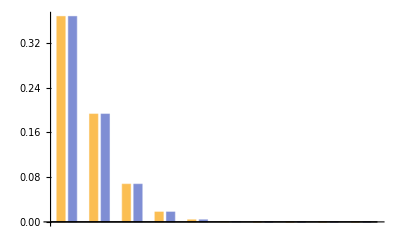

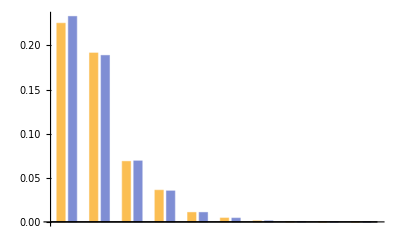

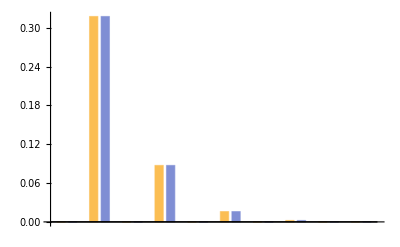

```mathematica
BarChart[Transpose[{dist[0,0,1,1,1,1,1.05,1.1,10],dist[0,0,1.05,1.1,1.05,1.1,1,1,10]}]]
BarChart[Transpose[{dist[0.5,1/1.5,1,1,1,1,1.,1.1,10],dist[0.5,1/1.5,1.,1.1,1.,1.1,1,1,10]}]]
BarChart[Transpose[{dist[1,1,1,1,1,1,1.,1.1,10],dist[1,1,1.,1.1,1.,1.1,1,1,10]}]]
```

Female fecundity selection alone: The mean is equivalent to viability selection with the appropriate dominance coefficient

```mathematica
(*Female fecundity*)
FullSimplify[mean[F,σ,1+h s, 1+s,1,1,1,1]-1]
FullSimplify[mean[0,0,1,1,1,1,1+(h+F-h F) s(1+σ)/2,1]-1]
```

((F-3 F^2 (-1+h)+h+2 F h) s)/(2 (1+F))

1/2 (F+h-F h) s (1+σ)

Male fecundity selection alone: The mean is equivalent to viability selection with the appropriate dominance coefficient

```mathematica
FullSimplify[mean[F,σ,1,1,1+h s, 1+s,1,1]-1]
FullSimplify[mean[0,0,1,1,1,1,1+(h+F-h F) s(1-σ)/2,1]-1]
```

((-1+F) (F (-1+h)-h) s)/(2 (1+F))

1/2 (F+h-F h) s (1-σ)

In both cases the variance is inflated by 1+F at first order but slightly different at higher orders.

```mathematica
Simplify[Series[var[F,(2F)/(1+F),1+h s, 1+s,1,1,1,1]/mean[F,(2F)/(1+F),1+h s, 1+s,1, 1,1,1],{s,0,1}]]
```

(1+F)+((-1+F) F (3 F (-1+h)-h) s)/(2 (1+F))+O[s]^2

```mathematica
Simplify[Series[var[F,(2F)/(1+F),1, 1,1+h s, 1+s,1,1]/mean[F,(2F)/(1+F),1, 1,1+h s, 1+s,1,1],{s,0,1}]]
```

(1+F)-(((-1+F) F (F (-1+h)-h)) s)/(2 (1+F))+O[s]^2

#### Two-patch model: seed migration

Using the mean reproductive matrix from the previous section, the probability of ultimate extinction is given by the product of two pgfs, assuming that the covariance between offspring produced in two patches is zero.

The order of the events are male and female fecundity selection, seed migration, viability selection.

```mathematica
pgfs[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_,M_,z_]=Simplify[F(pgfPois[ S WfAA M VAA/2,z^2]pgfPois[(1-S)/2 (WfAA + WmAA) M VAa,z])+(1-F)( pgfPois[S/2 WfAa  M VAA/2,z^2]pgfPois[(S/2 WfAa+(1-S)/2 (WfAa + WmAa ))M VAa,z])]
```

-ⅇ^((M (-1+z) (VAa (WfAa+F WfAa+WmAa-F WmAa)+F VAA WfAa (1+z)))/(2 (1+F))) (-1+F)+ⅇ^((M (-1+z) (-(-1+F) VAa (WfAA+WmAA)+2 F VAA WfAA (1+z)))/(2 (1+F))) F

For an offspring of patch i contributing to patch i we need to use index i for all fitness components and M = 1 - Mij
For an offspring from patch i contributing to patch j we need to use index i for fecundity fitness components and j for viability components, and M = Mij

The joined pgf is the product of pgf for i = j and i ≠ j

```mathematica
pgfseed[F_,σ_,
WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
Mij_,zi_,zj_]= Simplify[
pgfs[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,1-Mij,zi]
pgfs[F,S,WfAai,WfAAi,WmAai,WmAAi,VAaj,VAAj,Mij,zj]
]
```

(-ⅇ^(-((-1+Mij) (-1+zi) (VAai (WfAai+F WfAai+WmAai-F WmAai)+F VAAi WfAai (1+zi)))/(2 (1+F))) (-1+F)+ⅇ^(-((-1+Mij) (-1+zi) (-(-1+F) VAai (WfAAi+WmAAi)+2 F VAAi WfAAi (1+zi)))/(2 (1+F))) F) (-ⅇ^((Mij (-1+zj) (VAaj (WfAai+F WfAai+WmAai-F WmAai)+F VAAj WfAai (1+zj)))/(2 (1+F))) (-1+F)+ⅇ^((Mij (-1+zj) (-(-1+F) VAaj (WfAAi+WmAAi)+2 F VAAj WfAAi (1+zj)))/(2 (1+F))) F)

```mathematica
Subscript[f, 1]=Simplify[pgfseed[F,S,
1+hf1 sf1,1+sf1,1+hm1 sm1, 1+sm1,1+h1 s1,1+s1,1+h2 s2,1+s2,
M12,z1,z2]]
Subscript[f, 2]=Simplify[pgfseed[F,S,
1+hf2 sf2,1+sf2,1+hm2 sm2, 1+sm2,1+h2 s2,1+s2,1+h1 s1,1+s1,
M21,z1,z2]]
```

(-ⅇ^(-((-1+M12) (-1+z1) ((1+h1 s1) (2+(1+F) hf1 sf1+hm1 sm1-F hm1 sm1)+F (1+s1) (1+hf1 sf1) (1+z1)))/(2 (1+F))) (-1+F)+ⅇ^(-((-1+M12) (-1+z1) (-(-1+F) (1+h1 s1) (2+sf1+sm1)+2 F (1+s1) (1+sf1) (1+z1)))/(2 (1+F))) F) (-ⅇ^((M12 (-1+z2) ((1+h2 s2) (2+(1+F) hf1 sf1+hm1 sm1-F hm1 sm1)+F (1+s2) (1+hf1 sf1) (1+z2)))/(2 (1+F))) (-1+F)+ⅇ^((M12 (-1+z2) (-(-1+F) (1+h2 s2) (2+sf1+sm1)+2 F (1+s2) (1+sf1) (1+z2)))/(2 (1+F))) F)

(-ⅇ^(-((-1+M21) (-1+z1) ((1+h2 s2) (2+(1+F) hf2 sf2+hm2 sm2-F hm2 sm2)+F (1+s2) (1+hf2 sf2) (1+z1)))/(2 (1+F))) (-1+F)+ⅇ^(-((-1+M21) (-1+z1) (-(-1+F) (1+h2 s2) (2+sf2+sm2)+2 F (1+s2) (1+sf2) (1+z1)))/(2 (1+F))) F) (-ⅇ^((M21 (-1+z2) ((1+h1 s1) (2+(1+F) hf2 sf2+hm2 sm2-F hm2 sm2)+F (1+s1) (1+hf2 sf2) (1+z2)))/(2 (1+F))) (-1+F)+ⅇ^((M21 (-1+z2) (-(-1+F) (1+h1 s1) (2+sf2+sm2)+2 F (1+s1) (1+sf2) (1+z2)))/(2 (1+F))) F)

```mathematica
momseed[F_,S_,WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
Mij_,ni_,nj_]:=Simplify[D[pgfseed[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
Mij,zi,zj],{zi,ni},{zj,nj}]/.{zi->1,zj->1}]
```

```mathematica
meanseed[F_,S_,WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
Mij_]=Simplify[
{momseed[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
Mij,1,0],
momseed[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
Mij,0,1]}]
```

{((-1+Mij) (2 F VAAi ((-1+F) WfAai-2 F WfAAi)+(-1+F) VAai ((1+F) WfAai+WmAai+F (WfAAi-WmAai+WmAAi))))/(2 (1+F)),(Mij (2 F VAAj (WfAai-F WfAai+2 F WfAAi)-(-1+F) VAaj ((1+F) WfAai+WmAai+F (WfAAi-WmAai+WmAAi))))/(2 (1+F))}

```mathematica
varseed[F_,S_,WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
Mij_]=Simplify[
{momseed[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
Mij,2,0],
momseed[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
Mij,0,2]
}
+meanseed[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
Mij]-meanseed[F,σ,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
Mij]^2]
```

{1/(4 (1+F)^2)(2 (1+F) (-1+Mij) (2 F VAAi ((-1+F) WfAai-2 F WfAAi)+(-1+F) VAai ((1+F) WfAai+WmAai+F (WfAAi-WmAai+WmAAi)))-(-1+Mij)^2 (2 F VAAi ((-1+F) WfAai-2 F WfAAi)+(-1+F) VAai ((1+F) WfAai+WmAai+F (WfAAi-WmAai+WmAAi)))^2+(1-Mij) ((1-F) (4 F (1+F) VAAi WfAai+(1-Mij) (2 F VAAi WfAai+VAai (WfAai+F WfAai+WmAai-F WmAai))^2)+F (8 F (1+F) VAAi WfAAi+(1-Mij) (-4 F VAAi WfAAi+(-1+F) VAai (WfAAi+WmAAi))^2))),1/(4 (1+F)^2)Mij ((1-F) (4 F (1+F) VAAj WfAai+Mij (2 F VAAj WfAai+VAaj (WfAai+F WfAai+WmAai-F WmAai))^2)+F (8 F (1+F) VAAj WfAAi+Mij (-4 F VAAj WfAAi+(-1+F) VAaj (WfAAi+WmAAi))^2)+2 (1+F) (2 F VAAj (WfAai-F WfAai+2 F WfAAi)-(-1+F) VAaj ((1+F) WfAai+WmAai+F (WfAAi-WmAai+WmAAi)))-Mij (-2 F VAAj (WfAai-F WfAai+2 F WfAAi)+(-1+F) VAaj ((1+F) WfAai+WmAai+F (WfAAi-WmAai+WmAAi)))^2)}

#### Verifying properties of the pgf

For the different form of selection we retrieve the means obtained with the Jacobian analysis

```mathematica
Print["Viability selection"];meanseed[F,(2F)/(1+F),1,1,1,1,1+hi si,1+si,1+hj sj,1+sj,
Mij]//MatrixForm
Print["Female fecundity selection"];meanseed[F,(2F)/(1+F),1+hfi sfi,1+sfi,1,1,1,1,1,1,
Mij]//MatrixForm
Print["Male fecunidity selection"];meanseed[F,(2F)/(1+F),1,1,1+hmi smi,1+smi,1,1,1,1,
Mij]//MatrixForm
```

Viability selection

(((-1+Mij) (2 (-1-F) F (1+si)+(-1+F) (2+2 F) (1+hi si)))/(2 (1+F))
(Mij (2 F (1+F) (1+sj)-(-1+F) (2+2 F) (1+hj sj)))/(2 (1+F)))

Female fecundity selection

(((-1+Mij) (2 F (-2 F (1+sfi)+(-1+F) (1+hfi sfi))+(-1+F) (1+F (1+sfi)+(1+F) (1+hfi sfi))))/(2 (1+F))
(Mij (2 F (1+hfi sfi+2 F (1+sfi)-F (1+hfi sfi))-(-1+F) (1+F (1+sfi)+(1+F) (1+hfi sfi))))/(2 (1+F)))

Male fecunidity selection

(((-1+Mij) (2 (-1-F) F+(-1+F) (2+F+hmi smi+F (1+smi-hmi smi))))/(2 (1+F))
(Mij (2 F (1+F)-(-1+F) (2+F+hmi smi+F (1+smi-hmi smi))))/(2 (1+F)))

We can verify in the general case that for weak selection the variance is still inflated by 1+F

```mathematica
Simplify[Series[varseed[F,(2F)/(1+F),1+hfi sfi ϵ,1+sfi ϵ,1+hmi smi1 ϵ,1+smi ϵ,1+hi si ϵ,1+si ϵ,1+hj sj ϵ,1+sj ϵ,
Mij]/meanseed[F,(2F)/(1+F),1+hfi sfi ϵ,1+sfi ϵ,1+hmi smi1 ϵ,1+smi ϵ,1+hi si ϵ,1+si ϵ,1+hj sj ϵ,1+sj ϵ,
Mij],{ϵ,0,0}]]
```

{(1+F)+O[ϵ]^1,(1+F)+O[ϵ]^1}

#### Two-patch model: pollen migration

The order of the events are male fecundity selection, pollen migration, female fecundity selection and viability selection.
We need to write two pgf as the don’t have exactly the same form. For the contribution from i to j only outcross pollen can contribute

```mathematica
pgfii[F_,S_,WfAa_,WfAA_,WmAa_,WmAA_,VAa_,VAA_,m_,z_]=Simplify[F(pgfPois[ S WfAA  VAA/2,z^2]pgfPois[(1-S)/2(WfAA + m WmAA) VAa,z])+(1-F)( pgfPois[S/2 WfAa  VAA/2,z^2]pgfPois[(S/2 WfAa+(1-S)/2 (WfAa + m WmAa )) VAa,z])]
pgfij[F_,S_,WmAa_,WmAA_,VAa_,VAA_,m_,z_]=Simplify[F(pgfPois[(1-S)/2 (m WmAA) VAa,z])+(1-F)( pgfPois[(1-S)/2 ( m WmAa ) VAa,z])]
```

-ⅇ^(((-1+z) (VAa (WfAa+F WfAa+m WmAa-F m WmAa)+F VAA WfAa (1+z)))/(2 (1+F))) (-1+F)+ⅇ^(((-1+z) (-(-1+F) VAa (WfAA+m WmAA)+2 F VAA WfAA (1+z)))/(2 (1+F))) F

-ⅇ^(-((-1+F) m VAa WmAa (-1+z))/(2 (1+F))) (-1+F)+ⅇ^(-((-1+F) m VAa WmAA (-1+z))/(2 (1+F))) F

For an offspring of patch i contributing to patch i we need to use index i for all fitness components and m = 1 - mij
For an offspring from patch i contributing to patch j we need to use index i for male fecundity finess components and j for viability components and there is no female fecundity component, and m = mij

The joined pgf is the product of pgf for i = j and i ≠ j

```mathematica
pgfpollen[F_,S_,
WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
mij_,zi_,zj_]= Simplify[
pgfii[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,1-mij,zi]
pgfij[F,S,WmAai,WmAAi,VAaj,VAAj,mij,zj]
]
```

(-ⅇ^(((-1+zi) ((1+F) VAai WfAai+(-1+F) (-1+mij) VAai WmAai+F VAAi WfAai (1+zi)))/(2 (1+F))) (-1+F)+ⅇ^(((-1+zi) (-(-1+F) VAai (WfAAi+WmAAi-mij WmAAi)+2 F VAAi WfAAi (1+zi)))/(2 (1+F))) F) (-ⅇ^(-((-1+F) mij VAaj WmAai (-1+zj))/(2 (1+F))) (-1+F)+ⅇ^(-((-1+F) mij VAaj WmAAi (-1+zj))/(2 (1+F))) F)

```mathematica
mompollen[F_,S_,WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
mij_,ni_,nj_]:=Simplify[D[pgfpollen[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
mij,zi,zj],{zi,ni},{zj,nj}]/.{zi->1,zj->1}]
```

```mathematica
meanpollen[F_,S_,WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
mij_]=Simplify[
{mompollen[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
mij,1,0],
mompollen[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
mij,0,1]}]
```

{(2 F VAAi (WfAai-F WfAai+2 F WfAAi)-(-1+F) VAai ((1+F) WfAai+WmAai-mij WmAai+F (WfAAi+(-1+mij) (WmAai-WmAAi))))/(2 (1+F)),((-1+F) mij VAaj ((-1+F) WmAai-F WmAAi))/(2 (1+F))}

```mathematica
varpollen[F_,S_,WfAai_,WfAAi_,WmAai_,WmAAi_,VAai_,VAAi_,VAaj_,VAAj_,
mij_]=Simplify[
{mompollen[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
mij,2,0],
mompollen[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
mij,0,2]}
+meanpollen[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
mij]-meanpollen[F,S,WfAai,WfAAi,WmAai,WmAAi,VAai,VAAi,VAaj,VAAj,
mij]^2]
```

{1/(4 (1+F)^2)((1-F) (4 F (1+F) VAAi WfAai+((1+F) VAai WfAai+2 F VAAi WfAai+(-1+F) (-1+mij) VAai WmAai)^2)+2 (1+F) (2 F VAAi (WfAai-F WfAai+2 F WfAAi)-(-1+F) VAai ((1+F) WfAai+WmAai-mij WmAai+F (WfAAi+(-1+mij) (WmAai-WmAAi))))-(-2 F VAAi (WfAai-F WfAai+2 F WfAAi)+(-1+F) VAai ((1+F) WfAai+WmAai-mij WmAai+F (WfAAi+(-1+mij) (WmAai-WmAAi))))^2+F (8 F (1+F) VAAi WfAAi+(-4 F VAAi WfAAi+(-1+F) VAai (WfAAi+WmAAi-mij WmAAi))^2)),((-1+F) mij VAaj (2 (1+F) ((-1+F) WmAai-F WmAAi)-(-1+F) mij VAaj ((-1+F) WmAai-F WmAAi)^2+(-1+F) mij VAaj (-(-1+F) WmAai^2+F WmAAi^2)))/(4 (1+F)^2)}

For the different form of selection we retrieve the mean obtained with the Jacobian analysis

```mathematica
Print["Viability selection"] ;meanpollen[F,(2F)/(1+F),1,1,1,1,1+hi si,1+si,1+hj sj,1+sj,
mij]//MatrixForm
Print["Female fecundity selection"];meanpollen[F,(2F)/(1+F),1+hfi sfi,1+sfi,1,1,1,1,1,1,
mij]//MatrixForm
Print["Male fecundity selection"];FullSimplify[meanpollen[F,(2F)/(1+F),1,1,1+hmi smi,1+smi,1,1,1,1,
mij]]//MatrixForm
```

Viability selection

((2 F (1+F) (1+si)-(-1+F) (2+2 F-mij) (1+hi si))/(2 (1+F))
-((-1+F) mij (1+hj sj))/(2 (1+F)))

Female fecundity selection

((2 F (1+hfi sfi+2 F (1+sfi)-F (1+hfi sfi))-(-1+F) (1-mij+F (1+sfi)+(1+F) (1+hfi sfi)))/(2 (1+F))
-((-1+F) mij)/(2 (1+F)))

Male fecundity selection

(-(-2+mij-F (2+mij)+(-1+F) (F (-1+hmi)-hmi) (-1+mij) smi)/(2 (1+F))
((-1+F) mij (-1+F (-1+hmi) smi-hmi smi))/(2 (1+F)))

Contrary to seed migration the variance is inflated by more than 1+F for the local contribution and is simply 1 for the migrant contribution. However, this doesn’t alter the global results because we assume that migration is of the order of selection so also small in BP derivation.

```mathematica
FullSimplify[Series[varpollen[F,(2F)/(1+F),1+hfi sfi ϵ,1+sfi ϵ,1+hmi smi1 ϵ,1+smi ϵ,1+hi si ϵ,1+si ϵ,1+hj sj ϵ,1+sj ϵ,
mij]/meanpollen[F,(2F)/(1+F),1+hfi sfi ϵ,1+sfi ϵ,1+hmi smi1 ϵ,1+smi ϵ,1+hi si ϵ,1+si ϵ,1+hj sj ϵ,1+sj ϵ,
mij],{ϵ,0,0}]]
```

{(1+(2 F (1+F))/(2-mij+F (2+mij)))+O[ϵ]^1,1+O[ϵ]^1}

We can note that the variance factor can be written as (1+ F /(1-Meff)) where Meff = (1-S)m/2 is the effective migration rate.

```mathematica
FullSimplify[1+ F/(1-Meff)/.Meff->mij(1-S)/2/.S->2F/(1+F)]
```

1+(2 F (1+F))/(2-mij+F (2+mij))

Note also that the effect is weak

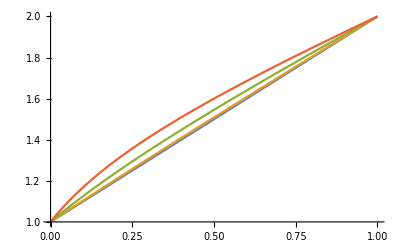

```mathematica
Plot[{1+F,1+(2 F (1+F))/(2-mij+F (2+mij))/.mij->0.1,1+(2 F (1+F))/(2-mij+F (2+mij))/.mij->0.5,1+(2 F (1+F))/(2-mij+F (2+mij))/.mij->1},{F,0,1}]
```

### Selection-migration ordering

#### Probability generating function and the eigensystem of reproductive mean matrix

In what follows we consider the effecitve migration and selection coefficients to simplify notations.
Mean reproductive matrix is obtained from the PGF as in the previous section.

```mathematica
Subscript[M, 11]=(1-Subscript[m, 12]) (1+Subscript[s, 1]);
Subscript[M, 12]=Subscript[m, 21] (1+Subscript[s, 1]);
Subscript[M, 21]=Subscript[m, 12] (1+Subscript[s, 2]);
Subscript[M, 22]=(1-Subscript[m, 21]) (1+Subscript[s, 2]);
```

```mathematica
meanM={{Subscript[M, 11],Subscript[M, 12]},{Subscript[M, 21],Subscript[M, 22]}};
meanM//MatrixForm
```

((1-m_12) (1+s_1) | m_21 (1+s_1)
m_12 (1+s_2) | (1-m_21) (1+s_2))

Calculate maximal eigenvalue of mean matrix:

```mathematica
Lambdas=Simplify[Eigenvalues[FullSimplify[meanM]]];
```

```mathematica
Lambdas=Eigenvalues[FullSimplify[meanM]];
```

The second λ is the largest positive eigenvalue:

```mathematica
ρ=FullSimplify[Lambdas[[2]]]
```

1/2 (2-m_21+s_1-m_12 (1+s_1)+s_2-m_21 s_2+√(4 (-1+m_12+m_21) (1+s_1) (1+s_2)+(2+s_1-m_12 (1+s_1)+s_2-m_21 (1+s_2))^2))

```mathematica
v=(Eigenvectors[meanM]);
u=(Eigenvectors@Transpose[meanM]);
```

```mathematica
u//MatrixForm
v//MatrixForm
```

(-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2+√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_21 (1+s_1)) | 1
-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2-√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_21 (1+s_1)) | 1)

(-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2+√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_12 (1+s_2)) | 1
-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2-√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_12 (1+s_2)) | 1)

Now we obtain normalized eigenvectors of mean matrix:

```mathematica
Subscript[u, 1,prim]=(u[[2]][[1]])/(u[[2]][[1]]+u[[2]][[2]]);
Subscript[u, 2,prim]=(u[[2]][[2]])/(u[[2]][[1]]+u[[2]][[2]]);
```

```mathematica
Subscript[v, 1,prim]=(v[[2]][[1]])/(Subscript[u, 1,prim] v[[2]][[1]]+Subscript[u, 2,prim] v[[2]][[2]]);
Subscript[v, 2,prim]=(v[[2]][[2]])/(Subscript[u, 1,prim] v[[2]][[1]]+Subscript[u, 2,prim] v[[2]][[2]]);
```

#### Conditions for supercriticality

Rewrite eigenvalue via composite parameters χ and ζ:

```mathematica
Subscript[ρ, trans]=ρ/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]}
```

1/2 (2+s_1+ζ s_1-s_1 (1+s_1) χ_12-s_1 χ_21-ζ s_1^2 χ_21+√(4 (1+s_1) (1+ζ s_1) (-1+s_1 χ_12+s_1 χ_21)+(2+s_1+ζ s_1-s_1 (1+s_1) χ_12-s_1 (1+ζ s_1) χ_21)^2))

Following Tomasini and Peischl (2018):
1. s_1 is small, meaning that selection is weak
2. Approximate ρ=1+s_1 ϵ, where ϵ depends on the parameters in the model
3. Derive supercriticality condition, that is the conditions under which ϵ>0

```mathematica
raw=Simplify[Normal[Series[Subscript[ρ, trans],{Subscript[s, 1],0,1}]],Subscript[s, 1]>0];
Subscript[ρ, approx]=FullSimplify[ExpandAll[raw]/.Subscript[s, 1]^2->0];
ϵ=Subscript[ρ, approx][[2]][[1]]Subscript[ρ, approx][[2]][[3]]
```

1/2 (1+ζ-χ_12-χ_21+√((-1+ζ+χ_12)^2+2 (1-ζ+χ_12) χ_21+χ_21^2))

Branching process is going to be supercritical whenever ρ>1. Given that s_1>0, the invasion can occur only when ϵ>0:

```mathematica
Reduce[ϵ>0&&Subscript[χ, 12]>1&&Subscript[χ, 21]>1]
```

χ_12>1&&χ_21>1&&ζ>-χ_21/(-1+χ_12)

Algebraic manipulation yields Bulmer’s condition:

```mathematica
FullSimplify[ζ>-Subscript[χ, 21]/(-1+Subscript[χ, 12])/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]
```

s_2/s_1>m_21/(-m_12+s_1)

```mathematica
Subscript[s, 2] Subscript[s, 1]>Subscript[s, 1] Subscript[m, 21]+Subscript[s, 2] Subscript[m, 12];
1>Subscript[s, 1] Subscript[m, 21]/(Subscript[s, 1] Subscript[s, 2])+Subscript[s, 2] Subscript[m, 12]/(Subscript[s, 1] Subscript[s, 2]);
BulmerCond=Subscript[m, 21]/Subscript[s, 2]+Subscript[m, 12]/Subscript[s, 1]<1;
```

Noting that s_1:=h_e s_1 and s_2:=k_e s_2:

```mathematica
BulmerCond/.{Subscript[s, 1]->Subscript[s, 1] he,Subscript[s, 2]->Subscript[s, 2] ke}/.{he->((1-F)h+F),ke->((1-F)k+F)}
```

m_12/((F+(1-F) h) s_1)+m_21/((F+(1-F) k) s_2)<1

The case when m_12>>s_1, meaning that selection in beneficial patch is very weak, process is subcritical because it depends on the ratio of two coefficients with opposite signs (criticality coefficient  equals ζ).

```mathematica
Limit[ϵ,Subscript[χ, 12]->Infinity]
```

ζ

When selection in deleterious patch is much stronger, process is supercritical as long as χ_12>0, which means that migration should be of the same order as selection:

```mathematica
Limit[ϵ,ζ->-Infinity]
```

1-χ_12

In the case of symmetric migration:

```mathematica
symmetricEpsilon=FullSimplify[ϵ/.{Subscript[χ, 12]->χ,Subscript[χ, 21]->χ}]
```

1/2 (1+ζ-2 χ+√((-1+ζ)^2+4 χ^2))

For supercriticality, ϵ>0:

```mathematica
Reduce[symmetricEpsilon>0,χ]
```

χ∈ℝ&&((ζ<-1&&χ<ζ/(1+ζ))||ζ≥-1)

Condition ζ<-1  is always true, because one of the selection coefficients is always less than zero.

If selection in deleterious patch is very strong, the process is supercritical as longs as χ<1, hence m<s_1:

```mathematica
Limit[symmetricEpsilon,ζ->-Infinity]
```

1-χ

When migration is much stronger then selection, supercriticality exists as long as ζ>-1 or, in other words, |s_2| < s_1:

```mathematica
Limit[symmetricEpsilon,χ->Infinity]
```

(1+ζ)/2

#### Deriving the probability of establishment in k^th patch (P_(est,k))

We begin by noting that P_(est,k) can be calculated:
P_(est,k)=2(ρ-1)v_k/B+(O(ϵ))^2

To do so, we need:
ρ - leading eigenvalue of reproductive matrix
v_k - k^th normalized right eigenvector
B=Σ_h u_h Var[Σ_j v_j ϵ_hj]+ρ(ρ-1)Σ_j u_j v_j^2

#### Seed migration

The variance in offspring number is obtained form the pgf as in the previous section

```mathematica
Varϵ11=(1+F) (1-Subscript[m, 12]) (1+Subscript[s, 1]);
Varϵ21=(1+F) Subscript[m, 21] (1+Subscript[s, 1]);
Varϵ12=(1+F) Subscript[m, 12] (1+Subscript[s, 2]);
Varϵ22=(1+F) (1-Subscript[m, 21]) (1+Subscript[s, 2]);
```

Next, we compute the denominator term B in Eshel’s formula:

```mathematica
termH1=FullSimplify[(Subscript[v, 1,prim])^2 Varϵ11+(Subscript[v, 2,prim])^2 Varϵ12];
termH2=FullSimplify[(Subscript[v, 1,prim])^2 Varϵ21+(Subscript[v, 2,prim])^2 Varϵ22];
```

Term A corresponds to Σ_h u_h Var[Σ_j v_j ϵ_hj].
Term B corresponds to ρ(ρ-1)Σ_j u_j v_j^2

```mathematica
termA=Simplify[Subscript[u, 1,prim] termH1+Subscript[u, 2,prim] termH2];
termB=Simplify[ρ(ρ-1)(Subscript[u, 1,prim](Subscript[v, 1,prim])^2+Subscript[u, 2,prim](Subscript[v, 2,prim])^2)];
B=Simplify[termA+termB];
```

P_est conditioning on allele appearing in patch 1

Since computation is difficult, we let only ρ depend on s_1 by linearizing about s_1=0 and taking 0^th and 1^st term in Taylor series. Term v_k/B is expanded about s_1, but we only take 0^th term.
Procedure for obtaining the approximated P_(est,k) (the probability of establishment in patch k):

ρ̃=1+ϵ s_1+O(s_1^2)≃1+ϵ s_1
Let y_k(s_1)=v_k/B=v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj]+ρ(ρ-1)Σ_j u_j v_j^2)≃v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj])
Given that ρ≃1, ρ(ρ-1)Σ_j u_j v_j^2≃0
(ỹ)_k(s_1)= y_k(0)+O(y_k(s_1))≃y_k(0)
P_(est,k)=2ϵ y_k(0)s_1

```mathematica
(* Approximate Subscript[y, k]=Subscript[v, k]/B *)
yTerm1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 1,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox1=Normal[Series[yTerm1,{Subscript[s, 1],0,0}]];
```

```mathematica
(* Multiply with 2 Subscript[ϵs, 1] to obtain Subscript[P, est,k] *)
Pest1Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox1]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest1Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

((-m_12+m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (-m_12-m_21+s_1+s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (m_12^2-m_12 (-2 m_21+2 s_1-2 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2) (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))))/(2 (1+F) (-m_12^3+m_12^2 (2 m_21+3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2)^2 (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))-m_12 (m_21 (3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(s_1-s_2) (3 s_1-3 s_2+2 √(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))))))

P_est conditioning on allele appearing in patch 2

Similar procedure is used to derive P_(est,2), but now we use v_2 instead:

```mathematica
yTerm2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 2,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox2=Normal[Series[yTerm2,{Subscript[s, 1],0,0}]];
```

```mathematica
Pest2Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox2]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest2Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

(m_12 (-m_12-m_21+s_1+s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (m_12^2-m_12 (-2 m_21+2 s_1-2 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2) (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))))/((1+F) (-m_12^3+m_12^2 (2 m_21+3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2)^2 (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))-m_12 (m_21 (3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(s_1-s_2) (3 s_1-3 s_2+2 √(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))))))

We focus on the case when migration is symmetrical. In the appendix, P_est is written in the following form:

```mathematica
pEst1SelMig=FullSimplify[pEst1/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
pEst2SelMig=FullSimplify[pEst2/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
```

((m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12+m_21+s_1-s_2) (ψ-m_12-m_21+s_1+s_2))/(2 (1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

(m_12 (m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12-m_21+s_1+s_2))/((1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

```mathematica
Assuming[{m>0,Subscript[s, 1]>0,Subscript[s, 2]<0},√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))/.{Subscript[m, 12]->m,Subscript[m, 21]->m}//FullSimplify]
```

√(4 m^2+(s_1-s_2)^2)

#### Pollen migration

The variance in offspring number is obtained form the pgf as in the previous section

```mathematica
Varϵ11=(1+F/(1-Subscript[m, 12])) (1-Subscript[m, 12]) (1+Subscript[s, 1]);
Varϵ21= Subscript[m, 21] (1+Subscript[s, 1]);
Varϵ12= Subscript[m, 12] (1+Subscript[s, 2]);
Varϵ22=(1+F/(1-Subscript[m, 21])) (1-Subscript[m, 21]) (1+Subscript[s, 2]);
```

Next, we compute the denominator term B in Eshel’s formula:

```mathematica
termH1=Simplify[(Subscript[v, 1,prim])^2 Varϵ11+(Subscript[v, 2,prim])^2 Varϵ12];
termH2=Simplify[(Subscript[v, 1,prim])^2 Varϵ21+(Subscript[v, 2,prim])^2 Varϵ22];
```

Term A corresponds to Σ_h u_h Var[Σ_j v_j ϵ_hj].
Term B corresponds to ρ(ρ-1)Σ_j u_j v_j^2

```mathematica
termA=Simplify[Subscript[u, 1,prim] termH1+Subscript[u, 2,prim] termH2];
termB=Simplify[ρ(ρ-1)(Subscript[u, 1,prim](Subscript[v, 1,prim])^2+Subscript[u, 2,prim](Subscript[v, 2,prim])^2)];
B=Simplify[termA+termB];
```

P_est conditioning on allele appearing in patch 1

Since computation is difficult, we let only ρ depend on s_1 by linearizing about s_1=0 and taking 0^th and 1^st term in Taylor series. Term v_k/B is expanded about s_1, but we only take 0^th term.
Procedure for obtaining the approximated P_(est,k) (the probability of establishment in patch k):

ρ̃=1+ϵ s_1+O(s_1^2)≃1+ϵ s_1
Let y_k(s_1)=v_k/B=v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj]+ρ(ρ-1)Σ_j u_j v_j^2)≃v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj])
Given that ρ≃1, ρ(ρ-1)Σ_j u_j v_j^2≃0
(ỹ)_k(s_1)= y_k(0)+O(y_k(s_1))≃y_k(0)
P_(est,k)=2ϵ y_k(0)s_1

```mathematica
(* Approximate Subscript[y, k]=Subscript[v, k]/B *)
yTerm1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 1,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox1=Normal[Series[yTerm1,{Subscript[s, 1],0,0}]];
```

```mathematica
(* Multiply with 2 Subscript[ϵs, 1] to obtain Subscript[P, est,k] *)
Pest1Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox1]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest1Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

((-m_12+m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (-m_12-m_21+s_1+s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (m_12^2-m_12 (-2 m_21+2 s_1-2 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2) (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))))/(2 (1+F) (-m_12^3+m_12^2 (2 m_21+3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2)^2 (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))-m_12 (m_21 (3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(s_1-s_2) (3 s_1-3 s_2+2 √(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))))))

P_est conditioning on allele appearing in patch 2

Similar procedure is used to derive P_(est,2), but now we use v_2 instead:

```mathematica
yTerm2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 2,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox2=Normal[Series[yTerm2,{Subscript[s, 1],0,0}]];
```

```mathematica
Pest2Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox2]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest2Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

(m_12 (-m_12-m_21+s_1+s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (m_12^2-m_12 (-2 m_21+2 s_1-2 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2) (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))))/((1+F) (-m_12^3+m_12^2 (2 m_21+3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2)^2 (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))-m_12 (m_21 (3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(s_1-s_2) (3 s_1-3 s_2+2 √(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))))))

We focus on the case when migration is symmetrical. In the appendix, P_est is written in the following form:

```mathematica
pEst1SelMig=FullSimplify[pEst1/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
pEst2SelMig=FullSimplify[pEst2/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
```

((m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12+m_21+s_1-s_2) (ψ-m_12-m_21+s_1+s_2))/(2 (1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

(m_12 (m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12-m_21+s_1+s_2))/((1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

```mathematica
Assuming[{m>0,Subscript[s, 1]>0,Subscript[s, 2]<0},√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))/.{Subscript[m, 12]->m,Subscript[m, 21]->m}//FullSimplify]
```

√(4 m^2+(s_1-s_2)^2)

The results are the same as for seed migration (using appropriate effective parameters).

### Migration-selection ordering (used in further computations)

#### Probability generating function and the eigensystem of reproductive mean matrix

In what follows we consider the effective migration and selection coefficients to simplify notations.
Mean reproductive matrix is obtained from the PGF as in the previous section.

```mathematica
Subscript[M, 11]=(1-Subscript[m, 12]) (1+Subscript[s, 1]);
Subscript[M, 12]=Subscript[m, 21] (1+Subscript[s, 2]);
Subscript[M, 21]=Subscript[m, 12] (1+Subscript[s, 1]);
Subscript[M, 22]=(1-Subscript[m, 21]) (1+Subscript[s, 2]);
```

```mathematica
meanM={{Subscript[M, 11],Subscript[M, 12]},{Subscript[M, 21],Subscript[M, 22]}};
meanM//MatrixForm
```

((1-m_12) (1+s_1) | m_21 (1+s_2)
m_12 (1+s_1) | (1-m_21) (1+s_2))

Calculate maximal eigenvalue of mean matrix:

```mathematica
Lambdas=Simplify[Eigenvalues[FullSimplify[meanM]]];
```

```mathematica
Lambdas=Eigenvalues[FullSimplify[meanM]];
```

The second λ is the largest positive eigenvalue:

```mathematica
ρ=FullSimplify[Lambdas[[2]]]
```

1/2 (2-m_21+s_1-m_12 (1+s_1)+s_2-m_21 s_2+√(4 (-1+m_12+m_21) (1+s_1) (1+s_2)+(2+s_1-m_12 (1+s_1)+s_2-m_21 (1+s_2))^2))

```mathematica
v=(Eigenvectors[meanM]);
u=(Eigenvectors@Transpose[meanM]);
```

```mathematica
u//MatrixForm
v//MatrixForm
```

(-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2+√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_21 (1+s_2)) | 1
-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2-√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_21 (1+s_2)) | 1)

(-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2+√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_12 (1+s_1)) | 1
-(m_12-m_21-s_1+m_12 s_1+s_2-m_21 s_2-√(m_12^2+2 m_12 m_21+m_21^2-2 m_12 s_1+2 m_12^2 s_1+2 m_21 s_1+2 m_12 m_21 s_1+s_1^2-2 m_12 s_1^2+m_12^2 s_1^2+2 m_12 s_2-2 m_21 s_2+2 m_12 m_21 s_2+2 m_21^2 s_2-2 s_1 s_2+2 m_12 s_1 s_2+2 m_21 s_1 s_2+2 m_12 m_21 s_1 s_2+s_2^2-2 m_21 s_2^2+m_21^2 s_2^2))/(2 m_12 (1+s_1)) | 1)

Now we obtain normalized eigenvectors of mean matrix:

```mathematica
Subscript[u, 1,prim]=(u[[2]][[1]])/(u[[2]][[1]]+u[[2]][[2]]);
Subscript[u, 2,prim]=(u[[2]][[2]])/(u[[2]][[1]]+u[[2]][[2]]);
```

```mathematica
Subscript[v, 1,prim]=(v[[2]][[1]])/(Subscript[u, 1,prim] v[[2]][[1]]+Subscript[u, 2,prim] v[[2]][[2]]);
Subscript[v, 2,prim]=(v[[2]][[2]])/(Subscript[u, 1,prim] v[[2]][[1]]+Subscript[u, 2,prim] v[[2]][[2]]);
```

#### Conditions for supercriticality

Rewrite eigenvalue via composite parameters χ and ζ:

```mathematica
Subscript[ρ, trans]=ρ/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]}
```

1/2 (2+s_1+ζ s_1-s_1 (1+s_1) χ_12-s_1 χ_21-ζ s_1^2 χ_21+√(4 (1+s_1) (1+ζ s_1) (-1+s_1 χ_12+s_1 χ_21)+(2+s_1+ζ s_1-s_1 (1+s_1) χ_12-s_1 (1+ζ s_1) χ_21)^2))

Following Tomasini and Peischl (2018):
1. s_1 is small, meaning that selection is weak
2. Approximate ρ=1+s_1 ϵ, where ϵ depends on the parameters in the model
3. Derive supercriticality condition, that is the conditions under which ϵ>0

```mathematica
raw=Simplify[Normal[Series[Subscript[ρ, trans],{Subscript[s, 1],0,1}]],Subscript[s, 1]>0];
Subscript[ρ, approx]=FullSimplify[ExpandAll[raw]/.Subscript[s, 1]^2->0];
ϵ=Subscript[ρ, approx][[2]][[1]]Subscript[ρ, approx][[2]][[3]]
```

1/2 (1+ζ-χ_12-χ_21+√((-1+ζ+χ_12)^2+2 (1-ζ+χ_12) χ_21+χ_21^2))

Branching process is going to be supercritical whenever ρ>1. Given that s_1>0, the invasion can occur only when ϵ>0:

```mathematica
Reduce[ϵ>0&&Subscript[χ, 12]>1&&Subscript[χ, 21]>1]
```

χ_12>1&&χ_21>1&&ζ>-χ_21/(-1+χ_12)

Algebraic manipulation yields Bulmer’s condition:

```mathematica
FullSimplify[ζ>-Subscript[χ, 21]/(-1+Subscript[χ, 12])/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]
```

s_2/s_1>m_21/(-m_12+s_1)

```mathematica
Subscript[s, 2] Subscript[s, 1]>Subscript[s, 1] Subscript[m, 21]+Subscript[s, 2] Subscript[m, 12];
1>Subscript[s, 1] Subscript[m, 21]/(Subscript[s, 1] Subscript[s, 2])+Subscript[s, 2] Subscript[m, 12]/(Subscript[s, 1] Subscript[s, 2]);
BulmerCond=Subscript[m, 21]/Subscript[s, 2]+Subscript[m, 12]/Subscript[s, 1]<1;
```

Noting that s_1:=h_e s_1 and s_2:=k_e s_2:

```mathematica
BulmerCond/.{Subscript[s, 1]->Subscript[s, 1] he,Subscript[s, 2]->Subscript[s, 2] ke}/.{he->((1-F)h+F),ke->((1-F)k+F)}
```

m_12/((F+(1-F) h) s_1)+m_21/((F+(1-F) k) s_2)<1

The case when m_12>>s_1, meaning that selection in beneficial patch is very weak, process is subcritical because it depends on the ratio of two coefficients with opposite signs (criticality coefficient  equals ζ).

```mathematica
Limit[ϵ,Subscript[χ, 12]->Infinity]
```

ζ

When selection in deleterious patch is much stronger, process is supercritical as long as χ_12>0, which means that migration should be of the same order as selection:

```mathematica
Limit[ϵ,ζ->-Infinity]
```

1-χ_12

In the case of symmetric migration:

```mathematica
symmetricEpsilon=FullSimplify[ϵ/.{Subscript[χ, 12]->χ,Subscript[χ, 21]->χ}]
```

1/2 (1+ζ-2 χ+√((-1+ζ)^2+4 χ^2))

For supercriticality, ϵ>0:

```mathematica
Reduce[symmetricEpsilon>0,χ]
```

χ∈ℝ&&((ζ<-1&&χ<ζ/(1+ζ))||ζ≥-1)

Condition ζ<-1  is always true, because one of the selection coefficients is always less than zero.

If selection in deleterious patch is very strong, the process is supercritical as longs as χ<1, hence m<s_1:

```mathematica
Limit[symmetricEpsilon,ζ->-Infinity]
```

1-χ

When migration is much stronger then selection, supercriticality exists as long as ζ>-1 or, in other words, |s_2| < s_1:

```mathematica
Limit[symmetricEpsilon,χ->Infinity]
```

(1+ζ)/2

#### Deriving the probability of establishment in k^th patch (P_(est,k))

We begin by noting that P_(est,k) can be calculated:
P_(est,k)=2(ρ-1)v_k/B+(O(ϵ))^2

To do so, we need:
ρ - leading eigenvalue of reproductive matrix
v_k - k^th normalized right eigenvector
B=Σ_h u_h Var[Σ_j v_j ϵ_hj]+ρ(ρ-1)Σ_j u_j v_j^2

#### Seed migration

The variance in offspring number is obtained form the pgf as in the previous section

```mathematica
Varϵ11=(1+F) (1-Subscript[m, 12]) (1+Subscript[s, 1]);
Varϵ21=(1+F) Subscript[m, 21] (1+Subscript[s, 2]);
Varϵ12=(1+F) Subscript[m, 12] (1+Subscript[s, 1]);
Varϵ22=(1+F) (1-Subscript[m, 21]) (1+Subscript[s, 2]);
```

Next, we compute the denominator term B in Eshel’s formula:

```mathematica
termH1=Simplify[(Subscript[v, 1,prim])^2 Varϵ11+(Subscript[v, 2,prim])^2 Varϵ12];
termH2=Simplify[(Subscript[v, 1,prim])^2 Varϵ21+(Subscript[v, 2,prim])^2 Varϵ22];
```

Term A corresponds to Σ_h u_h Var[Σ_j v_j ϵ_hj].
Term B corresponds to ρ(ρ-1)Σ_j u_j v_j^2

```mathematica
termA=Simplify[Subscript[u, 1,prim] termH1+Subscript[u, 2,prim] termH2];
termB=Simplify[ρ(ρ-1)(Subscript[u, 1,prim](Subscript[v, 1,prim])^2+Subscript[u, 2,prim](Subscript[v, 2,prim])^2)];
B=Simplify[termA+termB];
```

P_est conditioning on allele appearing in patch 1

Since computation is difficult, we let only ρ depend on s_1 by linearizing about s_1=0 and taking 0^th and 1^st term in Taylor series. Term v_k/B is expanded about s_1, but we only take 0^th term.
Procedure for obtaining the approximated P_(est,k) (the probability of establishment in patch k):

ρ̃=1+ϵ s_1+(O(s_1))^2≃1+ϵ s_1
Let y_k(s_1)=v_k/B=v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj]+ρ(ρ-1)Σ_j u_j v_j^2)≃v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj])
Given that ρ≃1, ρ(ρ-1)Σ_j u_j v_j^2≃0
(ỹ)_k(s_1)= y_k(0)+O(y_k(s_1))≃y_k(0)
P_(est,k)=2ϵ y_k(0)s_1

```mathematica
(* Approximate Subscript[y, k]=Subscript[v, k]/B *)
yTerm1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 1,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox1=Normal[Series[yTerm1,{Subscript[s, 1],0,0}]];
```

```mathematica
(* Multiply with 2 Subscript[ϵs, 1] to obtain Subscript[P, est,k] *)
Pest1Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox1]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest1Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

P_est conditioning on allele appearing in patch 2

Similar procedure is used to derive P_(est,2), but now we use v_2 instead:

```mathematica
yTerm2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 2,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox2=Normal[Series[yTerm2,{Subscript[s, 1],0,0}]];
```

```mathematica
Pest2Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox2]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest2Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

We focus on the case when migration is symmetrical. In the appendix, P_est is written in the following form:

```mathematica
pEst1MigSel=FullSimplify[pEst1/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
pEst2MigSel=FullSimplify[pEst2/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
```

((m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12+m_21+s_1-s_2) (ψ-m_12-m_21+s_1+s_2))/(2 (1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

(m_12 (m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12-m_21+s_1+s_2))/((1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

```mathematica
Assuming[{m>0,Subscript[s, 1]>0,Subscript[s, 2]<0},√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))/.{Subscript[m, 12]->m,Subscript[m, 21]->m}//FullSimplify]
```

√(4 m^2+(s_1-s_2)^2)

#### Pollen migration

The variance in offspring number is obtained form the pgf as in the previous section

```mathematica
Varϵ11=(1+F/(1-Subscript[m, 12])) (1-Subscript[m, 12]) (1+Subscript[s, 1]);
Varϵ21= Subscript[m, 21] (1+Subscript[s, 2]);
Varϵ12= Subscript[m, 12] (1+Subscript[s, 1]);
Varϵ22=(1+F/(1-Subscript[m, 12])) (1-Subscript[m, 21]) (1+Subscript[s, 2]);
```

Next, we compute the denominator term B in Eshel’s formula:

```mathematica
termH1=Simplify[(Subscript[v, 1,prim])^2 Varϵ11+(Subscript[v, 2,prim])^2 Varϵ12];
termH2=Simplify[(Subscript[v, 1,prim])^2 Varϵ21+(Subscript[v, 2,prim])^2 Varϵ22];
```

Term A corresponds to Σ_h u_h Var[Σ_j v_j ϵ_hj].
Term B corresponds to ρ(ρ-1)Σ_j u_j v_j^2

```mathematica
termA=Simplify[Subscript[u, 1,prim] termH1+Subscript[u, 2,prim] termH2];
termB=Simplify[ρ(ρ-1)(Subscript[u, 1,prim](Subscript[v, 1,prim])^2+Subscript[u, 2,prim](Subscript[v, 2,prim])^2)];
B=Simplify[termA+termB];
```

P_est conditioning on allele appearing in patch 1

Since computation is difficult, we let only ρ depend on s_1 by linearizing about s_1=0 and taking 0^th and 1^st term in Taylor series. Term v_k/B is expanded about s_1, but we only take 0^th term.
Procedure for obtaining the approximated P_(est,k) (the probability of establishment in patch k):

ρ̃=1+ϵ s_1+(O(s_1))^2≃1+ϵ s_1
Let y_k(s_1)=v_k/B=v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj]+ρ(ρ-1)Σ_j u_j v_j^2)≃v_k/(Σ_h u_h Var[Σ_j v_j ϵ_hj])
Given that ρ≃1, ρ(ρ-1)Σ_j u_j v_j^2≃0
(ỹ)_k(s_1)= y_k(0)+O(y_k(s_1))≃y_k(0)
P_(est,k)=2ϵ y_k(0)s_1

```mathematica
(* Approximate Subscript[y, k]=Subscript[v, k]/B *)
yTerm1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 1,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox1=Normal[Series[yTerm1,{Subscript[s, 1],0,0}]];
```

```mathematica
(* Multiply with 2 Subscript[ϵs, 1] to obtain Subscript[P, est,k] *)
Pest1Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox1]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst1=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest1Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

((-m_12+m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (-m_12-m_21+s_1+s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (m_12^2-m_12 (-2 m_21+2 s_1-2 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2) (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))))/(2 (1+F) (-m_12^3+m_12^2 (2 m_21+3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2)^2 (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))-m_12 (m_21 (3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(s_1-s_2) (3 s_1-3 s_2+2 √(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))))))

P_est conditioning on allele appearing in patch 2

Similar procedure is used to derive P_(est,2), but now we use v_2 instead:

```mathematica
yTerm2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[(Subscript[v, 2,prim]/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})/(termA/.{Subscript[m, 12]->Subscript[χ, 12] Subscript[s, 1],Subscript[m, 21]->Subscript[χ, 21] Subscript[s, 1],Subscript[s, 2]->ζ Subscript[s, 1]})]];
yTermApprox2=Normal[Series[yTerm2,{Subscript[s, 1],0,0}]];
```

```mathematica
Pest2Transf=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,ζ<0,Subscript[χ, 21]>0,Subscript[χ, 12]>0},Simplify[2 ϵ Subscript[s, 1]*yTermApprox2]] (* compute Subscript[P, est,1] with transformed parameters *);
pEst2=Assuming[{Subscript[m, 12]>0,Subscript[m, 21]>0,Subscript[s, 1]>0,Subscript[s, 2]<0},Simplify[Pest2Transf/.{Subscript[χ, 12]->Subscript[m, 12]/Subscript[s, 1],Subscript[χ, 21]->Subscript[m, 21]/Subscript[s, 1],ζ->Subscript[s, 2]/Subscript[s, 1]}]] (* back-transform parameters *)
```

(m_12 (-m_12-m_21+s_1+s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))) (m_12^2-m_12 (-2 m_21+2 s_1-2 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2) (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))))/((1+F) (-m_12^3+m_12^2 (2 m_21+3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(m_21+s_1-s_2)^2 (m_21+s_1-s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))-m_12 (m_21 (3 s_1-3 s_2+√(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2)))+(s_1-s_2) (3 s_1-3 s_2+2 √(m_12^2+(m_21+s_1-s_2)^2+2 m_12 (m_21-s_1+s_2))))))

We focus on the case when migration is symmetrical. In the appendix, P_est is written in the following form:

```mathematica
pEst1MigSel=FullSimplify[pEst1/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
pEst2MigSel=FullSimplify[pEst2/.{√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))->ψ}]
```

((m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12+m_21+s_1-s_2) (ψ-m_12-m_21+s_1+s_2))/(2 (1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

(m_12 (m_12^2-m_12 (ψ-2 m_21+2 s_1-2 s_2)+(m_21+s_1-s_2) (ψ+m_21+s_1-s_2)) (ψ-m_12-m_21+s_1+s_2))/((1+F) (-m_12^3-m_12 (m_21 (ψ+3 s_1-3 s_2)+(2 ψ+3 s_1-3 s_2) (s_1-s_2))+m_12^2 (ψ+2 m_21+3 s_1-3 s_2)+(m_21+s_1-s_2)^2 (ψ+m_21+s_1-s_2)))

```mathematica
Assuming[{m>0,Subscript[s, 1]>0,Subscript[s, 2]<0},√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))/.{Subscript[m, 12]->m,Subscript[m, 21]->m}//FullSimplify]
```

√(4 m^2+(s_1-s_2)^2)

The results are the same as for seed migration (using appropriate effective parameters).

### Different ordering yields identical P_est

```mathematica
{pEst1MigSel==pEst1SelMig,pEst2MigSel==pEst2SelMig}//FullSimplify
```

{True,True}

## 3. Diffusion approximation formalism

The probability of establishment is based on eqn. (2) in Sakamoto2020 with the exception that the effective population size is reduced by factor 1+F:

```mathematica
Pfix[x1_,x2_]=1-ⅇ^(-2 (n1/(1+F) x1 ψ1+n2/(1+F) x2 ψ2));
```

Next, we use their KBE but with two modifications. First, diffusion coefficient is rescaled with factor 1+F which accounts for increased variance, and second, selection coefficients are re-parameterized assuming that the fate of an allele is determined in the first phase of fixation:

```mathematica
kbeMaster=x1/(4 n1/(1+F))D[ϕ[x1,x2],{x1,2}]+x2/(4 n2/(1+F))D[ϕ[x1,x2],{x2,2}]+
(Subscript[s, 1] x1+m1(x2-x1))D[ϕ[x1,x2],x1]+(Subscript[s, 2] x2+m2(x1-x2))D[ϕ[x1,x2],x2]/.{Subscript[s, 1]->s1,Subscript[s, 2]->s2};
```

```mathematica
eq1=x1/(4 n1/(1+F))D[Pfix[x1,x2],{x1,2}]+x2/(4 n2/(1+F))D[Pfix[x1,x2],{x2,2}]+
(Subscript[s, 1] x1+m1(x2-x1))D[Pfix[x1,x2],x1]+(Subscript[s, 2] x2+m2(x1-x2))D[Pfix[x1,x2],x2]/.{x1->1/(2n1),x2->0}//FullSimplify
eq2=x1/(4 n1/(1+F))D[Pfix[x1,x2],{x1,2}]+x2/(4 n2/(1+F))D[Pfix[x1,x2],{x2,2}]+
(Subscript[s, 1] x1+m1(x2-x1))D[Pfix[x1,x2],x1]+(Subscript[s, 2] x2+m2(x1-x2))D[Pfix[x1,x2],x2]/.{x1->0,x2->1/(2n2)}//FullSimplify
```

(ⅇ^(-ψ1/(1+F)) (-n1 ψ1 (2 m1+ψ1)+2 m2 n2 ψ2+2 n1 ψ1 s_1))/(2 (1+F) n1)

(ⅇ^(-ψ2/(1+F)) (2 m1 n1 ψ1-n2 ψ2 (2 m2+ψ2)+2 n2 ψ2 s_2))/(2 (1+F) n2)

Parameters ψ are obtained by solving the system of equations.

```mathematica
sols=Solve[{eq1==0,eq2==0},{ψ1,ψ2}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

We take second root, because third and fourth are complex solutions, and first is zero:

```mathematica
ψ1Sol=sols[[2]][[All,2]][[1]];
ψ2Sol=sols[[2]][[All,2]][[2]];
```

Substitution in the formula for the establishment probability F yields the analytic solution:

```mathematica
fullSol[x1_,x2_]=Pfix[x1,x2]/.{ψ1->ψ1Sol,ψ2->ψ2Sol};
```

```mathematica
pFix1=fullSol[1/(2n1),0]/.{n1->n,n2->n,m1->Subscript[m, 12],m2->Subscript[m, 21],h->1/2,k->1/2}//Simplify
pFix2=fullSol[0,1/(2n2)]/.{n1->n,n2->n,m1->Subscript[m, 12],m2->Subscript[m, 21],h->1/2,k->1/2}//Simplify
```

1-ⅇ^(-(-8 m_12+8 s_1+(4 2^(1/3) (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2))/((2 m_12^3+18 m_12 m_21^2-6 m_12^2 s_1+9 m_21^2 s_1+6 m_12 s_1^2-2 s_1^3+9 m_12 m_21 s_2-9 m_21 s_1 s_2+√(-4 (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2)^3+(2 m_12^3-6 m_12^2 s_1+s_1 (9 m_21^2-2 s_1^2-9 m_21 s_2)+3 m_12 (6 m_21^2+2 s_1^2+3 m_21 s_2))^2))^(1/3))+2 2^(2/3) (2 m_12^3+18 m_12 m_21^2-6 m_12^2 s_1+9 m_21^2 s_1+6 m_12 s_1^2-2 s_1^3+9 m_12 m_21 s_2-9 m_21 s_1 s_2+√(-4 (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2)^3+(2 m_12^3-6 m_12^2 s_1+s_1 (9 m_21^2-2 s_1^2-9 m_21 s_2)+3 m_12 (6 m_21^2+2 s_1^2+3 m_21 s_2))^2))^(1/3))/(6 (1+F)))

1-ⅇ^(-((4 m_12-4 s_1+(4 2^(1/3) (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2))/((2 m_12^3+18 m_12 m_21^2-6 m_12^2 s_1+9 m_21^2 s_1+6 m_12 s_1^2-2 s_1^3+9 m_12 m_21 s_2-9 m_21 s_1 s_2+√(-4 (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2)^3+(2 m_12^3-6 m_12^2 s_1+s_1 (9 m_21^2-2 s_1^2-9 m_21 s_2)+3 m_12 (6 m_21^2+2 s_1^2+3 m_21 s_2))^2))^(1/3))+2 2^(2/3) (2 m_12^3+18 m_12 m_21^2-6 m_12^2 s_1+9 m_21^2 s_1+6 m_12 s_1^2-2 s_1^3+9 m_12 m_21 s_2-9 m_21 s_1 s_2+√(-4 (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2)^3+(2 m_12^3-6 m_12^2 s_1+s_1 (9 m_21^2-2 s_1^2-9 m_21 s_2)+3 m_12 (6 m_21^2+2 s_1^2+3 m_21 s_2))^2))^(1/3)) (-8 m_12+8 s_1+(4 2^(1/3) (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2))/((2 m_12^3+18 m_12 m_21^2-6 m_12^2 s_1+9 m_21^2 s_1+6 m_12 s_1^2-2 s_1^3+9 m_12 m_21 s_2-9 m_21 s_1 s_2+√(-4 (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2)^3+(2 m_12^3-6 m_12^2 s_1+s_1 (9 m_21^2-2 s_1^2-9 m_21 s_2)+3 m_12 (6 m_21^2+2 s_1^2+3 m_21 s_2))^2))^(1/3))+2 2^(2/3) (2 m_12^3+18 m_12 m_21^2-6 m_12^2 s_1+9 m_21^2 s_1+6 m_12 s_1^2-2 s_1^3+9 m_12 m_21 s_2-9 m_21 s_1 s_2+√(-4 (m_12^2-3 m_21^2-2 m_12 s_1+s_1^2+3 m_21 s_2)^3+(2 m_12^3-6 m_12^2 s_1+s_1 (9 m_21^2-2 s_1^2-9 m_21 s_2)+3 m_12 (6 m_21^2+2 s_1^2+3 m_21 s_2))^2))^(1/3)))/(72 (1+F) m_21))

## 4. Comparison with simulations (offspring dispersal)

```mathematica
effParsOffspringVia0
```

{m_12→m1,m_21→m2,s_1→(F+h-F h) s1,s_2→(F+k-F k) s2}

### Plotting parameters

```mathematica
myS1=0.01;myS2=-0.01;myHAdd=0.5;myKAdd=0.5;
```

```mathematica
yLim=myS1;xLim=0.2;
```

```mathematica
frameLab1={"migration rate, M","P_1"};
frameLab2={"migration rate, M","P_2"};
```

### Viability selection: Mutant injected in the favored patch

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsOffspringVia0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsOffspringVia0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsOffspringVia0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsOffspringVia0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

#### P_1 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_via_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Large,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Large,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaGoodCodom=Show[analytic,sims];
```

#### P_1 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_via_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.75,0.75,x,0],
PestGoodStart[myS1,myS2,0.75,0.75,x,1/3],
PestGoodStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaGoodDom=Show[analytic,sims];
```

#### P_1 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_via_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.25,0.25,x,0],
PestGoodStart[myS1,myS2,0.25,0.25,x,1/3],
PestGoodStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaGoodRec=Show[analytic,sims];
```

#### P_1 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_via_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotGoodAsymSel=Show[analytic,sims];
```

#### P_1 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_via_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pEst1/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst1/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst1/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotGoodAsymMig=Show[analytic,sims];
```

### Viability selection: Mutant injected in the disfavored patch

#### P_2 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_via_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,0],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1/3],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Large,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Large,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadCodom=Show[analytic,sims];
```

#### P_2 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_via_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,0.75,0.75,x,0],
patch2Diff[myS1,myS2,0.75,0.75,x,1/3],
patch2Diff[myS1,myS2,0.75,0.75,x,1],
PestBadStart[myS1,myS2,0.75,0.75,x,0],
PestBadStart[myS1,myS2,0.75,0.75,x,1/3],
PestBadStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadDom=Show[analytic,sims];
```

#### P_2 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_via_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,0.25,0.25,x,0],
patch2Diff[myS1,myS2,0.25,0.25,x,1/3],
patch2Diff[myS1,myS2,0.25,0.25,x,1],
PestBadStart[myS1,myS2,0.25,0.25,x,0],
PestBadStart[myS1,myS2,0.25,0.25,x,1/3],
PestBadStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadRec=Show[analytic,sims];
```

#### P_2 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_via_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,0],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadAsymSel=Show[analytic,sims];
```

#### P_2 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_via_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pFix2/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pFix2/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pFix2/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1],
Max[0,pEst2/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst2/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst2/.effParsOffspringVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Max::nord: Invalid comparison with 0.000120798+4.5679×10^-16 ⅈ attempted.

Max::nord: Invalid comparison with 0.000142195-4.80988×10^-17 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadAsymMig=Show[analytic,sims];
```

### Viability selection: Figures

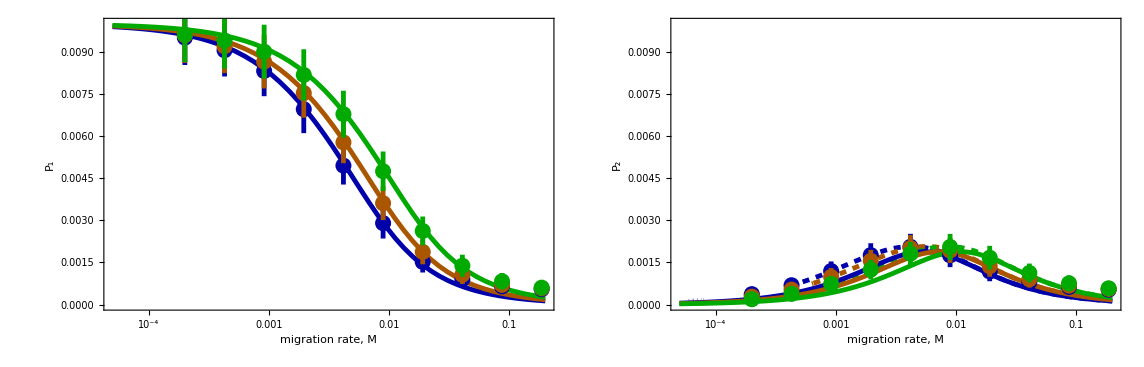

```mathematica
GraphicsRow[{plotViaGoodCodom,plotViaBadCodom},Spacings->{-10,0}]
```

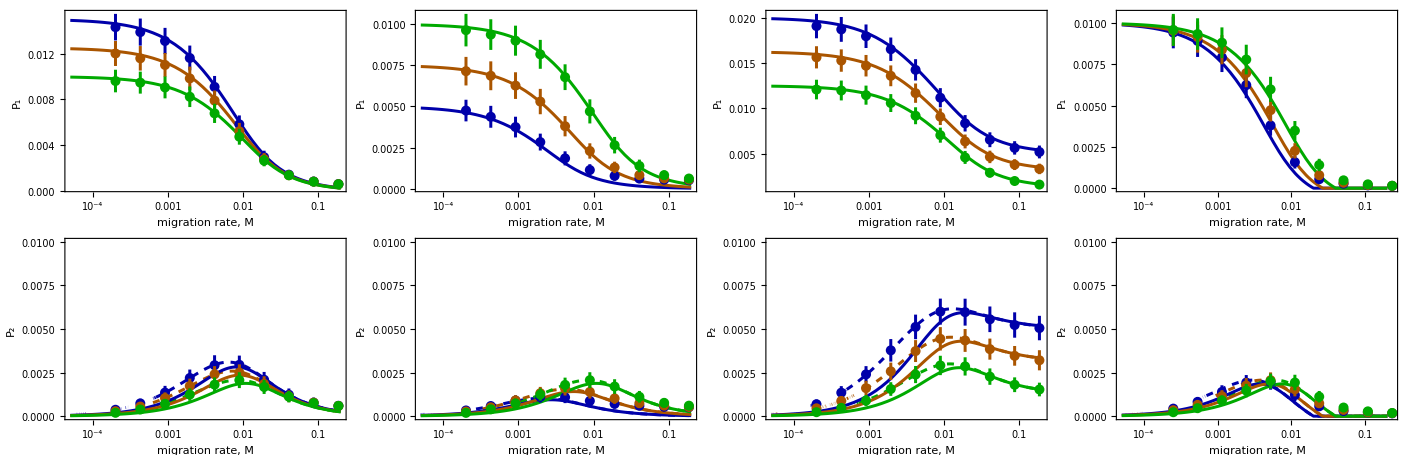

```mathematica
GraphicsGrid[{{plotViaGoodDom,plotViaGoodRec,plotGoodAsymSel,plotGoodAsymMig},
{plotViaBadDom,plotViaBadRec,plotViaBadAsymSel,plotViaBadAsymMig}},Spacings->{-10,0}]
```

### Female fecundity selection: Mutant injected in the favored patch

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsOffspringFecundity0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsOffspringFecundity0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsOffspringFecundity0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsOffspringFecundity0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

#### P_1 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_female_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemGoodCodom=Show[analytic,sims];
```

#### P_1 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_female_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.75,0.75,x,0],
PestGoodStart[myS1,myS2,0.75,0.75,x,1/3],
PestGoodStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemGoodDom=Show[analytic,sims];
```

#### P_1 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_female_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.25,0.25,x,0],
PestGoodStart[myS1,myS2,0.25,0.25,x,1/3],
PestGoodStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemGoodRec=Show[analytic,sims];
```

#### P_1 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_female_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotGoodAsymSel=Show[analytic,sims];
```

#### P_1 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_female_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pEst1/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst1/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst1/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotGoodAsymMig=Show[analytic,sims];
```

### Female fecundity selection: Mutant injected in the disfavored patch

#### P_2 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_female_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,0],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1/3],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadCodom=Show[analytic,sims];
```

#### P_2 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_female_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,0.75,0.75,x,0],
patch2Diff[myS1,myS2,0.75,0.75,x,1/3],
patch2Diff[myS1,myS2,0.75,0.75,x,1],
PestBadStart[myS1,myS2,0.75,0.75,x,0],
PestBadStart[myS1,myS2,0.75,0.75,x,1/3],
PestBadStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadDom=Show[analytic,sims];
```

#### P_2 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_female_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,0.25,0.25,x,0],
patch2Diff[myS1,myS2,0.25,0.25,x,1/3],
patch2Diff[myS1,myS2,0.25,0.25,x,1],
PestBadStart[myS1,myS2,0.25,0.25,x,0],
PestBadStart[myS1,myS2,0.25,0.25,x,1/3],
PestBadStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadRec=Show[analytic,sims];
```

#### P_2 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_female_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,0],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadAsymSel=Show[analytic,sims];
```

#### P_2 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_female_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pFix2/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pFix2/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pFix2/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1],
Max[0,pEst2/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst2/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst2/.effParsOffspringFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Max::nord: Invalid comparison with 0.000116878-4.23132×10^-17 ⅈ attempted.

Max::nord: Invalid comparison with 0.0000906002+3.85428×10^-16 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadAsymMig=Show[analytic,sims];
```

### Female fecundity selection: Figures

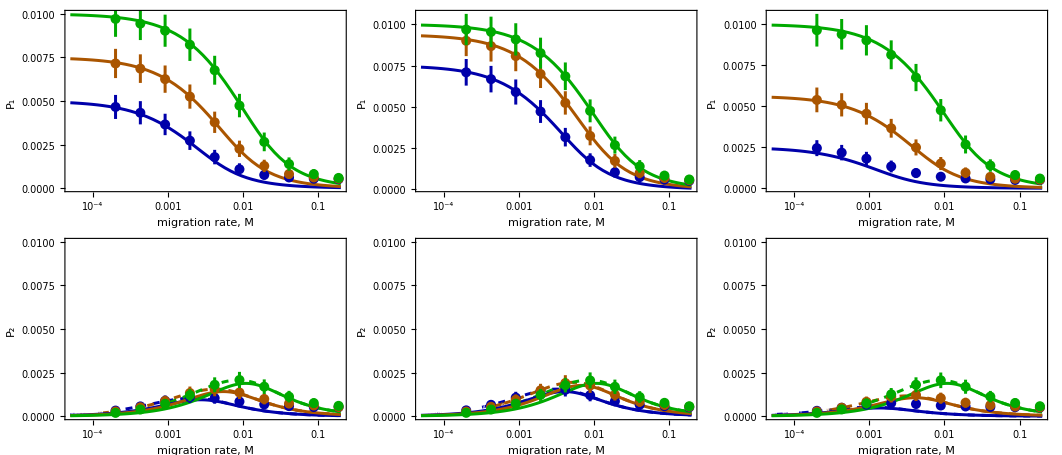

```mathematica
GraphicsGrid[{{plotFemGoodCodom,plotFemGoodDom,plotFemGoodRec},
{plotFemBadCodom,plotFemBadDom,plotFemBadRec}},Spacings->{-10,0}]
```

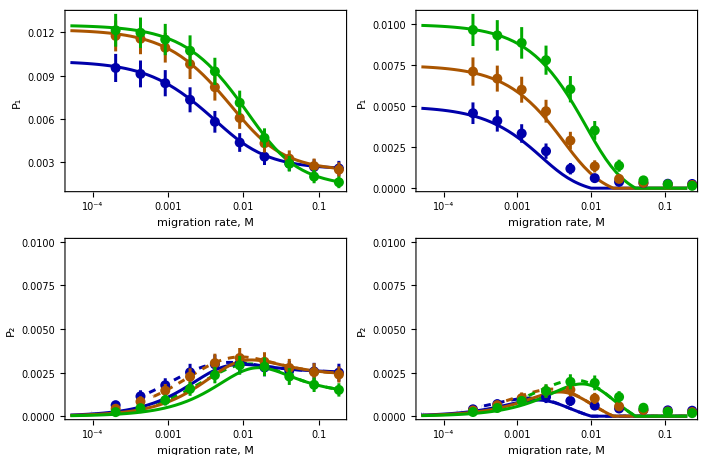

```mathematica
GraphicsGrid[{{plotGoodAsymSel,plotGoodAsymMig},{plotFemBadAsymSel,plotFemBadAsymMig}},Spacings->{-10,0}]
```

### Male component selection: Mutant injected in the favored patch

#### P_1 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_male_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsOffspringMale0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsOffspringMale0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst1/.effParsOffspringMale0/.{m1->m,m2->m}];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst2/.effParsOffspringMale0/.{m1->m,m2->m}];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Dashed,Thickness[0.006]}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodCodom=Show[analytic,sims];
```

#### P_1 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_male_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[myS1,myS2,0.75,0.75,x,0],
PestGoodStart[myS1,myS2,0.75,0.75,x,1/3],
PestGoodStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Dashed,Thickness[0.006]}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodDom=Show[analytic,sims];
```

#### P_1 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_male_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[myS1,myS2,0.25,0.25,x,0],
PestGoodStart[myS1,myS2,0.25,0.25,x,1/3],
PestGoodStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Dashed,Thickness[0.006]}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodRec=Show[analytic,sims];
```

#### P_1 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_male_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Dashed,Thickness[0.006]}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodAsymSel=Show[analytic,sims];
```

#### P_1 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_male_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
Max[0,pEst1/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst1/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst1/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1
]}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Dashed,Thickness[0.006]}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,All},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodAsymMig=Show[analytic,sims];
```

### Male component selection: Mutant injected in the disfavored patch

#### P_2 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_male_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,0],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1/3],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadCodom=Show[analytic,sims];
```

#### P_2 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_male_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,0.75,0.75,x,0],
patch2Diff[myS1,myS2,0.75,0.75,x,1/3],
patch2Diff[myS1,myS2,0.75,0.75,x,1],
PestBadStart[myS1,myS2,0.75,0.75,x,0],
PestBadStart[myS1,myS2,0.75,0.75,x,1/3],
PestBadStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadDom=Show[analytic,sims];
```

#### P_2 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_male_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[myS1,myS2,0.25,0.25,x,0],
patch2Diff[myS1,myS2,0.25,0.25,x,1/3],
patch2Diff[myS1,myS2,0.25,0.25,x,1],
PestBadStart[myS1,myS2,0.25,0.25,x,0],
PestBadStart[myS1,myS2,0.25,0.25,x,1/3],
PestBadStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadRec=Show[analytic,sims];
```

#### P_2 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_male_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,0],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadAsymSel=Show[analytic,sims];
```

#### P_2 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_male_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pFix2/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pFix2/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pFix2/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1],
Max[0,pEst2/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst2/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst2/.effParsOffspringMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],Dashed}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Max::nord: Invalid comparison with 0.000116878-4.23132×10^-17 ⅈ attempted.

Max::nord: Invalid comparison with 0.0000849124+1.39409×10^-17 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadAsymMig=Show[analytic,sims];
```

### Male component selection: Figures

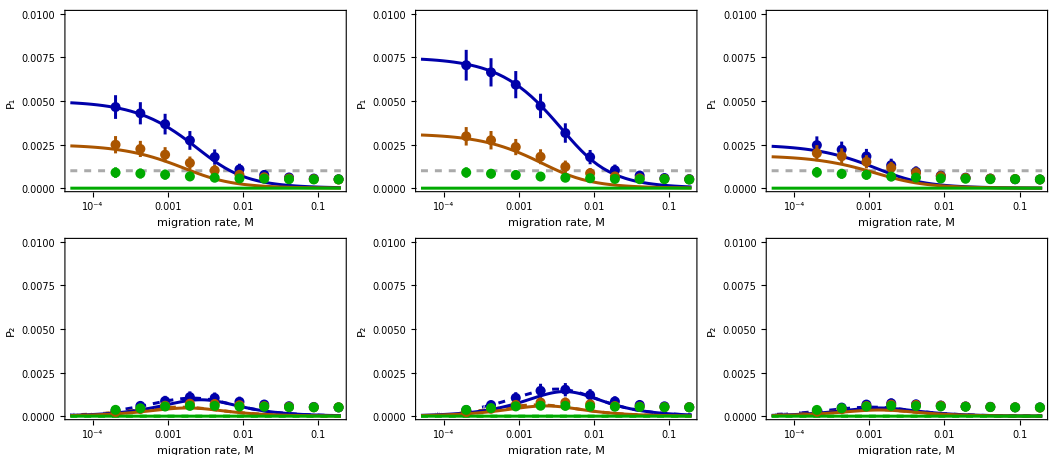

```mathematica
GraphicsGrid[{{plotMaleGoodCodom,plotMaleGoodDom,plotMaleGoodRec},
{plotMaleBadCodom,plotMaleBadDom,plotMaleBadRec}},Spacings->{-10,0}]
```

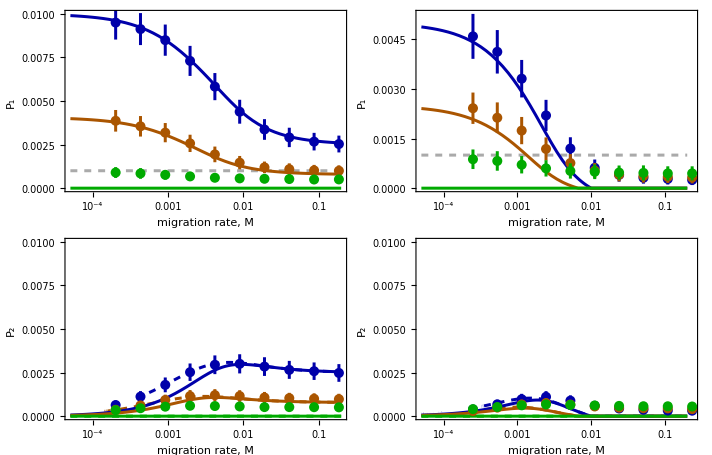

```mathematica
GraphicsGrid[{{plotMaleGoodAsymSel,plotMaleGoodAsymMig},{plotMaleBadAsymSel,plotMaleBadAsymMig}},Spacings->{-10,0}]
```

## 5. Comparison with simulations (gamete dispersal)

### Plotting parameters

```mathematica
myS1=0.01;myS2=-0.01;myHAdd=0.5;myKAdd=0.5;
```

```mathematica
yLim=1.75*myS1;xLim=0.2;
```

```mathematica
frameLab1={"migration rate, m","P_1"};
frameLab2={"migration rate, m","P_2"};
```

### Viability selection: Mutant injected in the favored patch

#### P_1 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_via_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsGameteVia0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsGameteVia0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsGameteVia0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsGameteVia0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,{0,yLim}},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaGoodCodom=Show[analytic,sims];
```

#### P_1 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_via_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.75,0.75,x,0],
PestGoodStart[myS1,myS2,0.75,0.75,x,1/3],
PestGoodStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaGoodDom=Show[analytic,sims];
```

#### P_1 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_via_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.25,0.25,x,0],
PestGoodStart[myS1,myS2,0.25,0.25,x,1/3],
PestGoodStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaGoodRec=Show[analytic,sims];
```

#### P_1 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_via_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaGoodAsymSel=Show[analytic,sims];
```

#### P_1 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_via_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pEst1/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst1/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst1/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
plotViaGoodAsymMig=Show[analytic,sims];
```

### Female component selection: Mutant injected in the favored patch

#### P_1 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_female_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsGameteFecundity0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsGameteFecundity0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsGameteFecundity0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsGameteFecundity0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemGoodCodom=Show[analytic,sims];
```

#### P_1 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_female_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.75,0.75,x,0],
PestGoodStart[myS1,myS2,0.75,0.75,x,1/3],
PestGoodStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemGoodDom=Show[analytic,sims];
```

#### P_1 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_female_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,0.25,0.25,x,0],
PestGoodStart[myS1,myS2,0.25,0.25,x,1/3],
PestGoodStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemGoodRec=Show[analytic,sims];
```

#### P_1 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_female_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,Axes->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
plotFemGoodAsymSel=Show[analytic,sims];
```

#### P_1 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_female_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pEst1/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst1/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst1/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemGoodAsymMig=Show[analytic,sims];
```

### Male component selection: Mutant injected in the favored patch

#### P_1 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_male_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsGameteMale0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsGameteMale0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst1/.effParsGameteMale0/.{m1->m,m2->m}];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst2/.effParsGameteMale0/.{m1->m,m2->m}];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodCodom=Show[analytic,sims];
```

#### P_1 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_male_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[myS1,myS2,0.75,0.75,x,0],
PestGoodStart[myS1,myS2,0.75,0.75,x,1/3],
PestGoodStart[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodDom=Show[analytic,sims];
```

#### P_1 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_male_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[myS1,myS2,0.25,0.25,x,0],
PestGoodStart[myS1,myS2,0.25,0.25,x,1/3],
PestGoodStart[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodRec=Show[analytic,sims];
```

#### P_1 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_male_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestGoodStart[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodAsymSel=Show[analytic,sims];
```

#### P_1 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/good_male_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
Max[0,pEst1/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst1/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst1/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006]}]},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleGoodAsymMig=Show[analytic,sims];
```

```mathematica
fig1=GraphicsGrid[{
{plotViaGoodCodom,plotViaGoodDom,plotViaGoodRec},
{plotFemGoodCodom,plotFemGoodDom,plotFemGoodRec},
{plotMaleGoodCodom,plotMaleGoodDom,plotMaleGoodRec}
},Spacings->{-15, 0}];
```

### Viability selection: Mutant injected in the disfavored patch

#### P_2 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_via_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsGameteVia0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsGameteVia0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsGameteVia0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsGameteVia0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,0],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,0],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadCodom=Show[analytic,sims];
```

#### P_2 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_via_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[myS1,myS2,0.75,0.75,x,0],
patch2Diff[myS1,myS2,0.75,0.75,x,0],
PestBadStart[myS1,myS2,0.75,0.75,x,1/3],
patch2Diff[myS1,myS2,0.75,0.75,x,1/3],
PestBadStart[myS1,myS2,0.75,0.75,x,1],
patch2Diff[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadDom=Show[analytic,sims];
```

#### P_2 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_via_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[myS1,myS2,0.25,0.25,x,0],
patch2Diff[myS1,myS2,0.25,0.25,x,0],
PestBadStart[myS1,myS2,0.25,0.25,x,1/3],
patch2Diff[myS1,myS2,0.25,0.25,x,1/3],
PestBadStart[myS1,myS2,0.25,0.25,x,1],
patch2Diff[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadRec=Show[analytic,sims];
```

#### P_2 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_via_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotViaBadAsymSel=Show[analytic,sims];
```

#### P_2 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_via_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pEst2/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pFix2/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst2/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pFix2/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pFix2/.effParsGameteVia0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Max::nord: Invalid comparison with 0.0000614352+4.59624×10^-16 ⅈ attempted.

Max::nord: Invalid comparison with 0.0000725363+7.75216×10^-16 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
plotViaBadAsymMig=Show[analytic,sims];
```

### Female component selection: Mutant injected in the disfavored patch

#### P_2 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_female_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsGameteFecundity0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsGameteFecundity0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsGameteFecundity0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsGameteFecundity0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,0],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,0],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadCodom=Show[analytic,sims];
```

#### P_2 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_female_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[myS1,myS2,0.75,0.75,x,0],
patch2Diff[myS1,myS2,0.75,0.75,x,0],
PestBadStart[myS1,myS2,0.75,0.75,x,1/3],
patch2Diff[myS1,myS2,0.75,0.75,x,1/3],
PestBadStart[myS1,myS2,0.75,0.75,x,1],
patch2Diff[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadDom=Show[analytic,sims];
```

#### P_2 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_female_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[myS1,myS2,0.25,0.25,x,0],
patch2Diff[myS1,myS2,0.25,0.25,x,0],
PestBadStart[myS1,myS2,0.25,0.25,x,1/3],
patch2Diff[myS1,myS2,0.25,0.25,x,1/3],
PestBadStart[myS1,myS2,0.25,0.25,x,1],
patch2Diff[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadRec=Show[analytic,sims];
```

#### P_2 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_female_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,Axes->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
plotFemGoodAsymSel=Show[analytic,sims];
```

#### P_2 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_female_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
Max[0,pEst2/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pFix2/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst2/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pFix2/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst2/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1],
Max[0,pFix2/.effParsGameteFecundity0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Max::nord: Invalid comparison with 0.0000602526-2.84806×10^-17 ⅈ attempted.

Max::nord: Invalid comparison with 0.0000709258-1.19959×10^-16 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotFemBadAsymMig=Show[analytic,sims];
```

### Male component selection: Mutant injected in the disfavored patch

#### P_2 for codominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_male_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsGameteMale0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsGameteMale0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst1/.effParsGameteMale0/.{m1->m,m2->m}];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst2/.effParsGameteMale0/.{m1->m,m2->m}];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,0],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,0],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1/3],
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,1],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadCodom=Show[analytic,sims];
```

#### P_2 for dominant case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_male_dom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestBadStart[myS1,myS2,0.75,0.75,x,0],
patch2Diff[myS1,myS2,0.75,0.75,x,0],
PestBadStart[myS1,myS2,0.75,0.75,x,1/3],
patch2Diff[myS1,myS2,0.75,0.75,x,1/3],
PestBadStart[myS1,myS2,0.75,0.75,x,1],
patch2Diff[myS1,myS2,0.75,0.75,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadDom=Show[analytic,sims];
```

#### P_2 for recessive case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_male_rec_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestBadStart[myS1,myS2,0.25,0.25,x,0],
patch2Diff[myS1,myS2,0.25,0.25,x,0],
PestBadStart[myS1,myS2,0.25,0.25,x,1/3],
patch2Diff[myS1,myS2,0.25,0.25,x,1/3],
PestBadStart[myS1,myS2,0.25,0.25,x,1],
patch2Diff[myS1,myS2,0.25,0.25,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadRec=Show[analytic,sims];
```

#### P_2 for asymmetric selection case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_male_asym_sel_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,0],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,0],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1/3],
PestBadStart[1.25*myS1,myS2,0.8,myKAdd,x,1],
patch2Diff[1.25*myS1,myS2,0.8,myKAdd,x,1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadAsymSel=Show[analytic,sims];
```

#### P_2 for asymmetric migration case

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_gamete_dispersal/bad_male_asym_mig_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
analytic=LogLinearPlot[{
1/1000,
Max[0,pEst2/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pFix2/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->0],
Max[0,pEst2/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pFix2/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1/3],
Max[0,pEst2/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1],
Max[0,pFix2/.effParsGameteMale0/.{m1->1.25x,m2->x}/.{s1->myS1,s2->myS2,h->0.5,k->0.5}/.F->1]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Lighter[Gray],Thickness[0.006],Dashed}],
Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->{All,yLim},Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab2];
```

Max::nord: Invalid comparison with 0.000059954+1.13349×10^-16 ⅈ attempted.

Max::nord: Invalid comparison with 0.0000226544-2.8401×10^-17 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
sims=ErrorListLogLinearPlot[{sigma00,sigma05,sigma10},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}]}];
```

```mathematica
plotMaleBadAsymMig=Show[analytic,sims];
```

```mathematica
fig2=GraphicsGrid[{
{plotViaBadCodom,plotViaBadDom,plotViaBadRec},
{plotFemBadCodom,plotFemBadDom,plotFemBadRec},
{plotMaleBadCodom,plotMaleBadDom,plotMaleBadRec}
},Spacings->{-15, 0}];
```

### Final figures

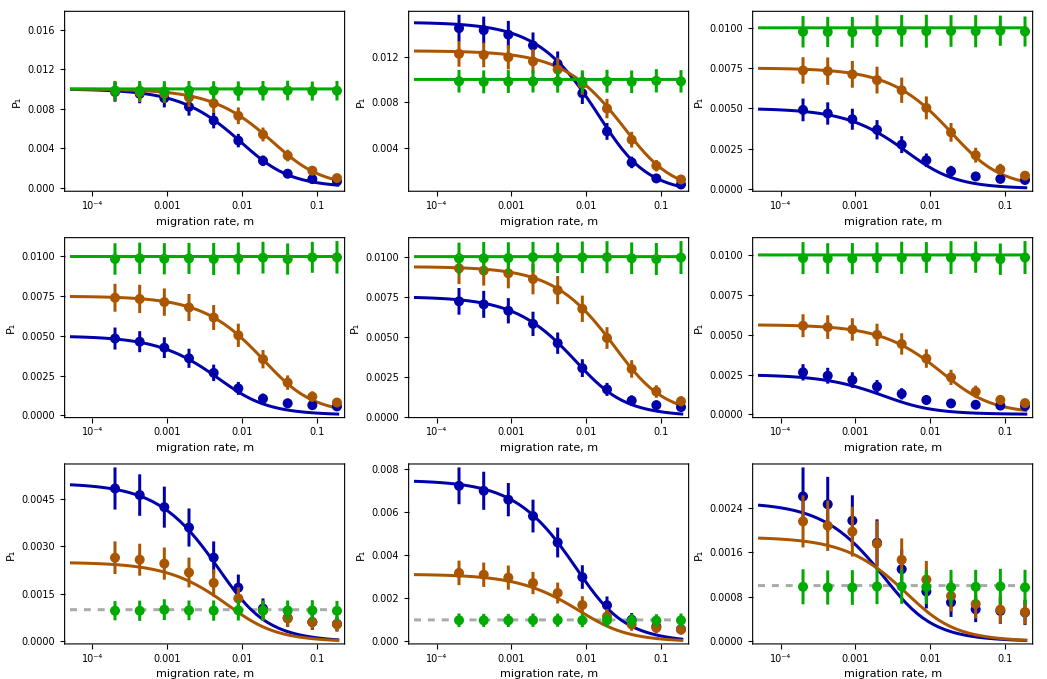

```mathematica
fig1
```

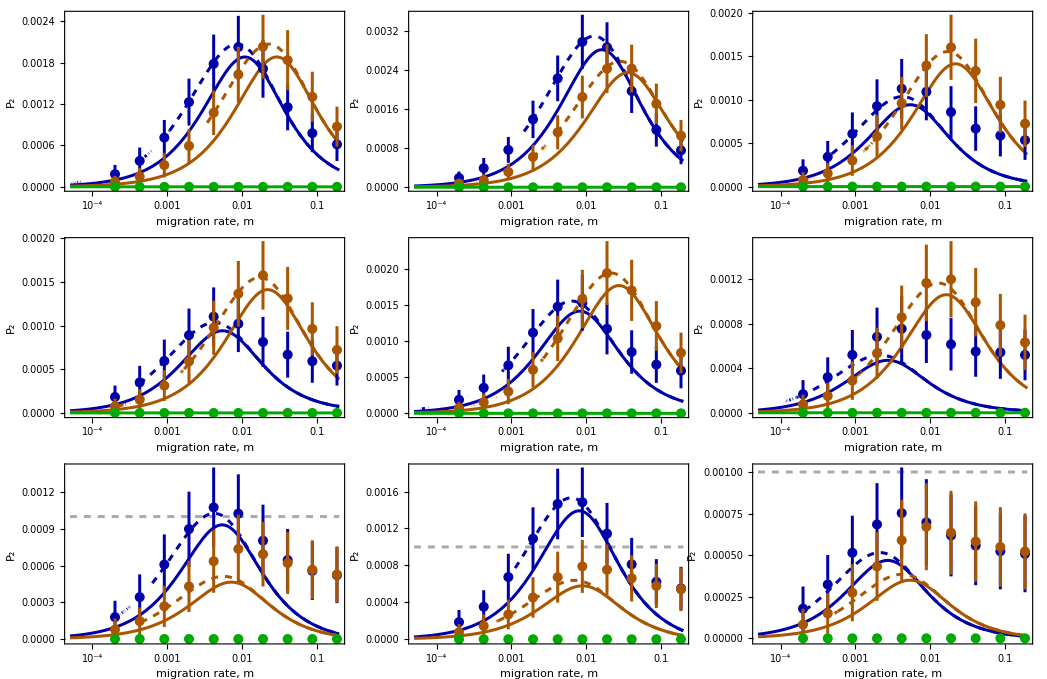

```mathematica
fig2
```

## 6. Accuracy of analytics across mating systems

```mathematica
goodRange={{0.025,1},{0.0002,0.02}};
```

### Mutant originates in the favored patch

```mathematica
myS1=0.01;myS2=-0.01;
```

```mathematica
frameLab1={"population inbreeding coefficient, F","P_1"};
frameLab2={"population inbreeding coefficient, F","P_2"};
```

```mathematica
mS1Par=0;
mS2Par=0.001;
mS3Par=0.005;
mS4Par=0.010;
mS5Par=0.025;
```

```mathematica
legendLabels=("M="<>ToString[#]&/@{mS1Par,mS2Par,mS3Par,mS4Par,mS5Par});
```

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_selfing_varied/good_via_selfing_varied_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
domPars={0.20,0.40,0.60,0.80};
```

```mathematica
mS1h1=Cases[d1,{_,domPars[[1]],mS1Par,_,_}];
mS1h1=Delete[mS1h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h1]}];
mS2h1=Cases[d1,{_,domPars[[1]],mS2Par,_,_}];
mS2h1=Delete[mS2h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h1]}];
mS3h1=Cases[d1,{_,domPars[[1]],mS3Par,_,_}];
mS3h1=Delete[mS3h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h1]}];
mS4h1=Cases[d1,{_,domPars[[1]],mS4Par,_,_}];
mS4h1=Delete[mS4h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h1]}];
mS5h1=Cases[d1,{_,domPars[[1]],mS5Par,_,_}];
mS5h1=Delete[mS5h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h1]}];
```

```mathematica
mS1h2=Cases[d1,{_,domPars[[2]],mS1Par,_,_}];
mS1h2=Delete[mS1h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h2]}];
mS2h2=Cases[d1,{_,domPars[[2]],mS2Par,_,_}];
mS2h2=Delete[mS2h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h2]}];
mS3h2=Cases[d1,{_,domPars[[2]],mS3Par,_,_}];
mS3h2=Delete[mS3h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h2]}];
mS4h2=Cases[d1,{_,domPars[[2]],mS4Par,_,_}];
mS4h2=Delete[mS4h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h2]}];
mS5h2=Cases[d1,{_,domPars[[2]],mS5Par,_,_}];
mS5h2=Delete[mS5h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h2]}];
```

```mathematica
mS1h3=Cases[d1,{_,domPars[[3]],mS1Par,_,_}];
mS1h3=Delete[mS1h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h3]}];
mS2h3=Cases[d1,{_,domPars[[3]],mS2Par,_,_}];
mS2h3=Delete[mS2h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h3]}];
mS3h3=Cases[d1,{_,domPars[[3]],mS3Par,_,_}];
mS3h3=Delete[mS3h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h3]}];
mS4h3=Cases[d1,{_,domPars[[3]],mS4Par,_,_}];
mS4h3=Delete[mS4h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h3]}];
mS5h3=Cases[d1,{_,domPars[[3]],mS5Par,_,_}];
mS5h3=Delete[mS5h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h3]}];
```

```mathematica
mS1h4=Cases[d1,{_,domPars[[4]],mS1Par,_,_}];
mS1h4=Delete[mS1h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h4]}];
mS2h4=Cases[d1,{_,domPars[[4]],mS2Par,_,_}];
mS2h4=Delete[mS2h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h4]}];
mS3h4=Cases[d1,{_,domPars[[4]],mS3Par,_,_}];
mS3h4=Delete[mS3h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h4]}];
mS4h4=Cases[d1,{_,domPars[[4]],mS4Par,_,_}];
mS4h4=Delete[mS4h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h4]}];
mS5h4=Cases[d1,{_,domPars[[4]],mS5Par,_,_}];
mS5h4=Delete[mS5h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h4]}];
```

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsOffspringVia0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsOffspringVia0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsOffspringVia0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsOffspringVia0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogPlot[{
PestGoodStart[myS1,myS2,domPars[[1]],domPars[[1]],mS1Par,x],
PestGoodStart[myS1,myS2,domPars[[1]],domPars[[1]],mS2Par,x],
PestGoodStart[myS1,myS2,domPars[[1]],domPars[[1]],mS3Par,x],
PestGoodStart[myS1,myS2,domPars[[1]],domPars[[1]],mS4Par,x],
PestGoodStart[myS1,myS2,domPars[[1]],domPars[[1]],mS5Par,x]
}
,{x,0,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h1,mS2h1,mS3h1,mS4h1,mS5h1
},Frame->True,ScalingFunctions->{None,"Log10"},
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot1a=Show[analytic,simsF];
```

```mathematica
analytic=LogPlot[{
PestGoodStart[myS1,myS2,domPars[[2]],domPars[[2]],mS1Par,x],
PestGoodStart[myS1,myS2,domPars[[2]],domPars[[2]],mS2Par,x],
PestGoodStart[myS1,myS2,domPars[[2]],domPars[[2]],mS3Par,x],
PestGoodStart[myS1,myS2,domPars[[2]],domPars[[2]],mS4Par,x],
PestGoodStart[myS1,myS2,domPars[[2]],domPars[[2]],mS5Par,x]
}
,{x,0,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h2,mS2h2,mS3h2,mS4h2,mS5h2
},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot2a=Show[analytic,simsF];
```

```mathematica
analytic=LogPlot[{
PestGoodStart[myS1,myS2,domPars[[3]],domPars[[3]],mS1Par,x],
PestGoodStart[myS1,myS2,domPars[[3]],domPars[[3]],mS2Par,x],
PestGoodStart[myS1,myS2,domPars[[3]],domPars[[3]],mS3Par,x],
PestGoodStart[myS1,myS2,domPars[[3]],domPars[[3]],mS4Par,x],
PestGoodStart[myS1,myS2,domPars[[3]],domPars[[3]],mS5Par,x]
}
,{x,0,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h3,mS2h3,mS3h3,mS4h3,mS5h3
},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot3a=Show[analytic,simsF];
```

```mathematica
analytic=LogPlot[{
PestGoodStart[myS1,myS2,domPars[[4]],domPars[[4]],mS1Par,x],
PestGoodStart[myS1,myS2,domPars[[4]],domPars[[4]],mS2Par,x],
PestGoodStart[myS1,myS2,domPars[[4]],domPars[[4]],mS3Par,x],
PestGoodStart[myS1,myS2,domPars[[4]],domPars[[4]],mS4Par,x],
PestGoodStart[myS1,myS2,domPars[[4]],domPars[[4]],mS5Par,x]
}
,{x,0.01,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h4,mS2h4,mS3h4,mS4h4,mS5h4
},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot4a=Show[analytic,simsF];
```

### Mutant originates in the disfavored patch

```mathematica
myS1=0.01;myS2=-0.01;
```

```mathematica
frameLab1={"population inbreeding coefficient, F","P_2"};
```

```mathematica
mS1Par=0;
mS2Par=0.001;
mS3Par=0.005;
mS4Par=0.010;
mS5Par=0.025;
```

```mathematica
legendLabels=("M="<>ToString[#]&/@{mS1Par,mS2Par,mS3Par,mS4Par,mS5Par});
```

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_selfing_varied/bad_via_selfing_varied_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
domPars={0.20,0.40,0.60,0.80};
```

```mathematica
mS1h1=Cases[d1,{_,domPars[[1]],mS1Par,_,_}];
mS1h1=Delete[mS1h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h1]}];
mS2h1=Cases[d1,{_,domPars[[1]],mS2Par,_,_}];
mS2h1=Delete[mS2h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h1]}];
mS3h1=Cases[d1,{_,domPars[[1]],mS3Par,_,_}];
mS3h1=Delete[mS3h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h1]}];
mS4h1=Cases[d1,{_,domPars[[1]],mS4Par,_,_}];
mS4h1=Delete[mS4h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h1]}];
mS5h1=Cases[d1,{_,domPars[[1]],mS5Par,_,_}];
mS5h1=Delete[mS5h1[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h1]}];
```

```mathematica
mS1h2=Cases[d1,{_,domPars[[2]],mS1Par,_,_}];
mS1h2=Delete[mS1h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h2]}];
mS2h2=Cases[d1,{_,domPars[[2]],mS2Par,_,_}];
mS2h2=Delete[mS2h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h2]}];
mS3h2=Cases[d1,{_,domPars[[2]],mS3Par,_,_}];
mS3h2=Delete[mS3h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h2]}];
mS4h2=Cases[d1,{_,domPars[[2]],mS4Par,_,_}];
mS4h2=Delete[mS4h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h2]}];
mS5h2=Cases[d1,{_,domPars[[2]],mS5Par,_,_}];
mS5h2=Delete[mS5h2[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h2]}];
```

```mathematica
mS1h3=Cases[d1,{_,domPars[[3]],mS1Par,_,_}];
mS1h3=Delete[mS1h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h3]}];
mS2h3=Cases[d1,{_,domPars[[3]],mS2Par,_,_}];
mS2h3=Delete[mS2h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h3]}];
mS3h3=Cases[d1,{_,domPars[[3]],mS3Par,_,_}];
mS3h3=Delete[mS3h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h3]}];
mS4h3=Cases[d1,{_,domPars[[3]],mS4Par,_,_}];
mS4h3=Delete[mS4h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h3]}];
mS5h3=Cases[d1,{_,domPars[[3]],mS5Par,_,_}];
mS5h3=Delete[mS5h3[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h3]}];
```

```mathematica
mS1h4=Cases[d1,{_,domPars[[4]],mS1Par,_,_}];
mS1h4=Delete[mS1h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS1h4]}];
mS2h4=Cases[d1,{_,domPars[[4]],mS2Par,_,_}];
mS2h4=Delete[mS2h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS2h4]}];
mS3h4=Cases[d1,{_,domPars[[4]],mS3Par,_,_}];
mS3h4=Delete[mS3h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS3h4]}];
mS4h4=Cases[d1,{_,domPars[[4]],mS4Par,_,_}];
mS4h4=Delete[mS4h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS4h4]}];
mS5h4=Cases[d1,{_,domPars[[4]],mS5Par,_,_}];
mS5h4=Delete[mS5h4[[#]],{{2},{3}}]&/@Table[i,{i,1,Length[mS5h4]}];
```

```mathematica
patch1Diff[s1_,s2_,h_,k_,m_,F_]=pFix1/.effParsOffspringVia0/.{m1->m,m2->m};
patch2Diff[s1_,s2_,h_,k_,m_,F_]=pFix2/.effParsOffspringVia0/.{m1->m,m2->m};
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[pEst1/.effParsOffspringVia0/.{m1->m,m2->m},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[pEst2/.effParsOffspringVia0/.{m1->m,m2->m},0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogPlot[{
PestBadStart[myS1,myS2,domPars[[1]],domPars[[1]],mS2Par,x],
PestBadStart[myS1,myS2,domPars[[1]],domPars[[1]],mS3Par,x],
PestBadStart[myS1,myS2,domPars[[1]],domPars[[1]],mS4Par,x],
PestBadStart[myS1,myS2,domPars[[1]],domPars[[1]],mS5Par,x],
patch2Diff[myS1,myS2,domPars[[1]],domPars[[1]],mS2Par,x],
patch2Diff[myS1,myS2,domPars[[1]],domPars[[1]],mS3Par,x],
patch2Diff[myS1,myS2,domPars[[1]],domPars[[1]],mS4Par,x],
patch2Diff[myS1,myS2,domPars[[1]],domPars[[1]],mS5Par,x]
}
,{x,0,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Magenta],Thickness[0.006],Dashed}],
Directive[{Darker[Red],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h1,mS2h1,mS3h1,mS4h1,mS5h1
},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot1b=Show[analytic,simsF];
```

```mathematica
analytic=LogPlot[{
PestBadStart[myS1,myS2,domPars[[2]],domPars[[2]],mS2Par,x],
PestBadStart[myS1,myS2,domPars[[2]],domPars[[2]],mS3Par,x],
PestBadStart[myS1,myS2,domPars[[2]],domPars[[2]],mS4Par,x],
PestBadStart[myS1,myS2,domPars[[2]],domPars[[2]],mS5Par,x],
patch2Diff[myS1,myS2,domPars[[2]],domPars[[2]],mS2Par,x],
patch2Diff[myS1,myS2,domPars[[2]],domPars[[2]],mS3Par,x],
patch2Diff[myS1,myS2,domPars[[2]],domPars[[2]],mS4Par,x],
patch2Diff[myS1,myS2,domPars[[2]],domPars[[2]],mS5Par,x]
}
,{x,0,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Magenta],Thickness[0.006],Dashed}],
Directive[{Darker[Red],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h2,mS2h2,mS3h2,mS4h2,mS5h2
},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot2b=Show[analytic,simsF];
```

```mathematica
analytic=LogPlot[{
PestBadStart[myS1,myS2,domPars[[3]],domPars[[3]],mS2Par,x],
PestBadStart[myS1,myS2,domPars[[3]],domPars[[3]],mS3Par,x],
PestBadStart[myS1,myS2,domPars[[3]],domPars[[3]],mS4Par,x],
PestBadStart[myS1,myS2,domPars[[3]],domPars[[3]],mS5Par,x],
patch2Diff[myS1,myS2,domPars[[3]],domPars[[3]],mS2Par,x],
patch2Diff[myS1,myS2,domPars[[3]],domPars[[3]],mS3Par,x],
patch2Diff[myS1,myS2,domPars[[3]],domPars[[3]],mS4Par,x],
patch2Diff[myS1,myS2,domPars[[3]],domPars[[3]],mS5Par,x]
}
,{x,0,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Magenta],Thickness[0.006],Dashed}],
Directive[{Darker[Red],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h3,mS2h3,mS3h3,mS4h3,mS5h3
},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot3b=Show[analytic,simsF];
```

```mathematica
analytic=LogPlot[{
PestBadStart[myS1,myS2,domPars[[4]],domPars[[4]],mS2Par,x],
PestBadStart[myS1,myS2,domPars[[4]],domPars[[4]],mS3Par,x],
PestBadStart[myS1,myS2,domPars[[4]],domPars[[4]],mS4Par,x],
PestBadStart[myS1,myS2,domPars[[4]],domPars[[4]],mS5Par,x],
patch2Diff[myS1,myS2,domPars[[4]],domPars[[4]],mS2Par,x],
patch2Diff[myS1,myS2,domPars[[4]],domPars[[4]],mS3Par,x],
patch2Diff[myS1,myS2,domPars[[4]],domPars[[4]],mS4Par,x],
patch2Diff[myS1,myS2,domPars[[4]],domPars[[4]],mS5Par,x]
}
,{x,0,1},
Exclusions->None,PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Green],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006]}],
Directive[{Darker[Red],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006],Dashed}],
Directive[{Darker[Magenta],Thickness[0.006],Dashed}],
Directive[{Darker[Red],Thickness[0.006],Dashed}]
},PlotLegends->False,
PlotRange->goodRange,Frame->True,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->frameLab1];
```

```mathematica
simsF=ErrorListLogPlot[{
mS1h4,mS2h4,mS3h4,mS4h4,mS5h4
},Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Medium,
PlotStyle->{
Directive[{Darker[Orange],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Green],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Magenta],Thickness[0.006],PointSize[0.02]}],
Directive[{Darker[Red],Thickness[0.006],PointSize[0.02]}]
},FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
```

```mathematica
plot4b=Show[analytic,simsF];
```

### Figures

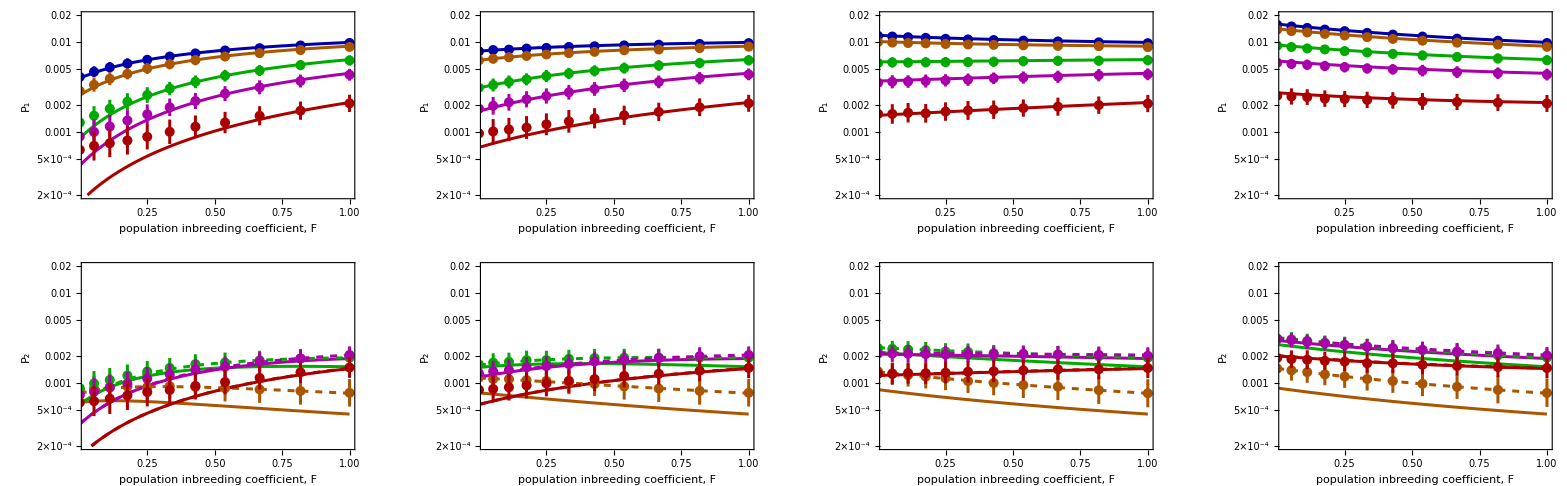

```mathematica
GraphicsGrid[{{plot1a,plot2a,plot3a,plot4a},{plot1b,plot2b,plot3b,plot4b}}]
```

## 7. Relation to previous studies

#### Comparison to older results

Note that s_1:=h_e s_1 and s_2:=k_e s_2

```mathematica
Assuming[{Subscript[s, 1]>0},FullSimplify[pEst1/.{Subscript[m, 12]->0,Subscript[m, 21]->0,Subscript[s, 2]->0,F->0}]] (* Haldane's result *)
```

2 s_1

```mathematica
Assuming[{Subscript[s, 1]>0},FullSimplify[pEst1/.{Subscript[m, 12]->0,Subscript[m, 21]->0,Subscript[s, 2]->0}] ](* Pollak-Sabran result *)
```

(2 s_1)/(1+F)

```mathematica
FullSimplify[pEst1/.{Subscript[m, 12]->1/2,Subscript[m, 21]->1/2}] (* randomly mixing subpopulations imply strong migration *);
Normal[Series[%/.{Subscript[s, 1]->Subscript[s, 1] υ,Subscript[s, 2]->Subscript[s, 2] υ},{υ,0,1}]]/.υ->1 (* next, approximate to weak selection to obtain Nagylaki *)
%/.F->0
```

(s_1+s_2)/(1+F)

s_1+s_2

```mathematica
Assuming[{Subscript[s, 1]>0,Subscript[s, 2]<0},FullSimplify[Normal[Series[pEst1/.{Subscript[m, 12]->m υ,Subscript[m, 21]->m υ,F->0},{υ,0,1}]]/.υ->1]] (* similar, but not identical, to Tomasini-Peischl result *)
```

-2 m+2 s_1

Strong migration limit for codominant mutation so s is replaced to

```mathematica
Assuming[{Subscript[s, 1]>0,Subscript[s, 2]<0,m>0},FullSimplify[Normal[Series[pEst1/.{Subscript[m, 12]->m,Subscript[m, 21]->m,Subscript[s, 1]-> (1/2+F-F/2)Subscript[s, 1],Subscript[s, 2]-> (1/2+F-F/2)Subscript[s, 2]},{m,∞,1}]]]] 
Assuming[{Subscript[s, 1]>0,Subscript[s, 2]<0,m>0},FullSimplify[Normal[Series[pEst2/.{Subscript[m, 12]->m,Subscript[m, 21]->m,Subscript[s, 1]-> (1/2+F-F/2)Subscript[s, 1],Subscript[s, 2]-> (1/2+F-F/2)Subscript[s, 2]},{m,∞,1}]]]]
```

1/8 (((1+F) s_1 (s_1-s_2))/m+4 (s_1+s_2))

-((1+F) (s_1-s_2) s_2)/(8 m)+1/2 (s_1+s_2)

What happens to P in the codominant cases? It is no longer independent of F as in Charlesworth’s model. Namely, in the limit of weak migration:

```mathematica
Assuming[{Subscript[s, 1]>0,Subscript[s, 2]<0},FullSimplify[Normal[Series[pEst1/.{Subscript[m, 12]->m υ,Subscript[m, 21]->m υ},{υ,0,1}]]/.υ->1]] 
Assuming[{Subscript[s, 1]>0,Subscript[s, 2]<0},FullSimplify[Normal[Series[pEst2/.{Subscript[m, 12]->m υ,Subscript[m, 21]->m υ},{υ,0,1}]]/.υ->1]]
```

-(2 (m-s_1))/(1+F)

(2 m s_1)/((1+F) (s_1-s_2))

```mathematica
Assuming[{Subscript[s, 1]>0,Subscript[s, 2]<0,m>0},FullSimplify[Normal[Series[pEst1/.{Subscript[m, 12]->m υ,Subscript[m, 21]->m υ},{υ,1,1}]]/.υ->1]] /.√(4 m^2+(Subscript[s, 1]-Subscript[s, 2])^2)->2m//FullSimplify
Assuming[{Subscript[s, 1]>0,Subscript[s, 2]<0,m>0},FullSimplify[Normal[Series[pEst2/.{Subscript[m, 12]->m υ,Subscript[m, 21]->m υ},{υ,1,1}]]/.υ->1]]
```

((4 m^2+(s_1-s_2) (2 m+s_1-s_2)) (2 m+s_1-s_2) (s_1+s_2))/(2 (1+F) (4 m^3+(3 m^2+(s_1-s_2) (2 m+s_1-s_2)) (s_1-s_2)))

-(m (4 m^2+(s_1-s_2) (s_1+√(4 m^2+(s_1-s_2)^2)-s_2)) (2 m-s_1-√(4 m^2+(s_1-s_2)^2)-s_2))/((1+F) (2 m^3+m^2 √(4 m^2+(s_1-s_2)^2)+s_1^2 √(4 m^2+(s_1-s_2)^2)+3 m^2 (s_1-s_2)+(s_1-s_2)^3-2 s_1 √(4 m^2+(s_1-s_2)^2) s_2+√(4 m^2+(s_1-s_2)^2) s_2^2))

```mathematica
Assuming[{0≤Subscript[hm, 1]≤1,Subscript[sm, 1]>0,0≤F≤1},pEst1/.Subscript[s, 1]->((-1+F) (-F+(-1+F) Subscript[hm, 1]) Subscript[sm, 1])/(2 (1+F))/.{Subscript[m, 12]->m,Subscript[m, 21]->m}/.m->0/.Subscript[s, 2]->0//FullSimplify] (* identical to Damgaard's result for male sexual selection *)
```

((-1+F) (-F+(-1+F) hm_1) sm_1)/(1+F)^2

```mathematica
Assuming[{0≤Subscript[hf, 1]≤1,Subscript[sf, 1]>0,0≤F≤1},pEst1/.Subscript[s, 1]->((F (3+F)-(-1+F^2) Subscript[hf, 1]) Subscript[sf, 1])/(2 (1+F))/.{Subscript[m, 12]->m,Subscript[m, 21]->m}/.m->0/.Subscript[s, 2]->0//FullSimplify] (* different than Damgaard's result for female fecundity selection *)
```

((F (3+F)-(-1+F^2) hf_1) sf_1)/(1+F)^2

In the case of codominant allele in both patches with symmetric selection and migration:

```mathematica
codom1=Assuming[{m>0},FullSimplify[pEst1/.{Subscript[s, 1]->s he,Subscript[s, 2]->-s ke,Subscript[m, 12]->m,Subscript[m, 21]->m}/.{h->1/2,k->1/2}]]
codom2=Assuming[{m>0},FullSimplify[pEst2/.{Subscript[s, 1]->s he,Subscript[s, 2]->-s ke,Subscript[m, 12]->m,Subscript[m, 21]->m}/.{h->1/2,k->1/2}]]
```

((-2 m+he s-ke s+√(4 m^2+(he+ke)^2 s^2)) ((he+ke) s+√(4 m^2+(he+ke)^2 s^2)) (4 m^2+(he+ke) s ((he+ke) s+√(4 m^2+(he+ke)^2 s^2))))/(2 (1+F) (2 m^3+(he+ke)^2 s^2 ((he+ke) s+√(4 m^2+(he+ke)^2 s^2))+m^2 (3 (he+ke) s+√(4 m^2+(he+ke)^2 s^2))))

-(m (2 m-he s+ke s-√(4 m^2+(he+ke)^2 s^2)) (4 m^2+(he+ke) s ((he+ke) s+√(4 m^2+(he+ke)^2 s^2))))/((1+F) (2 m^3+(he+ke)^2 s^2 ((he+ke) s+√(4 m^2+(he+ke)^2 s^2))+m^2 (3 (he+ke) s+√(4 m^2+(he+ke)^2 s^2))))

Monotonicity of establishment probabilities in F:

```mathematica
Reduce[Simplify[D[codom1,F]]<0&&1≥m≥0&&s>0&&1≥F≥0]
Reduce[Simplify[D[codom2,F]]<0&&1≥m≥0&&s>0&&1≥F≥0]
```

(ke<0&&((he<ke&&0<m≤1&&s>(-he m+ke m)/(he ke)&&0≤F≤1)||(ke≤he≤-ke&&0<m≤1&&s>0&&0≤F≤1)||(he>-ke&&0≤m≤1&&s>0&&0≤F≤1)))||(ke==0&&he>0&&0≤m≤1&&s>0&&0≤F≤1)||(ke>0&&((0<he<ke&&0≤m≤1&&s>(-he m+ke m)/(he ke)&&0≤F≤1)||(he≥ke&&0≤m≤1&&s>0&&0≤F≤1)))

(ke<0&&((he<ke&&0<m≤1&&s>(-he m+ke m)/(he ke)&&0≤F≤1)||(he≥ke&&0<m≤1&&s>0&&0≤F≤1)))||(ke==0&&he>0&&0<m≤1&&s>0&&0≤F≤1)||(ke>0&&((0<he<ke&&0<m≤1&&s>(-he m+ke m)/(he ke)&&0≤F≤1)||(he≥ke&&0<m≤1&&s>0&&0≤F≤1)))

Monotonicity of establishment probabilities in m:

```mathematica
Reduce[FullSimplify[D[codom1,m]]>0&&1≥m≥0&&s>0&&1≥F≥0]
Reduce[FullSimplify[D[codom2,m]]>0&&1≥m≥0&&s>0&&1≥F≥0]
```

(ke<0&&((he<0&&0<m≤1&&s>Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,1]&&0≤F≤1)||(0≤he<-ke&&0<m≤1&&s>0&&0≤F≤1)||(-ke<he<-(5 ke)/3&&0<m≤1&&Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,2]<s<Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,3]&&0≤F≤1)||(he==-(5 ke)/3&&0<m≤1&&Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,1]<s<Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,3]&&0≤F≤1)||(-(5 ke)/3<he<Root[432 ke^6+864 ke^5 #1+360 ke^4 #1^2+200 ke^3 #1^3+699 ke^2 #1^4+672 ke #1^5+191 #1^6&,2]&&0<m≤1&&Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,2]<s<Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,3]&&0≤F≤1)))||(ke>0&&((-ke<he≤Root[432 ke^6+864 ke^5 #1+360 ke^4 #1^2+200 ke^3 #1^3+699 ke^2 #1^4+672 ke #1^5+191 #1^6&,2]&&0<m≤1&&0<s<Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,3]&&0≤F≤1)||(Root[432 ke^6+864 ke^5 #1+360 ke^4 #1^2+200 ke^3 #1^3+699 ke^2 #1^4+672 ke #1^5+191 #1^6&,2]<he<0&&0<m≤1&&0<s<Root[48 he m^5+(-24 he^2 m^4+24 he ke m^4+36 ke^2 m^4) #1+(20 he^3 m^3+28 he^2 ke m^3+8 he ke^2 m^3) #1^2+(-5 he^4 m^2+27 he^2 ke^2 m^2+34 he ke^3 m^2+12 ke^4 m^2) #1^3+(2 he^5 m+6 he^4 ke m+6 he^3 ke^2 m+2 he^2 ke^3 m) #1^4+(he^5 ke+5 he^4 ke^2+10 he^3 ke^3+10 he^2 ke^4+5 he ke^5+ke^6) #1^5&,1]&&0≤F≤1)))

(ke<0&&((Root[191 ke^6+672 ke^5 #1+699 ke^4 #1^2+200 ke^3 #1^3+360 ke^2 #1^4+864 ke #1^5+432 #1^6&,1]<he<-(3 ke)/5&&0<m≤1&&Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,2]<s<Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,3]&&0≤F≤1)||(he==-(3 ke)/5&&0<m≤1&&Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,1]<s<Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,3]&&0≤F≤1)||(-(3 ke)/5<he<-ke&&0<m≤1&&Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,2]<s<Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,3]&&0≤F≤1)||(he>-ke&&0≤m≤1&&s>0&&0≤F≤1)))||(ke==0&&he>0&&0≤m≤1&&s>0&&0≤F≤1)||(ke>0&&((he<Root[191 ke^6+672 ke^5 #1+699 ke^4 #1^2+200 ke^3 #1^3+360 ke^2 #1^4+864 ke #1^5+432 #1^6&,1]&&0<m≤1&&0<s<Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,1]&&0≤F≤1)||(Root[191 ke^6+672 ke^5 #1+699 ke^4 #1^2+200 ke^3 #1^3+360 ke^2 #1^4+864 ke #1^5+432 #1^6&,1]≤he<-ke&&0<m≤1&&0<s<Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,3]&&0≤F≤1)||(he>0&&0≤m≤1&&s>Root[-48 ke m^5+(36 he^2 m^4+24 he ke m^4-24 ke^2 m^4) #1+(-8 he^2 ke m^3-28 he ke^2 m^3-20 ke^3 m^3) #1^2+(12 he^4 m^2+34 he^3 ke m^2+27 he^2 ke^2 m^2-5 ke^4 m^2) #1^3+(-2 he^3 ke^2 m-6 he^2 ke^3 m-6 he ke^4 m-2 ke^5 m) #1^4+(he^6+5 he^5 ke+10 he^4 ke^2+10 he^3 ke^3+5 he^2 ke^4+he ke^5) #1^5&,1]&&0≤F≤1)))

There is, however, some disagreement between the results of Tomasini and Peischl (2018) in the limit of weak migration. They report on page 888, P_(est,1)=2 s_1-m×(Abs(s_2))/(Abs(s_1-s_2)). We obtain 2 s_1-2m, and this expression approximates better the analytical solution when migration is weak (see Figure below):

#### Comparison to Tomasini-Peischl (2018) and Damgaard (2000)

Given that P_(est,k) can be negative when process is subcritical, we let P_(est,k):=max(P_(est,k),0):

```mathematica
he=F+(1-F)h;
ke=F+(1-F)k;
```

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[Simplify[pEst1/.{Subscript[m, 12]->m,Subscript[m, 21]->m}]/.{Subscript[s, 1]-> s1 he,Subscript[s, 2]->s2 ke},0];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[Simplify[pEst2/.{Subscript[m, 12]->m,Subscript[m, 21]->m}/.{Subscript[s, 1]-> s1 he,Subscript[s, 2]->s2 ke}],0];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
PestAvg[s1_,s2_,h_,k_,m_,F_,z_]=(1-z)patch1[s1,s2,h,k,m,F]+z patch2[s1,s2,h,k,m,F];
```

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_via_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00Good=Cases[d1,{0,_,_,_}];
sigma00Good=Delete[sigma00Good[[#]],1]&/@Table[i,{i,1,Length[sigma00Good]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
analyticGood=LogLinearPlot[{
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
Max[0.5*0.01(1+(0.5*0.01-(-0.01*0.5))/Sqrt[(2x)^2+(0.5*0.01-(-0.01*0.5))^2])+(-0.01*0.5)(2x)/Sqrt[(2x)^2+(0.5*0.01-(-0.01*0.5))^2],0],
patch1Diff[myS1,myS2,myHAdd,myKAdd,x,0]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Darker[Blue],Thickness[0.006]}],
Directive[{Darker[Orange],Thickness[0.006]}],
Directive[{Darker[Magenta],Thickness[0.006],Dashed}]
},PlotLegends->{"F=0, P_1","Tomasini-Peischl, Eqn. (4)","Sakamoto-Innan, Eqns. (4,5)"},
PlotRange->{All,{0,0.01}},Frame->True,ImageSize->Large,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->{"migration rate, M","P"}];
```

```mathematica
sims00Good=ErrorListLogLinearPlot[sigma00Good,Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Large,
PlotStyle->{
Directive[{Darker[Blue],Thickness[0.005],PointSize[0.02]}]
}];
```

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/bad_via_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00Bad=Cases[d1,{0,_,_,_}];
sigma00Bad=Delete[sigma00Bad[[#]],1]&/@Table[i,{i,1,Length[sigma00Bad]}];
```

```mathematica
analyticBad=LogLinearPlot[{
PestBadStart[myS1,myS2,myHAdd,myKAdd,x,0],
Max[0.5*0.01(2x)/Sqrt[(2x)^2+(0.5*0.01-(-0.01*0.5))^2]+(-0.01*0.5)(1-(0.5*0.01-(-0.01*0.5))/Sqrt[(2x)^2+(0.5*0.01-(-0.01*0.5))^2]),0],
patch2Diff[myS1,myS2,myHAdd,myKAdd,x,0]
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{
Directive[{Lighter[Blue],Thickness[0.006],Dashed}],
Directive[{Lighter[Orange],Thickness[0.006],Dashed}],
Directive[{Lighter[Magenta],Thickness[0.006],Dotted}]
},PlotLegends->{"F=0, P_2","Tomasini-Peischl, Eqn. (5)","Sakamoto-Innan, Eqns. (4,5)"},
PlotRange->{All,{0,0.01}},Frame->True,ImageSize->Large,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->{"migration rate, M","P"}];
```

```mathematica
sims00Bad=ErrorListLogLinearPlot[sigma00Bad,Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Large,
PlotStyle->{
Directive[{Lighter[Blue],Thickness[0.005],PointSize[0.02]}]
}];
```

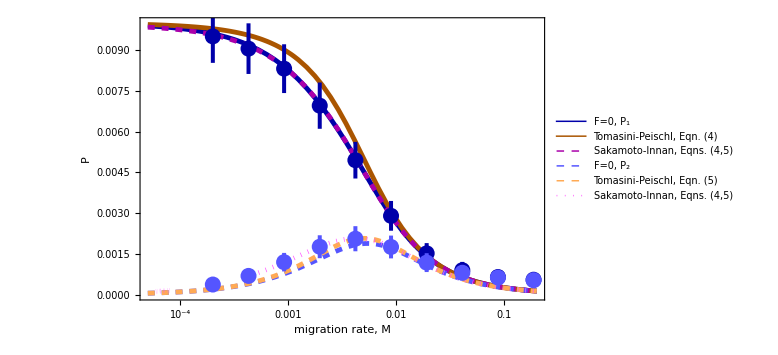

```mathematica
Show[analyticGood,sims00Good,analyticBad,sims00Bad]
```

We can also compare our prediction for P_est absent migration to that which Damgaard obtained for a single population:

```mathematica
d1=Delete[Import["/home/bogi/Desktop/incoming_projects/mating_system/simulation/selfing_sim/processed_data_offspring_dispersal/good_female_codom_processed.csv","CSV",FieldSeparators->","],1];
```

```mathematica
sigma00=Cases[d1,{0,_,_,_}];
sigma00=Delete[sigma00[[#]],1]&/@Table[i,{i,1,Length[sigma00]}];
sigma05=Cases[d1,{0.5,_,_,_}];
sigma05=Delete[sigma05[[#]],1]&/@Table[i,{i,1,Length[sigma05]}];
sigma10=Cases[d1,{1,_,_,_}];
sigma10=Delete[sigma10[[#]],1]&/@Table[i,{i,1,Length[sigma10]}];
```

```mathematica
{myS1,myS2,myHAdd,myKAdd}
```

{0.01,-0.01,0.5,0.5}

```mathematica
patch1[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst1/.{Subscript[m, 12]->m,Subscript[m, 21]->m}/.{Subscript[s, 1]->-((1+3 F) (-F+(-1+F) h) s1)/(2 (1+F)),Subscript[s, 2]->-((1+3 F) (-F+(-1+F) k) s2)/(2 (1+F))}];
patch2[s1_,s2_,h_,k_,m_,F_]=Max[0,pEst2/.{Subscript[m, 12]->m,Subscript[m, 21]->m}/.{Subscript[s, 1]-> -((1+3 F) (-F+(-1+F) h) s1)/(2 (1+F)),Subscript[s, 2]->-((1+3 F) (-F+(-1+F) k) s2)/(2 (1+F))}];
```

```mathematica
PestGoodStart[s1_,s2_,h_,k_,m_,F_]=patch1[s1,s2,h,k,m,F];
PestBadStart[s1_,s2_,h_,k_,m_,F_]=patch2[s1,s2,h,k,m,F];
```

```mathematica
analytic=LogLinearPlot[{
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,0],
(1+2 F/(1+F))((1-F)h+F)/(1+F)s1/.{F->0,h->myHAdd,s1->myS1},
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1/3],
(1+2 F/(1+F))((1-F)h+F)/(1+F)s1/.{F->1/3,h->myHAdd,s1->myS1},
PestGoodStart[myS1,myS2,myHAdd,myKAdd,x,1],
(1+2 F/(1+F))((1-F)h+F)/(1+F)s1/.{F->1,h->myHAdd,s1->myS1}
}
,{x,0.00005,xLim},
Exclusions->None,PlotStyle->{Directive[{Darker[Blue],Thickness[0.006]}],Directive[{Darker[Blue],Thickness[0.006],Dashed}],
Directive[{Darker[Orange],Thickness[0.006]}],Directive[{Darker[Orange],Thickness[0.006],Dashed}],
Directive[{Darker[Green],Thickness[0.006]}],Directive[{Darker[Green],Thickness[0.006],Dashed}]},PlotLegends->{"F=0, P_1","F=0 (Damgaard 2000)","F=1/3, P_1","F=1/3 (Damgaard 2000)","F=1, P_1","F=1 (Damgaard 2000)"},
PlotRange->{All,{0,0.01}},Frame->True,ImageSize->Large,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],FrameLabel->{"migration rate, M","P_1"}];
```

```mathematica
sims00=ErrorListLogLinearPlot[sigma00,Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Large,
PlotStyle->{
Directive[{Darker[Blue],Thickness[0.005],PointSize[0.02]}],Directive[{Darker[Yellow],Thickness[0.005],PointSize[0.02]}]
}];
sims05=ErrorListLogLinearPlot[sigma05,Frame->True,
FrameLabel->None,FrameTicks->None,ImageSize->Large,
PlotStyle->{
Directive[{Darker[Orange],Thickness[0.005],PointSize[0.02]}],Directive[{Darker[Yellow],Thickness[0.005],PointSize[0.02]}]
}];
sims10=ErrorListLogLinearPlot[sigma10,Frame->True,FrameLabel->None,FrameTicks->None,ImageSize->Large,
PlotStyle->{
Directive[{Darker[Green],Thickness[0.005],PointSize[0.02]}],Directive[{Darker[Yellow],Thickness[0.005],PointSize[0.02]}]
}];
```

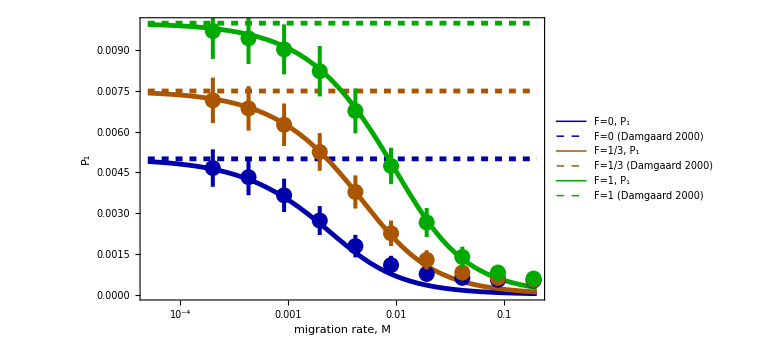

```mathematica
Show[analytic,sims00,sims05,sims10]
```

## 8. Decomposing the effects of self-fertilization on P

```mathematica
pointsNb=10;
```

```mathematica
femSym=FromCharacterCode[Interpreter["HexInteger"]["2640"]];
maleSym=FromCharacterCode[Interpreter["HexInteger"]["2642"]];
```

### Consequences of selfing on the probability of establishment with offspring dispersal

```mathematica
myMig=0.01;myS1=0.01;myS2=-0.01;myF=0.00;
```

#### Viability selection

```mathematica
axesLabel={"Dominance in favored patch (h_1^{o})","Dominance in disfavored patch (h_2^{o})"};
```

```mathematica
{effMig1,effMig2,effS1,effS2}=effParsOffspringVia0[[All,2]]/.{m1->m,m2->m}
```

{m,m,(F+h-F h) s1,(F+k-F k) s2}

```mathematica
probEst1=pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
probEst2=pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
```

```mathematica
(* Subscript[P, est,i](Subscript[h, e]) *)
beta1HE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta1KE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
beta2HE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta2KE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
(* Subscript[P, est,i](Subscript[N, e]) *)
beta1NE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2NE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

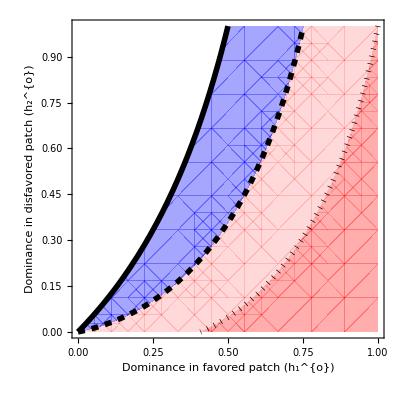

```mathematica
pl0=RegionPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.35]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl3=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≤-beta1KE[myS1,myS2,h,k,myMig,myF]),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl0,bordersMainPlot,bordersGoodPlot,bordersStrongBadPlot]
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

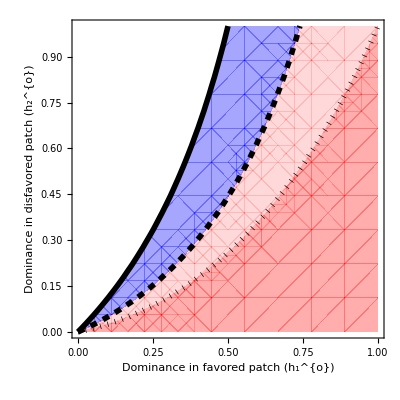

```mathematica
pl0=RegionPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.35]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl3=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≤-beta2KE[myS1,myS2,h,k,myMig,myF]),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl0,bordersMainPlot,bordersGoodPlot,bordersStrongBadPlot]
```

#### Fecundity selection

```mathematica
axesLabel={"Dominance in favored patch (h_1^{♀})","Dominance in disfavored patch (h_2^{♀})"};
```

```mathematica
{effMig1,effMig2,effS1,effS2}=effParsOffspringFecundity0[[All,2]]/.{m1->m,m2->m}
```

{m,m,-((1+3 F) (F (-1+h)-h) s1)/(2 (1+F)),-((1+3 F) (F (-1+k)-k) s2)/(2 (1+F))}

```mathematica
probEst1=pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
probEst2=pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
```

```mathematica
(* Subscript[P, est,i](Subscript[h, e]) *)
beta1HE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta1KE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
beta2HE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta2KE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
(* Subscript[P, est,i](Subscript[N, e]) *)
beta1NE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2NE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

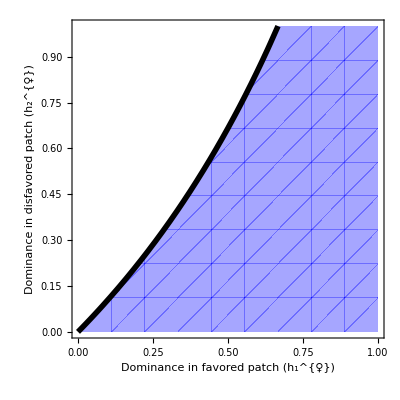

```mathematica
pl0=RegionPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.35]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl3=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≤-beta1KE[myS1,myS2,h,k,myMig,myF]),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl0,bordersMainPlot,bordersGoodPlot]
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-beta2KE[myS1,myS2,h,k,myMig,myF]),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

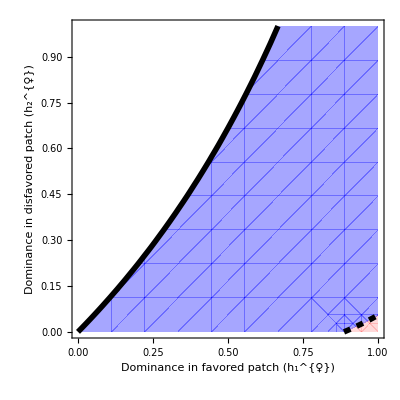

```mathematica
pl0=RegionPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.35]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl3=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≤-beta2KE[myS1,myS2,h,k,myMig,myF]),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl0,bordersMainPlot,bordersGoodPlot]
```

#### Male sexual selection

```mathematica
axesLabel={"Dominance in favored patch (h_1^{♂})","Dominance in disfavored patch (h_2^{♂})"};
```

```mathematica
{effMig1,effMig2,effS1,effS2}=effParsOffspringMale0[[All,2]]/.{m1->m,m2->m}
```

{m,m,((-1+F) (F (-1+h)-h) s1)/(2 (1+F)),((-1+F) (F (-1+k)-k) s2)/(2 (1+F))}

```mathematica
probEst1=pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
probEst2=pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
```

```mathematica
(* Subscript[P, est,i](Subscript[h, e]) *)
beta1HE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta1KE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
beta2HE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta2KE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
(* Subscript[P, est,i](Subscript[N, e]) *)
beta1NE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2NE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

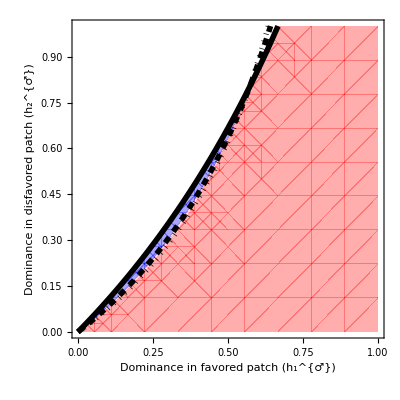

```mathematica
pl0=RegionPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.35]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl3=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≤-beta1KE[myS1,myS2,h,k,myMig,myF]),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl0,bordersMainPlot,bordersGoodPlot,bordersStrongBadPlot]
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

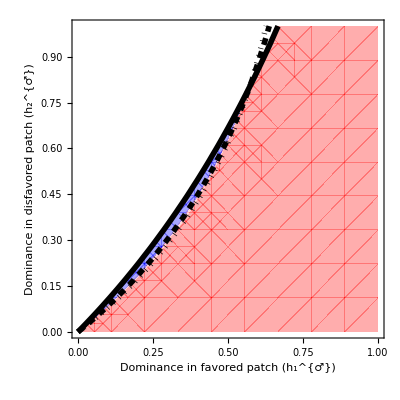

```mathematica
pl0=RegionPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.35]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl3=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≤-beta2KE[myS1,myS2,h,k,myMig,myF]),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl0,bordersMainPlot,bordersGoodPlot,bordersStrongBadPlot]
```

### Consequences of selfing on the probability of establishment with male gamete dispersal

```mathematica
myMig=0.005;myS1=0.001;myS2=-0.001;myF=0.00;
```

#### Viability selection

```mathematica
axesLabel={"Dominance in favored patch (h_1^{o})","Dominance in disfavored patch (h_2^{o})"};
```

```mathematica
{effMig1,effMig2,effS1,effS2}=effParsGameteVia0[[All,2]]/.{m1->m,m2->m}
```

{((-1+F) m (1+h s1))/(2 (1+F) (-1+F (-1+h) s1-h s1)),((-1+F) m (1+k s2))/(2 (1+F) (-1+F (-1+k) s2-k s2)),(F+h-F h) s1,(F+k-F k) s2}

```mathematica
probEst1=pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
probEst2=pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i (includes the effect on M̃)
3. Re-parameterize s_i and set F=0 (cancels the effect on h̃)

```mathematica
beta1ME[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2ME[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i and set F=0 (cancels the effect on M̃)
3. Re-parameterize s_i and set F=0 for either s_1 or s_2 (cancels the effect on OverTilde[h_1] or OverTilde[h_2], respectively)

```mathematica
(* Subscript[P, est,i](Subscript[h, e]) *)
beta1HE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta1KE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
beta2HE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta2KE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i and set F=0 (cancels the effect on M̃)
3. Re-parameterize s_i and set F=0 for either s_1 or s_2 (cancels the effect on OverTilde[h_1] or OverTilde[h_2], respectively)

```mathematica
(* Subscript[P, est,i](Subscript[N, e]) *)
beta1NE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.{Subscript[m, 12]->(effMig1/.F->0),Subscript[m, 21]->(effMig2/.F->0)}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2NE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.{Subscript[m, 12]->(effMig1/.F->0),Subscript[m, 21]->(effMig2/.F->0)}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,DotDashed}];
bordersStongGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

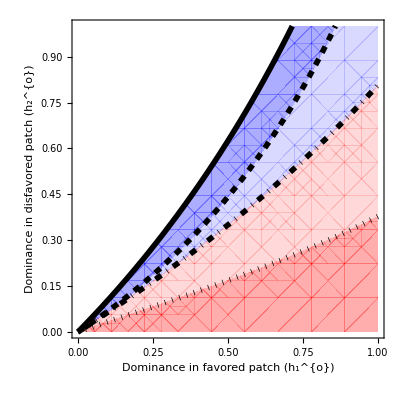

```mathematica
pl0=RegionPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl3=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl4=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl4,pl0,bordersMainPlot,bordersGoodPlot,bordersStongGoodPlot,bordersStrongBadPlot]
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,DotDashed}];
bordersStongGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

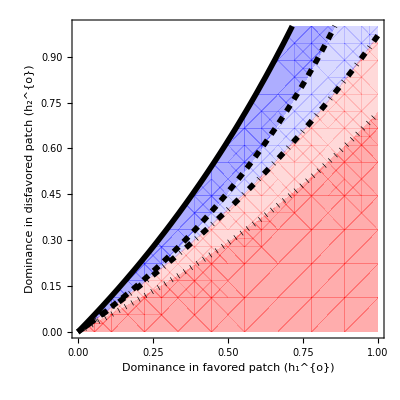

```mathematica
pl0=RegionPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl2=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl3=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
pl4=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl4,pl0,bordersMainPlot,bordersGoodPlot,bordersStongGoodPlot,bordersStrongBadPlot]
```

#### Female component selection

```mathematica
axesLabel={"Dominance in favored patch (h_1^{♀})","Dominance in disfavored patch (h_2^{♀})"};
```

```mathematica
{effMig1,effMig2,effS1,effS2}=effParsGameteFecundity0[[All,2]]/.{m1->m,m2->m}
```

{((-1+F) m)/(-2 (1+F)+(1+3 F) (F (-1+h)-h) s1),((-1+F) m)/(-2 (1+F)+(1+3 F) (F (-1+k)-k) s2),-((1+3 F) (F (-1+h)-h) s1)/(2 (1+F)),-((1+3 F) (F (-1+k)-k) s2)/(2 (1+F))}

```mathematica
probEst1=pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
probEst2=pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i (includes the effect on M̃)
3. Re-parameterize s_i and set F=0 (cancels the effect on h̃)

```mathematica
beta1ME[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2ME[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i and set F=0 (cancels the effect on M̃)
3. Re-parameterize s_i and set F=0 for either s_1 or s_2 (cancels the effect on OverTilde[h_1] or OverTilde[h_2], respectively)

```mathematica
(* Subscript[P, est,i](Subscript[h, e]) *)
beta1HE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta1KE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
beta2HE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta2KE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i and set F=0 (cancels the effect on M̃)
3. Re-parameterize s_i and set F=0 for either s_1 or s_2 (cancels the effect on OverTilde[h_1] or OverTilde[h_2], respectively)

```mathematica
(* Subscript[P, est,i](Subscript[N, e]) *)
beta1NE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.{Subscript[m, 12]->(effMig1/.F->0),Subscript[m, 21]->(effMig2/.F->0)}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2NE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.{Subscript[m, 12]->(effMig1/.F->0),Subscript[m, 21]->(effMig2/.F->0)}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,DotDashed}];
bordersStongGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

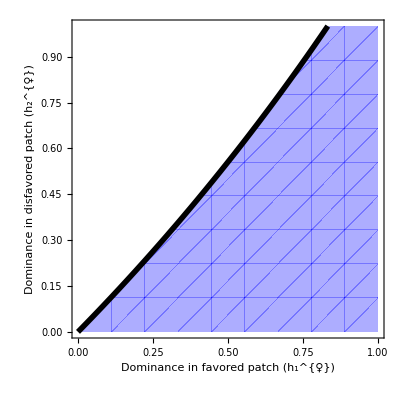

```mathematica
pl0=RegionPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]];
pl2=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl3=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]
];
pl4=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl4,pl0,bordersMainPlot,bordersGoodPlot,bordersStongGoodPlot]
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,DotDashed}];
bordersStongGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

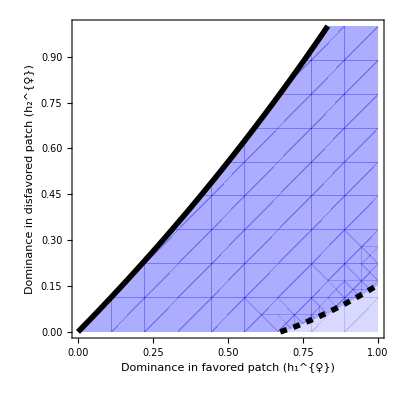

```mathematica
pl0=RegionPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]];
pl2=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl3=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]
];
pl4=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl4,pl0,bordersMainPlot,bordersGoodPlot,bordersStongGoodPlot]
```

#### Male component selection

```mathematica
axesLabel={"Dominance in favored patch (h_1^{♂})","Dominance in disfavored patch (h_2^{♂})"};
```

```mathematica
{effMig1,effMig2,effS1,effS2}=effParsGameteMale0[[All,2]]/.{m1->m,m2->m}
```

{((-1+F) m (-1+F (-1+k) s2-k s2))/(2+h (s1-m s1)+k m s2+F^2 ((-1+h+m-h m) s1+(-1+k) m s2)+F (2+(-1+2 h) (-1+m) s1+m s2-2 k m s2)),((-1+F) m (-1+F (-1+h) s1-h s1))/(2+2 F+F m s1-F^2 m s1+h m s1-2 F h m s1+F^2 h m s1-(-1+F) (F (-1+k)-k) (-1+m) s2),((-1+F) (-(F (-1+h)-h) (-1+m) s1+(F (-1+k)-k) m s2))/(2 (1+F)),((-1+F) ((F (-1+h)-h) m s1-(F (-1+k)-k) (-1+m) s2))/(2 (1+F))}

```mathematica
probEst1=pEst1/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
probEst2=pEst2/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1),Subscript[s, 2]->(effS2)};
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i (includes the effect on M̃)
3. Re-parameterize s_i and set F=0 (cancels the effect on h̃)

```mathematica
beta1ME[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2ME[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i and set F=0 (cancels the effect on M̃)
3. Re-parameterize s_i and set F=0 for either s_1 or s_2 (cancels the effect on OverTilde[h_1] or OverTilde[h_2], respectively)

```mathematica
(* Subscript[P, est,i](Subscript[h, e]) *)
beta1HE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta1KE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

```mathematica
beta2HE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->effS1,Subscript[s, 2]->(effS2/.F->0)},F];
beta2KE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.F->0/.{Subscript[m, 12]->effMig1,Subscript[m, 21]->effMig2}/.F->0/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->effS2},F];
```

1. Take P_(est,i) and set F=0, without re-parameterizing m_i and s_i (cancels the effect on N_e)
2. Re-parameterize m_i and set F=0 (cancels the effect on M̃)
3. Re-parameterize s_i and set F=0 for either s_1 or s_2 (cancels the effect on OverTilde[h_1] or OverTilde[h_2], respectively)

```mathematica
(* Subscript[P, est,i](Subscript[N, e]) *)
beta1NE[s1_,s2_,h_,k_,m_,F_]=D[pEst1/.{Subscript[m, 12]->(effMig1/.F->0),Subscript[m, 21]->(effMig2/.F->0)}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
beta2NE[s1_,s2_,h_,k_,m_,F_]=D[pEst2/.{Subscript[m, 12]->(effMig1/.F->0),Subscript[m, 21]->(effMig2/.F->0)}/.{Subscript[s, 1]->(effS1/.F->0),Subscript[s, 2]->(effS2/.F->0)},F];
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,DotDashed}];
bordersStongGoodPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]==-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

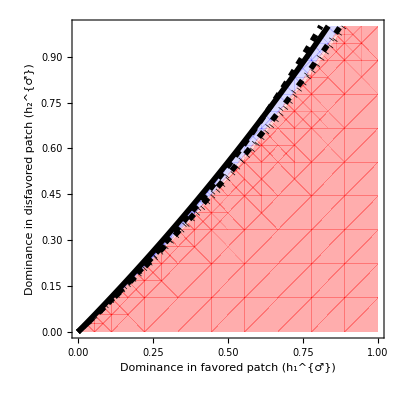

```mathematica
pl0=RegionPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]];
pl2=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≥-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl3=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]
];
pl4=RegionPlot[(beta1HE[myS1,myS2,h,k,myMig,myF]+beta1ME[myS1,myS2,h,k,myMig,myF]≤-(beta1KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl4,pl0,bordersMainPlot,bordersGoodPlot,bordersStongGoodPlot,bordersStrongBadPlot]
```

```mathematica
bordersMainPlot=ContourPlot[{(probEst2/.{s1->myS1,s2->myS2,m->myMig,F->myF})==0},{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black}];
bordersGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,DotDashed}];
bordersStongGoodPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15,Thick,Bold],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dashed}];
bordersStrongBadPlot=ContourPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]==-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15],PlotLegends->None,PlotTheme->"Monochrome",ContourStyle->{Thickness[0.01],Black,Dotted}];
```

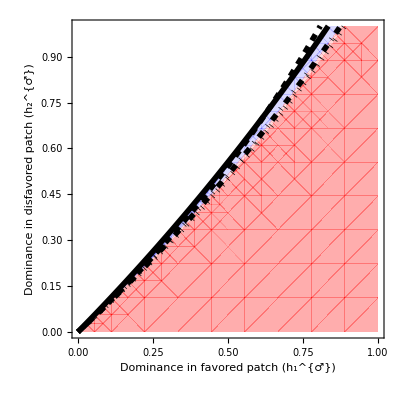

```mathematica
pl0=RegionPlot[{(probEst1/.{s1->myS1,s2->myS2,m->myMig,F->myF})<0},{h,0,1},{k,0,1},PlotStyle->Directive[White],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl1=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]];
pl2=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≥-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta1NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Blue,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,
FrameStyle->Directive[Black,FontSize->15,Thick,Bold]];
pl3=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF]+beta2NE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.15]],BoundaryStyle->None,PlotPoints->pointsNb,
Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15]
];
pl4=RegionPlot[(beta2HE[myS1,myS2,h,k,myMig,myF]+beta2ME[myS1,myS2,h,k,myMig,myF]≤-(beta2KE[myS1,myS2,h,k,myMig,myF])),{h,0,1},{k,0,1},PlotStyle->Directive[Red,Opacity[0.20]],BoundaryStyle->None,PlotPoints->pointsNb,Frame->True,FrameLabel->axesLabel,FrameStyle->Directive[Black,FontSize->15,Thick,Bold]
];
Show[pl2,pl1,pl3,pl4,pl0,bordersMainPlot,bordersGoodPlot,bordersStongGoodPlot,bordersStrongBadPlot]
```

## 9. Numerical exploration of critical migration rates for local adaptation

```mathematica
viaLabel={"Dominance in favored patch (h_1^{o})","Dominance in disfavored patch (h_2^{o})"};
femLabel={"Dominance in favored patch (h_1^{♀})","Dominance in disfavored patch (h_2^{♀})"};
maleLabel={"Dominance in favored patch (h_1^{♂})","Dominance in disfavored patch (h_2^{♂})"};
```

Here I’ve only reused the full results of the main notebook to explore how selfing rate does affect the maintenance of protected polymorphism.
Here I’ve copied the results and just made a change of variables.
For simplicity I only consider symmetric migration rates and equal contribution of the two patches.
The migration rate for which the probability of emergence is 0 is computed for both alleles. From this the critical migration rate is taken (note that we need to play with conditions to ensure that the correct m is chosesn).

```mathematica
P1[F_,m12_,m21_,s1_,s2_]=((-Subscript[m, 12]+Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))) (-Subscript[m, 12]-Subscript[m, 21]+Subscript[s, 1]+Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))) (Subscript[m, 12]^2-Subscript[m, 12] (-2 Subscript[m, 21]+2 Subscript[s, 1]-2 Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2]) (Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))))/(2 (1+F) (-Subscript[m, 12]^3+Subscript[m, 12]^2 (2 Subscript[m, 21]+3 Subscript[s, 1]-3 Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2 (Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))-Subscript[m, 12] (Subscript[m, 21] (3 Subscript[s, 1]-3 Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))+(Subscript[s, 1]-Subscript[s, 2]) (3 Subscript[s, 1]-3 Subscript[s, 2]+2 √(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))))))/.{Subscript[m, 12]->m12,Subscript[m, 21]->m21,Subscript[s, 1]->s1,Subscript[s, 2]->s2};
P2[F_,m12_,m21_,s1_,s2_]=(Subscript[m, 12] (-Subscript[m, 12]-Subscript[m, 21]+Subscript[s, 1]+Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))) (Subscript[m, 12]^2-Subscript[m, 12] (-2 Subscript[m, 21]+2 Subscript[s, 1]-2 Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2]) (Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))))/((1+F) (-Subscript[m, 12]^3+Subscript[m, 12]^2 (2 Subscript[m, 21]+3 Subscript[s, 1]-3 Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2 (Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))-Subscript[m, 12] (Subscript[m, 21] (3 Subscript[s, 1]-3 Subscript[s, 2]+√(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2])))+(Subscript[s, 1]-Subscript[s, 2]) (3 Subscript[s, 1]-3 Subscript[s, 2]+2 √(Subscript[m, 12]^2+(Subscript[m, 21]+Subscript[s, 1]-Subscript[s, 2])^2+2 Subscript[m, 12] (Subscript[m, 21]-Subscript[s, 1]+Subscript[s, 2]))))))/.{Subscript[m, 12]->m12,Subscript[m, 21]->m21,Subscript[s, 1]->s1,Subscript[s, 2]->s2};
```

Here it is the sum of the average of the two probabilities of emergence.
Strictly speaking -s1/(1+s1) and -s2/(1+s2) should be used but for weak selection it is roughly -s1 and -s2 (both are given in the main text)

```mathematica
PA[F_,m_,h1_,s1_,h2_,s2_]=Simplify[(P1[F,m,m,(h1+F-h1 F)s1,(h2+F-h2 F)s2]+P2[F,m,m,(h1+F-h1 F)s1,(h2+F-h2 F)s2])/2];
```

```mathematica
Pa[F_,m_,h1_,s1_,h2_,s2_]=Simplify[PA[F,m,1-h1,-s1/(1+s1),1-h2,-s2/(1+s2)]];
```

Values of m for which PA and Pa are 0:

```mathematica
MA[F_,h1_,s1_,h2_,s2_]=Simplify[m/.Solve[PA[F,m,h1,s1,h2,s2]==0,m][[1]]]
Ma[F_,h1_,s1_,h2_,s2_]=Simplify[MA[F,1-h1,-s1/(1+s1),1-h2,-s2/(1+s2)]]
```

-((F (-1+h1)-h1) (F (-1+h2)-h2) s1 s2)/(F (-1+h1) s1-h1 s1+F (-1+h2) s2-h2 s2)

-((1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/(s1+s2+(-1+F) h2 s2+(2+(-1+F) h2) s1 s2+(-1+F) h1 s1 (1+s2))

For F=0 we retrieve the same conditions as in Yeaman and Otto (with our parameterization):

```mathematica
Simplify[MA[0,h1,s1,h2,s2]]
Simplify[Ma[0,h1,s1,h2,s2]]
```

(h1 h2 s1 s2)/(h1 s1+h2 s2)

((-1+h1) (-1+h2) s1 s2)/((-1+h2) s2+s1 (-1+h1-2 s2+h1 s2+h2 s2))

Starting from Bulmer’s condition and extension of Yeaman and Otto, the condition for which M_c>1 is:
(((1+h1 s1)(1-F)+F)((1+h2 s2)(1-F)+F))/((1+s1)(1+s2)) >1. Otherwise, if we assume s1 > -s2 > 0. Ma is lower than MA.
So the critical migration for seed migration is:

```mathematica
Mc[F_,h1_,s1_,h2_,s2_]=If[(((1+h1 s1)(1-F)+F)((1+h2 s2)(1-F)+F))/((1+s1)(1+s2))>1,1,((1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/((-1+h2-F h2) s2+s1 (-1+h1-F h1+(-1+F) (h1+h2+2 (-1+F) h1 h2) s2))]
```

If[((F+(1-F) (1+h1 s1)) (F+(1-F) (1+h2 s2)))/((1+s1) (1+s2))>1,1,((1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/((-1+h2-F h2) s2+s1 (-1+h1-F h1+(-1+F) (h1+h2+2 (-1+F) h1 h2) s2))]

Similarly we can get the critical migration rate for pollen migration. This is the same equation as above that it give the effective critical migration rate so we have to use the correction, which corresponds to multiplying by ((2 (1+F) (-1+F (-1+h1) s1-h1 s1))/((-1+F) (1+h1 s1)))

```mathematica
mc[F_,h1_,s1_,h2_,s2_]=If[(((1+h1 s1)(1-F)+F)((1+h2 s2)(1-F)+F))/((1+s1)(1+s2))>1,1,((2 (1+F) (-1+F (-1+h1) s1-h1 s1))/((-1+F) (1+h1 s1)))((1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/((-1+h2-F h2) s2+s1 (-1+h1-F h1+(-1+F) (h1+h2+2 (-1+F) h1 h2) s2))]
```

If[((F+(1-F) (1+h1 s1)) (F+(1-F) (1+h2 s2)))/((1+s1) (1+s2))>1,1,((2 (1+F) (-1+F (-1+h1) s1-h1 s1)) ((1+(-1+F) h1) (1+(-1+F) h2) s1 s2))/(((-1+F) (1+h1 s1)) ((-1+h2-F h2) s2+s1 (-1+h1-F h1+(-1+F) (h1+h2+2 (-1+F) h1 h2) s2)))]

### Critical migration rate: seed migration

Here are some plots of the regions where critical migration rates is higher under selfing than outcrossing as a function of dominance for different levels of selection asymmetry. For each region, an example of plot of M_c as a function of F is given.

#### Viability

```mathematica
(((1+h1 s1)(1-F)+F)((1+h2 s2)(1-F)+F))/((1+s1)(1+s2))/.F->0
```

((1+h1 s1) (1+h2 s2))/((1+s1) (1+s2))

```mathematica
cond[h1_,s1_,h2_,s2_]=((1+h1 s1) (1+h2 s2))/((1+s1) (1+s2));
```

```mathematica
McdF[h1_,s1_,h2_,s2_]=Simplify[D[((1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/((-1+h2-F h2) s2+s1 (-1+h1-F h1+(-1+F) (h1+h2+2 (-1+F) h1 h2) s2)),F]/.F->0];
```

```mathematica
G1=RegionPlot[{True,cond[h1,0.01,h2,-0.01]<1,Mc[1,h1,0.0100,h2,-0.01]/Mc[0,h1,0.0100,h2,-0.01]>1,McdF[h1,0.01,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,
Frame->True,FrameLabel->viaLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G2=Show[RegionPlot[{True,cond[h1,0.05,h2,-0.01]<1,Mc[1,h1,0.02,h2,-0.01]/Mc[0,h1,0.02,h2,-0.01]>1,McdF[h1,0.02,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->viaLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]],Graphics[{PointSize[0.02],Point[{{0.4,0.4},{0.55,0.4},{0.65,0.4},{0.9,0.4}}]}]];
G3=RegionPlot[{True,cond[h1,0.1,h2,-0.01]<1,Mc[1,h1,0.05,h2,-0.01]/Mc[0,h1,0.05,h2,-0.01]>1,McdF[h1,0.05,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->viaLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G4=LogPlot[{Mc[F,0.4,0.02,0.4,-0.01],Mc[F,0.55,0.02,0.4,-0.01],Mc[F,0.65,0.02,0.4,-0.01],Mc[F,0.9,0.02,0.4,-0.01]},{F,0,1},PlotRange->{{0,1},{0.01,1}},PlotStyle->{Lighter[Blue,0.3],Lighter[Blue,0.65],Lighter[Red,0.65],Lighter[Red,0.3]},AspectRatio->1,Frame->True,FrameLabel->{"Inbreeding coefficient (F)","Critical migration rate (M_c)"},
FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
```

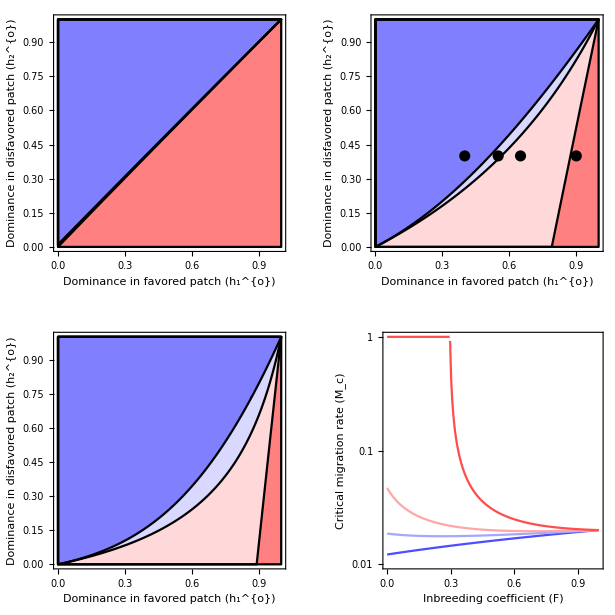

```mathematica
GraphicsGrid[{{G1,G2},{G3,G4}}]
```

#### Female fecundity

```mathematica
McFem[F_,h1_,s1_,h2_,s2_]=Simplify[Mc[F,h1,s1(1+(2F)/(1+F))/2,h2,s2(1+(2F)/(1+F))/2]];
```

```mathematica
Simplify[D[((1+3 F) (1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/(-2 (1+F-h2+F^2 h2) s2+s1 (-2-h2 s2+6 F^3 h1 h2 s2+2 F (-1+h1 (-1+h2) s2-h2 s2)+h1 (2-s2+2 h2 s2)+F^2 (3 h2 s2+h1 (-2+3 s2-10 h2 s2)))),F]/.F->0]
```

-(s1 s2 (-2 (-2+h1) (-1+h2)^2 s2+s1 (4+h1^2 (4+h2 (-2+s2))+h2 (-2+s2)+h1 (-8-4 h2 (-1+s2)+s2+h2^2 s2))))/(2 (-1+h2) s2+s1 (-2-h2 s2+h1 (2-s2+2 h2 s2)))^2

```mathematica
McdFFem[h1_,s1_,h2_,s2_]=-(s1 s2 (-2 (-2+h1) (-1+h2)^2 s2+s1 (4+h1^2 (4+h2 (-2+s2))+h2 (-2+s2)+h1 (-8-4 h2 (-1+s2)+s2+h2^2 s2))))/(2 (-1+h2) s2+s1 (-2-h2 s2+h1 (2-s2+2 h2 s2)))^2;
```

```mathematica
G1=RegionPlot[{True,cond[h1,0.0101,h2,-0.01]<1,McFem[1,h1,0.0101,h2,-0.01]/McFem[0,h1,0.0101,h2,-0.01]>1,McdFFem[h1,0.01,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,
Frame->True,FrameLabel->femLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G2=RegionPlot[{True,cond[h1,0.05,h2,-0.01]<1,McFem[1,h1,0.02,h2,-0.01]/McFem[0,h1,0.02,h2,-0.01]>1,McdFFem[h1,0.02,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->femLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G3=RegionPlot[{True,cond[h1,0.1,h2,-0.01]<1,McFem[1,h1,0.05,h2,-0.01]/McFem[0,h1,0.05,h2,-0.01]>1,McdFFem[h1,0.05,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->femLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G4=LogPlot[{McFem[F,0.4,0.02,0.4,-0.01],McFem[F,0.6,0.02,0.4,-0.01],McFem[F,0.65,0.02,0.4,-0.01],McFem[F,0.9,0.02,0.4,-0.01]},{F,0,1},PlotRange->{{0,1},{0.005,1}},PlotStyle->{Lighter[Blue,0.3],Lighter[Blue,0.65],Lighter[Red,0.65],Lighter[Red,0.3]},AspectRatio->1,Frame->True,FrameLabel->{"Inbreeding coefficient (F)","Critical migration rate (M_c)"},
FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
```

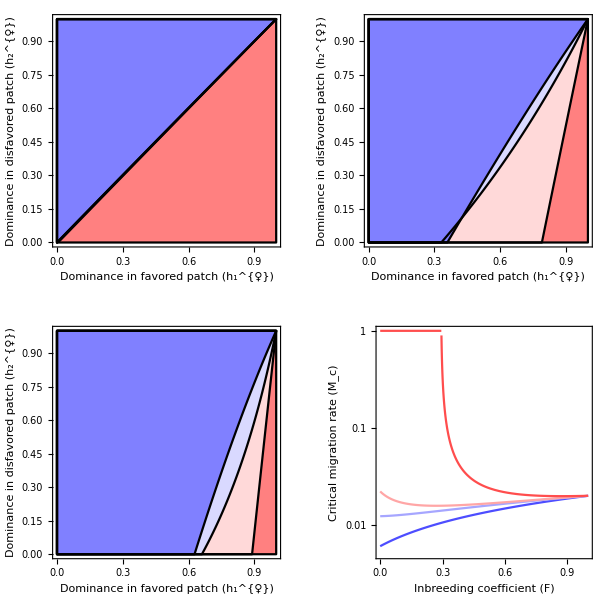

```mathematica
GraphicsGrid[{{G1,G2},{G3,G4}}]
```

#### Male fecundity

```mathematica
McMale[F_,h1_,s1_,h2_,s2_]=Simplify[Mc[F,h1,s1(1-(2F)/(1+F))/2,h2,s2(1-(2F)/(1+F))/2]];
```

```mathematica
Simplify[D[((-1+F) (1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/(2 (1+F-h2+F^2 h2) s2+s1 (2+h2 s2+2 F^3 h1 h2 s2+h1 (-2+s2-2 h2 s2)+F (2-2 h2 s2+2 h1 (-1+3 h2) s2)+F^2 (h2 s2+h1 (2+s2-6 h2 s2)))),F]/.F->0]
```

-(s1 s2 (2 (-2+3 h1) (-1+h2)^2 s2+s1 (-4+h2 (6+s2)+h1 (8+s2+h2^2 s2-4 h2 (3+s2))+h1^2 (-4+h2 (6+s2)))))/(2 (-1+h2) s2+s1 (-2-h2 s2+h1 (2-s2+2 h2 s2)))^2

```mathematica
McdFMale[h1_,s1_,h2_,s2_]=-(s1 s2 (2 (-2+3 h1) (-1+h2)^2 s2+s1 (-4+h2 (6+s2)+h1 (8+s2+h2^2 s2-4 h2 (3+s2))+h1^2 (-4+h2 (6+s2)))))/(2 (-1+h2) s2+s1 (-2-h2 s2+h1 (2-s2+2 h2 s2)))^2;
```

```mathematica
G1=RegionPlot[{True,cond[h1,0.0101,h2,-0.01]<1,McdFMale[h1,0.01,h2,-0.01]>0&&cond[h1,0.0101,h2,-0.01]<1},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,
Frame->True,FrameLabel->maleLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G2=RegionPlot[{True,cond[h1,0.05,h2,-0.01]<1,McdFMale[h1,0.02,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->maleLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G3=RegionPlot[{True,cond[h1,0.1,h2,-0.01]<1,McdFMale[h1,0.05,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->maleLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G4=LogPlot[{McMale[F,0.4,0.02,0.9,-0.01],McMale[F,0.8,0.02,0.7,-0.01],McMale[F,0.9,0.02,0.7,-0.01]},{F,0,1},PlotRange->{{0,1},{0.0001,1}},PlotStyle->{Lighter[Blue,0.65],Lighter[Red,0.65],Lighter[Red,0.3]},AspectRatio->1,Frame->True,FrameLabel->{"Inbreeding coefficient (F)","Critical migration rate (M_c)"},
FrameStyle->Directive[Black,FontSize->12,Bold,Thick]];
```

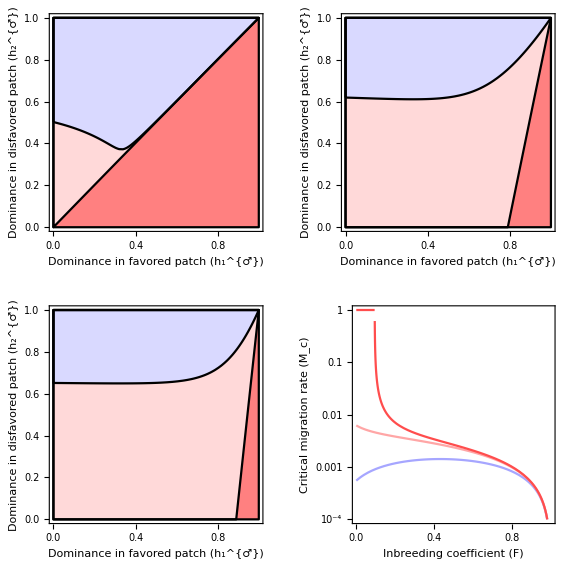

```mathematica
GraphicsGrid[{{G1,G2},{G3,G4}}]
```

### Critical migration rate : pollen migration

Here I give only the example for viability selection

#### Viability

```mathematica
(((1+h1 s1)(1-F)+F)((1+h2 s2)(1-F)+F))/((1+s1)(1+s2))/.F->0
```

((1+h1 s1) (1+h2 s2))/((1+s1) (1+s2))

```mathematica
cond[h1_,s1_,h2_,s2_]=((1+h1 s1) (1+h2 s2))/((1+s1) (1+s2));
```

```mathematica
mcdF[h1_,s1_,h2_,s2_]=Simplify[D[((2 (1+F) (-1+F (-1+h1) s1-h1 s1))/((-1+F) (1+h1 s1)))((1+(-1+F) h1) (1+(-1+F) h2) s1 s2)/((-1+h2-F h2) s2+s1 (-1+h1-F h1+(-1+F) (h1+h2+2 (-1+F) h1 h2) s2)),F]/.F->0];
```

```mathematica
G1=RegionPlot[{True,cond[h1,0.0101,h2,-0.01]<1,mcdF[h1,0.01,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,
Frame->True,FrameLabel->viaLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G2=Show[RegionPlot[{True,cond[h1,0.05,h2,-0.01]<1,mcdF[h1,0.02,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->viaLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]],Graphics[{PointSize[0.02],Point[{{0.4,0.4},{0.65,0.4},{0.9,0.4}}]}]];
G3=RegionPlot[{True,cond[h1,0.1,h2,-0.01]<1,mcdF[h1,0.05,h2,-0.01]>0},{h1,0,1},{h2,0,1},
PlotStyle->{Lighter[Red,0.5],Lighter[Red,0.85],Lighter[Blue,0.5]},BoundaryStyle->Black,Frame->True,FrameLabel->viaLabel,FrameStyle->Directive[Black,FontSize->12,Thick,Bold]];
G4=LogPlot[{mc[F,0.4,0.02,0.4,-0.01],mc[F,0.65,0.02,0.4,-0.01],mc[F,0.9,0.02,0.4,-0.01]},{F,0,1},PlotRange->{{0,1},{0.01,1}},PlotStyle->{Lighter[Blue,0.3],Lighter[Red,0.65],Lighter[Red,0.3]},AspectRatio->1,Frame->True,FrameLabel->{"Inbreeding coefficient (F)","Critical migration rate (M_c)"},
FrameStyle->Directive[Black,FontSize->12,Bold,Thick]];
```

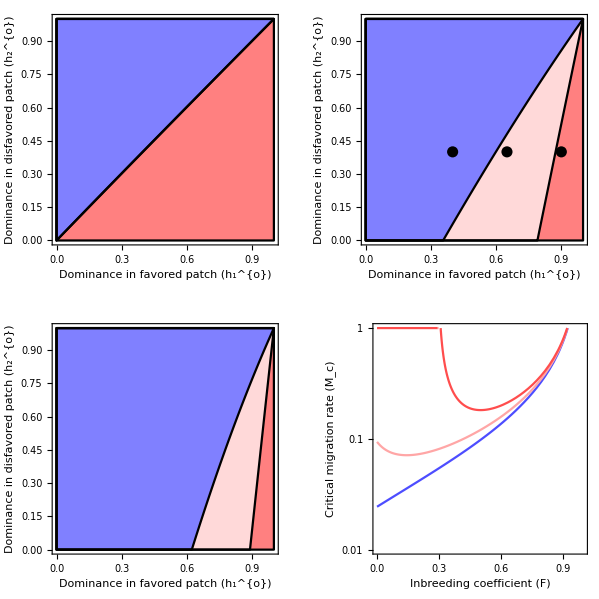

```mathematica
GraphicsGrid[{{G1,G2},{G3,G4}}]
```

## Conditions for polymorphism vs probability of emergence

Here only viability selection and seed migration is given

h2 for which the critical migration rate is the same under full selfing and full outcrossing: corresponds to the limit of the previous plots

```mathematica
h2lim[h1_,s1_,s2_]=(h1 (1+s1) s2)/(h1 s2+s1 (-1+h1-s2+2 h1 s2));
```

Derivative of the probability of emergence in F for F = 0: effect of introducing selfing

```mathematica
dPA[m_,h1_,s1_,h2_,s2_]=D[PA[F,m,h1,s1,h2,s2],F]/.F->0;
dPa[m_,h1_,s1_,h2_,s2_]=D[Pa[F,m,h1,s1,h2,s2],F]/.F->0;
```

The following plot represent the same plots as the last ones in the manuscript except that:
- the line for the critical migration rate is added on the plot
- several migration rates are presented
- both asymmetrical and symmetrical selection are presented

```mathematica
mnum=0.00001;s1num=0.01;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{White,Dashed}];
G1=Show[{f1,f2,f3,f4,f5,f6}];
mnum=0.001;s1num=0.01;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{White,Dashed}];
G2=Show[{f1,f2,f3,f4,f5,f6}];
mnum=0.01;s1num=0.01;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{White,Dashed}];
G3=Show[{f1,f2,f3,f4,f5,f6}];
mnum=0.1;s1num=0.01;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{White,Dashed}];
G4=Show[{f1,f2,f3,f4,f5,f6}];
```

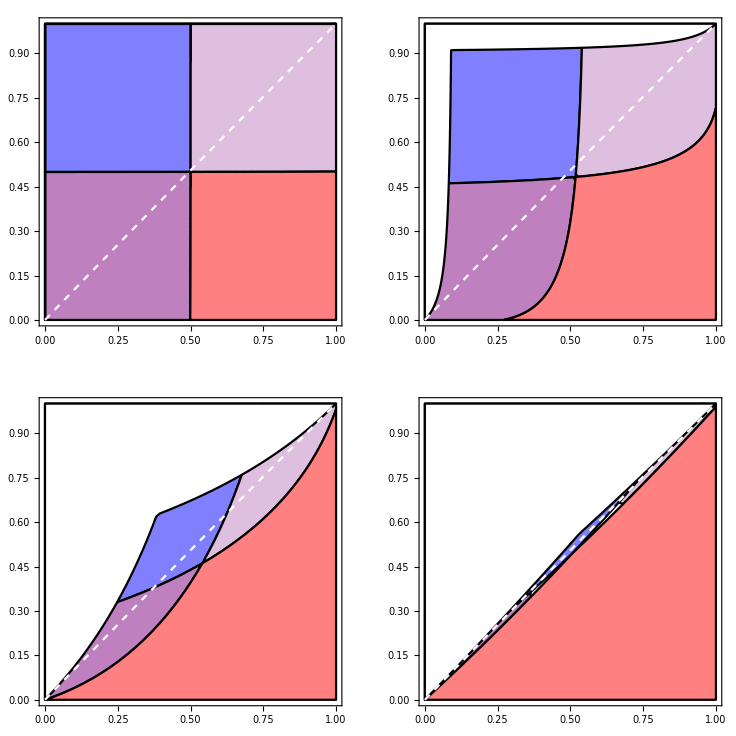

```mathematica
GraphicsGrid[{{Show[G1],Show[G2]},{Show[G3],Show[G4]}}]
```

```mathematica
mnum=0.00001;s1num=0.05;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{White,Dashed}];
G1=Show[{f1,f2,f3,f4,f5,f6}];
mnum=0.001;s1num=0.05;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{White,Dashed}];
G2=Show[{f1,f2,f3,f4,f5,f6}];
mnum=0.01;s1num=0.05;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{White,Dashed}];
G3=Show[{f1,f2,f3,f4,f5,f6}];
mnum=0.1;s1num=0.05;s2num=-0.01;
f1=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Blue,0.5],BoundaryStyle->Black];
f2=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]>0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.5],BoundaryStyle->Black];
f3=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]>0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple,0.75],BoundaryStyle->Black];
f4=RegionPlot[{dPA[mnum,h1,s1num,h2,s2num]<0&&dPa[mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->Lighter[Red,0.5],BoundaryStyle->Black];
f5=RegionPlot[{PA[0,mnum,h1,s1num,h2,s2num]<0 ||Pa[0,mnum,h1,s1num,h2,s2num]<0},{h1,0,1},{h2,0,1},PlotStyle->White,BoundaryStyle->Black];
f6=Plot[h2lim[h1,s1num,s2num],{h1,0,1},PlotStyle->{LightGray,Dashed}];
G4=Show[{f1,f2,f3,f4,f5,f6}];
```

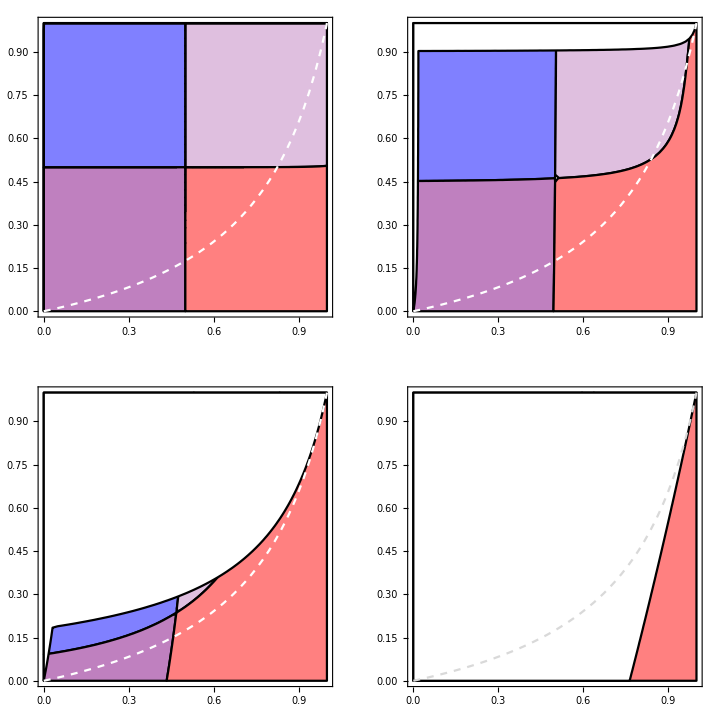

```mathematica
GraphicsGrid[{{Show[G1],Show[G2]},{Show[G3],Show[G4]}}]
```